## Useful functions

```mathematica
<<MaTeX`
texStyle={FontFamily->"Latin Modern Roman",FontSize->12,Magnification->1.6};
ParallelEvaluate[Off[General::munfl,FindFit::cvmit]];
Off[General::munfl,General::stop,LinearSolve::luc,FindFit::cvmit]
SetDirectory[NotebookDirectory[]]
```

/home/kirscher/kette_repo/31_resonances/code

```mathematica
RiccatiBesselJ[z_,l_]:=z SphericalBesselJ[l,z];
RiccatiBesselN[z_,l_]:=(-1.)^l z SphericalBesselY[l,z];
```

```mathematica
(*Boundery conditions for the wavefunction*)
alpha[ra_,ka_,la_,ha_]:=RiccatiBesselN[ka (ra+ha),la]/RiccatiBesselN[ka ra,la]

beta[rb_,kb_,lb_,hb_]:=RiccatiBesselJ[kb (rb+hb),lb]-RiccatiBesselJ[kb rb,lb] (RiccatiBesselN[kb (rb+hb),lb]/RiccatiBesselN[kb rb,lb])
```

LEC=(Λ,a_(3-1)^(S-wave) [fm],C_(2-body) [MeV],C_(3-body) [MeV])
the triton-proton S-wave scattering length is used to calibrate the core parameter and
was obtained by R. Lazauskas.

```mathematica
(* Nuclear E2=2.22 E3=8.48 ℏc=198*)
(* λ a0,r0 (Martin, 23) a1,r1 (Martin,45) a0 (Rimas, unprojected, 6) a1 (Rimas, unprojected, 7) a0 (Rimas, projected, 8) a1 (Rimas, projected, 9)*)
a0a1NUCLmartinrimas=Import[NotebookDirectory[]<>"../data/a0-a1_nucl_Rimas-Martin.dat","Table"][[2;;]];
(* λ C0,D0 (Martin, 23) C0,D0 (Rimas, unprojected, 45) C0,Do (Rimas, projected, 67)*)
LECsNUCLmartinrimas=Import[NotebookDirectory[]<>"../data/LECs_nucl_Rimas-Martin.dat","Table"][[2;;]];
LECsUNITmartinrimas=Import[NotebookDirectory[]<>"../data/LECs_univ_Rimas-Martin.dat","Table"][[2;;]];

activeLEC=LECsNUCLmartinrimas[[All,{1,2,3}]];
```

(non)local resonating-group potentials from a 2- and 3-body contact interaction for TRIMER-FERMION (ABC-A)

W_(non-local) takes the Energy (e_) in [MeV]

```mathematica
NormTF[core_?ArrayQ]:=1./Sqrt[Total[Flatten[Table[core[[i]][[1]] core[[j]][[1]] (Pi/(core[[i]][[2]]+core[[j]][[2]]))^1.5,{i,Length[core]},{j,Length[core]}]]]];

VlocTF[r_,lam_,Cc_,Dd_,Aa_,Bb_]:=Block[{eta2,eta3,w2,w3},
eta2=2. Cc/(2. (Aa+Bb)(3. Aa+3. Bb+2. lam))^(3./2.);
w2=3. (Aa+Bb) lam/(3. (Aa+Bb)+2. lam);
eta3=Dd/(6. (Aa+Bb)^2+16. (Aa+Bb) lam+2. lam^2)^(3./2.);
w3=(3. (Aa+Bb) lam ((Aa+Bb)+2. lam)/(3. (Aa+Bb)^2+8. (Aa+Bb) lam+lam^2));
eta2 Exp[-w2 r^2]+eta3  Exp[-w3 r^2]
];

WnolocTF[r_,rp_,Ee_,lam_,Cc_,Dd_,Aa_,Bb_,Ll_,TwoMyOverHBsq_]:=Block[{zeta1,zeta2,zeta3,a1,b1,c1,a2,b2,c2,a3,b3,c3},
zeta1=(27./64.)(2 (Aa+Bb))^(-3./2.) (1./TwoMyOverHBsq);
a1=(Aa+9. Bb) 3./32.;
b1=(Aa+Bb) 9./16.;
c1=(9. Aa+Bb) 3./32.;

zeta2=-27./32. Cc/(2. (Aa+Bb)+lam)^(3./2.);
zeta3=-27./64. Dd/(2  (Aa+Bb)+5 lam)^(3./2.);

a2=3. (Aa^2+9. Bb^2+10. Aa Bb+(14. Aa+18. Bb) lam)/(16. (2. (Aa+Bb)+lam));
b2=18. (Aa+Bb) ((Aa+Bb)+2. lam)/(16. (2. (Aa+Bb)+lam));
c2=3. (9. Aa^2+Bb^2+10. Aa Bb+(6. Aa+2. Bb) lam)/(16. (2. (Aa+Bb)+lam));

a3=3. (Aa^2+9. Bb^2+10. Aa Bb+(16. Aa+36. Bb) lam+27. lam^2)/(16. (2. (Aa+Bb)+5. lam));
b3=18. ((Aa+Bb)^2+4. (Aa+Bb) lam+3. lam^2)/(16. (2. (Aa+Bb)+5. lam));
c3=3. (9. Aa^2+Bb^2+10. Aa Bb+(24. Aa+4. Bb) lam+3. lam^2)/(16. (2 (Aa+Bb)+5. lam));

-(4 Pi r rp) (
zeta1 Exp[-a1 r^2-c1 rp^2] ((-(4 a1^2 r^2+b1^2 rp^2-2 a1)+(Ll+1) Ll/r^2-TwoMyOverHBsq Ee) I^Ll  SphericalBesselJ[Ll,I b1 r rp]
-4 a1 b1 r rp Sum[(1-Ll^2+l^2) I^(l+1)/Sqrt[3] (2/Sqrt[5])^((Ll+l)/2) SphericalBesselJ[1+l,I b1 r rp],{l,-Ll,Ll}])
+I^Ll zeta2 SphericalBesselJ[Ll,I b2 r rp] Exp[-a2 r^2-c2 rp^2]
+I^Ll zeta3 SphericalBesselJ[Ll,I b3 r rp] Exp[-a3 r^2-c3 rp^2]
)
];
```

The function <SolveSecular> expects the variable <<momentum>> in  [fm^-1]
As  W_(non-local) takes the Energy (e_) in [MeV];
The core wave function is parametrized via the "a0={{c_1,α_1},{c_2,α_2},...,{c_N,α_N}}" array:
ϕ_core=(∑^N)_(i=1)c_i·e_^(-α_i/2∏_j (r^-)_j^2)

```mathematica
SolveSecular[Rdis_?NumberQ,Npoints_?NumberQ,momentum_?NumberQ,Lin_?NumberQ,lam_?NumberQ,c0_?NumberQ,d0_?NumberQ,a00_?ArrayQ,TwoMyOverHBsq_?NumberQ]:=Block[{hDif,Dmat,Kmat,Wmat,bcol,Amat,ucol,wf,tanDelta,usol,energyMeV,nff,cij},

hDif=Rdis/Npoints;
energyMeV=(momentum^2)/TwoMyOverHBsq;
Kmat=SparseArray[{Band[{1,1}]->-2,Band[{2,1}]->1,Band[{1,2}]->1},{Npoints,Npoints}];

Amat=ConstantArray[0,{Npoints,Npoints}];

normsqu=NormTF[a00]^2;

matContainer={};

prefac=1;(*(4 π)^1.5;*)
Do[
If[a00[[ii]][[1]] a00[[jj]][[1]]≠0,

cij=a00[[ii]][[1]] a00[[jj]][[1]] normsqu;

amat=DiagonalMatrix[Table[-hDif^2 TwoMyOverHBsq VlocTF[i hDif,lam,c0,d0,a00[[ii]][[2]],a00[[jj]][[2]]],{i,1,Npoints}]];

wmat=Table[-prefac hDif^3 TwoMyOverHBsq WnolocTF[i hDif,j hDif,energyMeV,lam,c0,d0,a00[[ii]][[2]],a00[[jj]][[2]],Lin,TwoMyOverHBsq],{i,1,Npoints},{j,1,Npoints}]; 

AppendTo[matContainer,cij (amat+wmat)];

]
,{ii,1,Length[a00]},{jj,1,Length[a00]}];

tmpmat=Plus[matContainer[[1]]];
Dmat=DiagonalMatrix[Table[hDif^2 (momentum^2-(Lin (Lin+1))/(i hDif)^2),{i,1,Npoints}]];

Amat=Kmat+Dmat+tmpmat;

bcol=ConstantArray[0,Npoints];
ucol=Array[Subscript["u", ##]&,{Npoints}];

bcol⟦-1⟧=- beta[Rdis,momentum,Lin,hDif];
Amat⟦-1⟧⟦-1⟧=Amat⟦-1⟧⟦-1⟧+alpha[Rdis,momentum,Lin,hDif];

usol=LinearSolve[Amat,bcol];

tanDelta= (RiccatiBesselJ[momentum Rdis,Lin]/RiccatiBesselN[momentum Rdis,Lin])-(usol⟦-1⟧/RiccatiBesselN[momentum Rdis,Lin]);

tanDelta
]
```

numerical and physical parameters

```mathematica
nf={6,4}; (* number form for printing, only *)
k0FM=0.01;  (*initial momentum*)

hbar=197.327053;
Mm=938.92;
m1=3 Mm;m2=Mm;
μ=m1 m2/(m1+m2);
mh2=(2 μ)/(hbar)^2;
sy="nuclear";
Print["E_0 = ",(k0FM hbar)^2/(2 μ)," MeV     ℏ^2/(2 SubscriptBox[μ, A = 4]) = ",hbar^2/(2 (Mm^2/(2 Mm)))," MeV·fm^2     ℏ^2/(2 SubscriptBox[μ, A = 2]) = ",hbar^2/(2 (3 Mm^2/(4 Mm)))]
λRange=Range[1,Length[activeLEC]];
```

E_0 = 0.00276473 MeV     ℏ^2/(2 SubscriptBox[μ, A = 4]) = 41.471 MeV·fm^2     ℏ^2/(2 SubscriptBox[μ, A = 2]) = 27.6473

```mathematica
findLogDivisions[{xmin_,xmax_},n_Integer]:=10^FindDivisions[Log10@{xmin,xmax},n]

GetERE[x_]:=Module[{localcore=x},

core=localcore;

dataS={};dataP={};
tanDsL={};tanDpL={};
tanDs={};tanDp={};

SetSharedVariable[tanDs,tanDp];

ParallelDo[
momFM=Sqrt[mh2 energ];
TanDelSwave=Chop[SolveSecular[rr,nGrid,momFM,0,λ,C0,D0,core,mh2]];
TanDelPwave=Chop[SolveSecular[rr,nGrid,momFM,1,λ,C0,D0,core,mh2]];
AppendTo[tanDs,{energ,TanDelSwave}];
AppendTo[tanDp,{energ,TanDelPwave}];
,{energ,ErangeMeV}];

tanDs=Reverse[Sort[tanDs,#1[[1]]>#2[[1]]&]]; (*Sort all the momentum since it is parallel*)
tanDp=Reverse[Sort[tanDp,#1[[1]]>#2[[1]]&]]; (*Sort all the momentum since it is parallel*)
(*AppendTo[tanDsL,tnDs];
AppendTo[tanDpL,tnDp];*)
(*Extract the ERE Parameters*)
Lrel = 0;
dataS=Transpose[{Sqrt[mh2 ErangeMeV],Sqrt[mh2 ErangeMeV]/Re[tanDs⟦All,2⟧]}];
EreS=Fit[dataS⟦f1;;f2⟧,{1,p^2},p];
a0tf=-Coefficient[EreS,p,0]^-1;
r0tf= Coefficient[EreS,p,2]*2.;
Lrel = 1;
dataP=Transpose[{Sqrt[mh2 ErangeMeV],Sqrt[mh2 ErangeMeV]^3/tanDp⟦All,2⟧}];
EreP=Fit[dataP⟦f1;;f2⟧,{1,p^2},p];
a1tf=-Coefficient[EreP,p,0]^-1;
r1tf= Coefficient[EreP,p,2]*2.;
(*Print["dataS = ", dataS];*)
{a0tf,r0tf,a1tf,r1tf,dataS,dataP}
]
```

## Import density and fit wavefunctions

```mathematica
wflambdasN={1.0,2.0,3.0,4.0,6.0,8.0,10.0};
Martinϕnucl=Cases[Import["../data/abc_u_"<>ToString[NumberForm[#,{12,1}]]<>"_binf_r1b.dnst","Table"],{_?NumberQ,___}]&/@wflambdasN;
MϕN=Transpose[{#⟦All,1⟧,Sqrt[#⟦All,3⟧]}]&/@Martinϕnucl;
wflambdasU={1.5,2.0,3.0,4.0,6.0,8.0,10.0};
Martinϕunit=Cases[Import["../data/abc_univ_"<>ToString[NumberForm[#,{12,1}]]<>"_binf_r1b.dnst","Table"],{_?NumberQ,___}]&/@wflambdasU;
MϕU=Transpose[{#⟦All,1⟧,Sqrt[#⟦All,3⟧]}]&/@Martinϕunit;
If[sy=="unitary",
Mϕ=MϕU;
wflambdas=wflambdasU;
,
Mϕ=MϕN;
wflambdas=wflambdasN;]
```

```mathematica
shift wave functions such that the maximum is consistently located at r=0
```

at consistently functions is located maximum shift such that the wave r=0

```mathematica
wfC={};
Do[
maxR=Mϕ[[nn]][[Position[Mϕ[[nn]],Max[Mϕ[[nn]][[All,2]]]][[1]][[1]]]][[1]];
AppendTo[wfC,Select[Transpose[{Mϕ[[nn]][[All,1]]-maxR,Mϕ[[nn]][[All,2]]}],#[[1]]>=0&]];
,{nn,Range[Length[wflambdas]]}
]
```

{Α1<1.4,-100000<C1<100000,Α2<1.4,-100000<C2<100000,Α3<1.4,-100000<C3<100000,Α4<1.4,-100000<C4<100000,Α5<1.4,-100000<C5<100000,Α6<1.4,-100000<C6<100000,Α7<1.4,-100000<C7<100000,Α8<1.4,-100000<C8<100000}

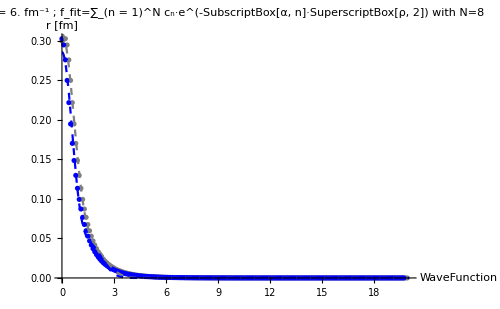

{{-63.6144,0.556555},{9.1046,0.539164},{9.11166,0.54143},{9.13365,0.549566},{9.1447,0.55113},{9.1359,0.550275},{9.18788,0.636694},{9.10501,0.539267}}

{{-63.4676,0.703869},{9.10751,0.689572},{9.10899,0.819952},{9.11208,0.688495},{9.10654,0.688061},{9.10622,0.687043},{9.10583,0.685141},{9.10616,0.68682}}

```mathematica
nk=8;
core={}; Do[core=AppendTo[core,ToExpression@Map[StringJoin[#,ToString[k]]&,{"C","Α"}]],{k,1,nk}];
wf=Total[Flatten[Table[core⟦i⟧⟦1⟧ⅇ^(-core⟦i⟧⟦2⟧ r^2) ,{i,Length[core]}]]];

(* constraints for the fit parameters *)
bcs=Flatten[Table[{core⟦i⟧⟦2⟧<1.4,-10^5<core⟦i⟧⟦1⟧<10^5},{i,Length[core]}]]

wfCores={};wfCoresC={};
wfs={};wfsC={};
w1=1;
w2=All;
Do[
data=Mϕ[[ll]][[w1;;w2]];
AppendTo[wfCores,core/.FindFit[data,{wf,bcs},Flatten[core],r]];
corefit=Transpose[{Flatten[core],Flatten[wfCores[[-1]]]}];
AppendTo[wfs,Total[Flatten[Table[wfCores[[-1]]⟦i⟧⟦1⟧ⅇ^(-wfCores[[-1]]⟦i⟧⟦2⟧ r^2) ,{i,Length[wfCores[[-1]]]}]]]];
data=wfC[[ll]][[w1;;w2]];
AppendTo[wfCoresC,core/.FindFit[data,{wf,bcs},Flatten[core],r]];
corefit=Transpose[{Flatten[core],Flatten[wfCoresC[[-1]]]}];
AppendTo[wfsC,Total[Flatten[Table[wfCoresC[[-1]]⟦i⟧⟦1⟧ⅇ^(-wfCoresC[[-1]]⟦i⟧⟦2⟧ r^2) ,{i,Length[wfCoresC[[-1]]]}]]]];
,{ll,Range[Length[wflambdas]]}];

nwf=5;(*Length[wflambdas];*)
Show[ListPlot[{Select[Mϕ[[nwf]],#[[2]]>0.0&],Select[wfC[[nwf]],#[[2]]>0.0&]},PlotRange->{{0,20},Full},PlotStyle->{Gray,Blue}],
Plot[wfs[[nwf]],{r,0,20},PlotStyle->{Gray,Dashed},PlotLegends->"original Ψ",PlotRange->Full],Plot[wfsC[[nwf]],{r,0,20},PlotStyle->{Blue,Dashed},PlotLegends->"max-to-origin-shifted Ψ",PlotRange->Full],ImageSize->500, AxesLabel->{"WaveFunction","r [fm]"},
PlotLabel->"Λ = "<>ToString[wflambdas[[nwf]]]<>" fm^-1"<>"  ;  f_fit=∑_(n = 1)^N c_n·e^(-SubscriptBox[α, n]·SuperscriptBox[ρ, 2]) with N="<>ToString[nk]]
wfCores[[nwf]]
wfCoresC[[nwf]]
```

## Testing The method with different parameters (λ=4 fm^-1)

## Fast (Rmax = 10, Ngrid=20)

```mathematica
λλ=4;
nwf=Flatten[Position[wflambdas,_?(#==λλ&)]]⟦1⟧;
mycore=wfCores[[nwf]];
rr=10;nGrid=60;
f1=1;f2=4; (* How many momenta should be used to make ere?*)

k0FMin=0.001;
k0FMax=0.03;
Divisions=5;



(*---------------------*)
ErangeMeV=N[findLogDivisions[{(k0FMin hbar)^2/(2 μ),(k0FMax hbar)^2/(2 μ)},Divisions]];
Erange1onfm=Sqrt[2 μ ErangeMeV]/hbar;

(*---------------------*)
nn=Flatten[Position[activeLEC⟦All,1⟧,_?(#==λλ&)]]⟦1⟧;
λ=0.25 activeLEC⟦nn⟧⟦1⟧^2;C0=activeLEC⟦nn⟧⟦2⟧;D0=activeLEC⟦nn⟧⟦3⟧;
Print["λ = Λ^2/4 = ",NumberForm[λ,nf],"  ⇒ Λ = ",NumberForm[2 Sqrt[λ],nf]," ; C_0 = ",NumberForm[C0,nf]," ; D_0 = ",NumberForm[D0,nf]];
Print["Core = ",mycore]
ERE=GetERE[mycore];
Print["ERE = ","     a0 = ", ERE⟦1⟧,"     r0 = ", ERE⟦2⟧,"     a1 = ", ERE⟦3⟧,"     r1 = ", ERE⟦4⟧]
PlotERE
```

λ = Λ^2/4 = 4.0000  ⇒ Λ = 4.0000 ; C_0 = -505.1500 ; D_0 = 1426.7500

Core = {{-62.3853,0.481714},{8.97725,0.542152},{8.94684,0.476539},{8.94428,0.477213},{8.94536,0.476928},{8.957,0.454431},{8.94591,0.476784},{8.94593,0.476779}}

ERE =      a0 = 5.58339     r0 = 3.72103     a1 = -39.4857     r1 = 0.737913

PlotERE

## Fast (Rmax = 10, Ngrid=50)

λ = Λ^2/4 = 4.0000  ⇒ Λ = 4.0000 ; C_0 = -505.1500 ; D_0 = 1426.7500

Core = {{-2.41128,0.674221},{0.178096,0.523946},{1.13023,0.772165},{0.140377,0.77132},{0.140348,0.775363},{0.659603,0.52387},{0.0204887,0.0896991},{0.140377,0.771321},{0.140377,0.771304},{0.140377,0.771309}}

ERE =      a0 = 2.94036     r0 = 55.3933     a1 = -1165.94     r1 = 0.050596

(using more points and up to p^4)  a0 = 3.17771  r0 = 15.3425   ω = -17.5884

S Pole Poitions in momentum: {-0.640758-0.0761334 ⅈ,-0.19281+0.0761334 ⅈ,0.19281+0.0761334 ⅈ,0.640758-0.0761334 ⅈ}

S Pole Poitions in energy:   {11.1909+2.69744 ⅈ,0.867553-0.811685 ⅈ,0.867553+0.811685 ⅈ,11.1909-2.69744 ⅈ}

(using more points and up to p^4)  a0 = -13.7015  r0 = -61.4005   ω = 335.984

P Pole Poitions in momentum: {-0.298211+0.0015302 ⅈ,-0.0494229-0.0000420287 ⅈ,0.0494229-0.0000420287 ⅈ,0.298211+0.0015302 ⅈ}

P Pole Poitions in energy:   {2.4586-0.0252321 ⅈ,0.067532+0.000114857 ⅈ,0.067532-0.000114857 ⅈ,2.4586+0.0252321 ⅈ}

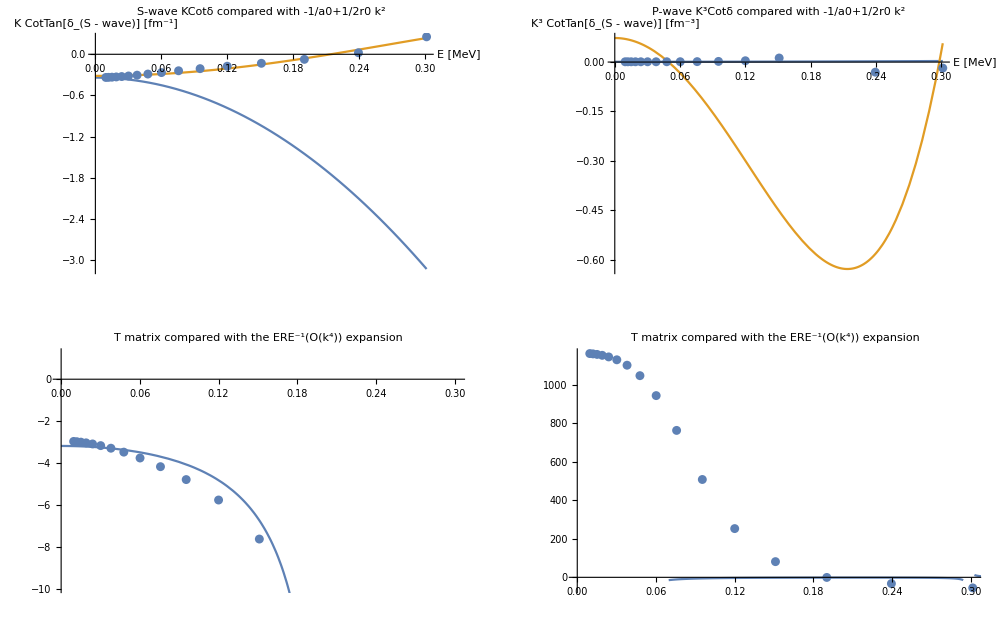

```mathematica
λλ=4;
mycore=core4;
rr=10;nGrid=50;
f1=1;f2=4; (* How many momenta should be used to make ere?*)

k0FMin=0.01;
k0FMax=0.3;
Divisions=20;



(*---------------------*)
ErangeMeV=N[findLogDivisions[{(k0FMin hbar)^2/(2 μ),(k0FMax hbar)^2/(2 μ)},Divisions]];
Erange1onfm=Sqrt[2 μ ErangeMeV]/hbar;

(*---------------------*)
nn=Flatten[Position[activeLEC⟦All,1⟧,_?(#==λλ&)]]⟦1⟧;
λ=0.25 activeLEC⟦nn⟧⟦1⟧^2;C0=activeLEC⟦nn⟧⟦2⟧;D0=activeLEC⟦nn⟧⟦3⟧;
Print["λ = Λ^2/4 = ",NumberForm[λ,nf],"  ⇒ Λ = ",NumberForm[2 Sqrt[λ],nf]," ; C_0 = ",NumberForm[C0,nf]," ; D_0 = ",NumberForm[D0,nf]];
Print["Core = ",mycore]
ERE=GetERE[mycore];
Print["ERE = ","     a0 = ", ERE⟦1⟧,"     r0 = ", ERE⟦2⟧,"     a1 = ", ERE⟦3⟧,"     r1 = ", ERE⟦4⟧]
PlotERE
```

## Fast (Rmax = 10, Ngrid=50) Less points

λ = Λ^2/4 = 4.0000  ⇒ Λ = 4.0000 ; C_0 = -505.1500 ; D_0 = 1426.7500

Core = {{-2.41128,0.674221},{0.178096,0.523946},{1.13023,0.772165},{0.140377,0.77132},{0.140348,0.775363},{0.659603,0.52387},{0.0204887,0.0896991},{0.140377,0.771321},{0.140377,0.771304},{0.140377,0.771309}}

ERE =      a0 = 2.94301     r0 = 50.7551     a1 = -1167.22     r1 = 0.0644615

(using more points and up to p^4)  a0 = 3.13164  r0 = 14.1315   ω = 9.40751

S Pole Poitions in momentum: {-0.19861+0.0646897 ⅈ,0.+0.819704 ⅈ,0.-0.949084 ⅈ,0.19861+0.0646897 ⅈ}

S Pole Poitions in energy:   {0.974878-0.710428 ⅈ,-18.5767+0. ⅈ,-24.9036+0. ⅈ,0.974878+0.710428 ⅈ}

(using more points and up to p^4)  a0 = -7.3931  r0 = -132.419   ω = 566.4

P Pole Poitions in momentum: {-0.338843+0.000899055 ⅈ,-0.0456063-0.0000162868 ⅈ,0.0456063-0.0000162868 ⅈ,0.338843+0.000899055 ⅈ}

P Pole Poitions in energy:   {3.1743-0.0168449 ⅈ,0.0575046+0.0000410718 ⅈ,0.0575046-0.0000410718 ⅈ,3.1743+0.0168449 ⅈ}

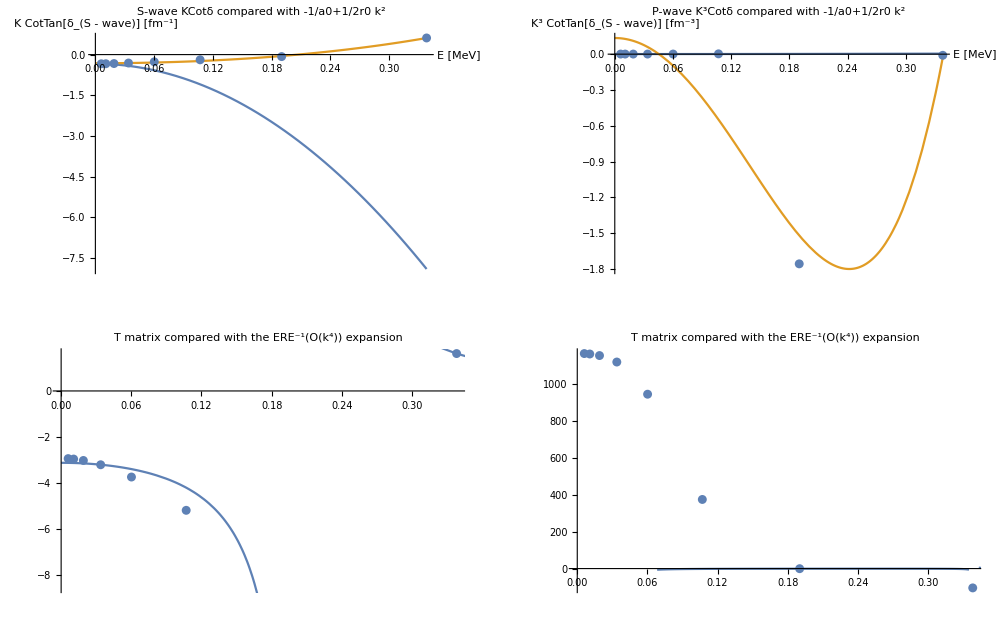

```mathematica
λλ=4;
mycore=core4;
rr=10;nGrid=50;
f1=1;f2=4; (* How many momenta should be used to make ere?*)

k0FMin=0.01;
k0FMax=0.3;
Divisions=8;



(*---------------------*)
ErangeMeV=N[findLogDivisions[{(k0FMin hbar)^2/(2 μ),(k0FMax hbar)^2/(2 μ)},Divisions]];
Erange1onfm=Sqrt[2 μ ErangeMeV]/hbar;

(*---------------------*)
nn=Flatten[Position[activeLEC⟦All,1⟧,_?(#==λλ&)]]⟦1⟧;
λ=0.25 activeLEC⟦nn⟧⟦1⟧^2;C0=activeLEC⟦nn⟧⟦2⟧;D0=activeLEC⟦nn⟧⟦3⟧;
Print["λ = Λ^2/4 = ",NumberForm[λ,nf],"  ⇒ Λ = ",NumberForm[2 Sqrt[λ],nf]," ; C_0 = ",NumberForm[C0,nf]," ; D_0 = ",NumberForm[D0,nf]];
Print["Core = ",mycore]
ERE=GetERE[mycore];
Print["ERE = ","     a0 = ", ERE⟦1⟧,"     r0 = ", ERE⟦2⟧,"     a1 = ", ERE⟦3⟧,"     r1 = ", ERE⟦4⟧]
PlotERE
```

## Medium (Rmax = 10, Ngrid=100)

```mathematica
λλ=4;
mycore=core4;
rr=10;nGrid=100;
f1=1;f2=4; (* How many momenta should be used to make ere?*)

k0FMin=0.01;
k0FMax=0.3;
Divisions=8;



(*---------------------*)
ErangeMeV=N[findLogDivisions[{(k0FMin hbar)^2/(2 μ),(k0FMax hbar)^2/(2 μ)},Divisions]];
Erange1onfm=Sqrt[2 μ ErangeMeV]/hbar;

(*---------------------*)
nn=Flatten[Position[activeLEC⟦All,1⟧,_?(#==λλ&)]]⟦1⟧;
λ=0.25 activeLEC⟦nn⟧⟦1⟧^2;C0=activeLEC⟦nn⟧⟦2⟧;D0=activeLEC⟦nn⟧⟦3⟧;
Print["λ = Λ^2/4 = ",NumberForm[λ,nf],"  ⇒ Λ = ",NumberForm[2 Sqrt[λ],nf]," ; C_0 = ",NumberForm[C0,nf]," ; D_0 = ",NumberForm[D0,nf]];
Print["Core = ",mycore]
ERE=GetERE[mycore];
Print["ERE = ","     a0 = ", ERE⟦1⟧,"     r0 = ", ERE⟦2⟧,"     a1 = ", ERE⟦3⟧,"     r1 = ", ERE⟦4⟧]
PlotERE
```

## Double grid (Rmax = 10, Ngrid=200)

```mathematica
λλ=4;
mycore=core4;
rr=10;nGrid=200;
f1=1;f2=4; (* How many momenta should be used to make ere?*)

k0FMin=0.01;
k0FMax=0.3;
Divisions=20;



(*---------------------*)
ErangeMeV=N[findLogDivisions[{(k0FMin hbar)^2/(2 μ),(k0FMax hbar)^2/(2 μ)},Divisions]];
Erange1onfm=Sqrt[2 μ ErangeMeV]/hbar;

(*---------------------*)
nn=Flatten[Position[activeLEC⟦All,1⟧,_?(#==λλ&)]]⟦1⟧;
λ=0.25 activeLEC⟦nn⟧⟦1⟧^2;C0=activeLEC⟦nn⟧⟦2⟧;D0=activeLEC⟦nn⟧⟦3⟧;
Print["λ = Λ^2 = ",NumberForm[λ,nf],"  ⇒ Λ = ",NumberForm[2 Sqrt[λ],nf]," ; C_0 = ",NumberForm[C0,nf]," ; D_0 = ",NumberForm[D0,nf]];
Print["Core = ",mycore]
ERE=GetERE[mycore];
Print["ERE = ","     a0 = ", ERE⟦1⟧,"     r0 = ", ERE⟦2⟧,"     a1 = ", ERE⟦3⟧,"     r1 = ", ERE⟦4⟧]
PlotERE
```

## Long (Rmax = 15, Ngrid=50)

λ = Λ^2/4 = 4.0000  ⇒ Λ = 4.0000 ; C_0 = -505.1500 ; D_0 = 1426.7500

Core = {{-2.41128,0.674221},{0.178096,0.523946},{1.13023,0.772165},{0.140377,0.77132},{0.140348,0.775363},{0.659603,0.52387},{0.0204887,0.0896991},{0.140377,0.771321},{0.140377,0.771304},{0.140377,0.771309}}

ERE =      a0 = 2.95929     r0 = 224.061     a1 = 4543.42     r1 = -0.055605

(using more points and up to p^4)  a0 = 2.93913  r0 = 274.982   ω = -55337.4

S Pole Poitions in momentum: {-0.0452261-0.024939 ⅈ,-0.0410256+0.024939 ⅈ,0.0410256+0.024939 ⅈ,0.0452261-0.024939 ⅈ}

S Pole Poitions in energy:   {0.0393546+0.0623666 ⅈ,0.0293379-0.0565741 ⅈ,0.0293379+0.0565741 ⅈ,0.0393546-0.0623666 ⅈ}

(using more points and up to p^4)  a0 = 4551.41  r0 = -0.0640873   ω = 9.21783

P Pole Poitions in momentum: {-0.0658917+0.0286274 ⅈ,0.-0.0470093 ⅈ,0.+0.0982397 ⅈ,0.0658917+0.0286274 ⅈ}

P Pole Poitions in energy:   {0.0973791-0.104303 ⅈ,-0.0610971+0. ⅈ,-0.266826+0. ⅈ,0.0973791+0.104303 ⅈ}

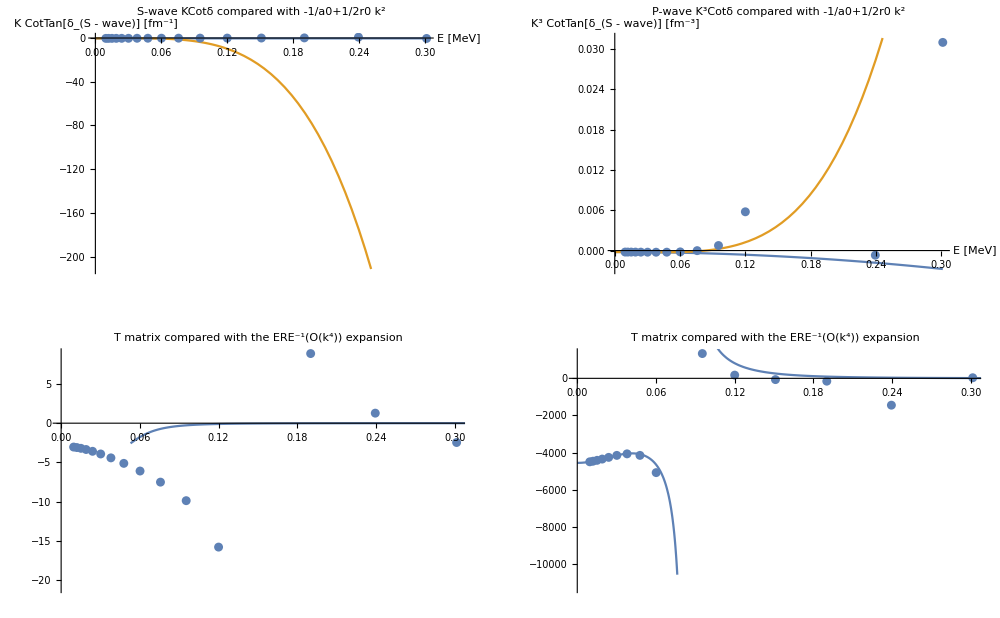

```mathematica
λλ=4;
mycore=core4;
rr=15;nGrid=50;
f1=1;f2=4; (* How many momenta should be used to make ere?*)

k0FMin=0.01;
k0FMax=0.3;
Divisions=20;



(*---------------------*)
ErangeMeV=N[findLogDivisions[{(k0FMin hbar)^2/(2 μ),(k0FMax hbar)^2/(2 μ)},Divisions]];
Erange1onfm=Sqrt[2 μ ErangeMeV]/hbar;

(*---------------------*)
nn=Flatten[Position[activeLEC⟦All,1⟧,_?(#==λλ&)]]⟦1⟧;
λ=0.25 activeLEC⟦nn⟧⟦1⟧^2;C0=activeLEC⟦nn⟧⟦2⟧;D0=activeLEC⟦nn⟧⟦3⟧;
Print["λ = Λ^2/4 = ",NumberForm[λ,nf],"  ⇒ Λ = ",NumberForm[2 Sqrt[λ],nf]," ; C_0 = ",NumberForm[C0,nf]," ; D_0 = ",NumberForm[D0,nf]];
Print["Core = ",mycore]
ERE=GetERE[mycore];
Print["ERE = ","     a0 = ", ERE⟦1⟧,"     r0 = ", ERE⟦2⟧,"     a1 = ", ERE⟦3⟧,"     r1 = ", ERE⟦4⟧]
PlotERE
```

## Test dynamical (Rmax = 200, Ngrid=200)

```mathematica
λλ=4;
mycore=core4;
rr=200;nGrid=200;
f1=1;f2=4; (* How many momenta should be used to make ere?*)

k0FMin=0.01;
k0FMax=0.3;
Divisions=20;



(*---------------------*)
ErangeMeV=N[findLogDivisions[{(k0FMin hbar)^2/(2 μ),(k0FMax hbar)^2/(2 μ)},Divisions]];
Erange1onfm=Sqrt[2 μ ErangeMeV]/hbar;

(*---------------------*)
nn=Flatten[Position[activeLEC⟦All,1⟧,_?(#==λλ&)]]⟦1⟧;
λ=0.25 activeLEC⟦nn⟧⟦1⟧^2;C0=activeLEC⟦nn⟧⟦2⟧;D0=activeLEC⟦nn⟧⟦3⟧;
Print["λ = Λ^2/4 = ",NumberForm[λ,nf],"  ⇒ Λ = ",NumberForm[2 Sqrt[λ],nf]," ; C_0 = ",NumberForm[C0,nf]," ; D_0 = ",NumberForm[D0,nf]];
Print["Core = ",mycore]
ERE=GetERE[mycore];
Print["ERE = ","     a0 = ", ERE⟦1⟧,"     r0 = ", ERE⟦2⟧,"     a1 = ", ERE⟦3⟧,"     r1 = ", ERE⟦4⟧]
PlotERE
```

## Test different number of gaussians

```mathematica
λλ=1;
mycore=core1;
rr=10;nGrid=20;
f1=1;f2=4; (* How many momenta should be used to make ere?*)

k0FMin=0.01;
k0FMax=0.3;
Divisions=3;

(*---------------------*)
ErangeMeV=N[findLogDivisions[{(k0FMin hbar)^2/(2 μ),(k0FMax hbar)^2/(2 μ)},Divisions]];
Erange1onfm=Sqrt[2 μ ErangeMeV]/hbar;
```

```mathematica
nk=1;
core={}; Do[core=AppendTo[core,ToExpression@Map[StringJoin[#,ToString[k]]&,{"C","Α"}]],{k,1,nk}];
wf=Total[Flatten[Table[core⟦i⟧⟦1⟧ⅇ^(-core⟦i⟧⟦2⟧ r^2) ,{i,Length[core]}]]];
core4fit1=core/.FindFit[Mϕ4,wf,Flatten[core],r];
(*corefit=Transpose[{Flatten[core],Flatten[core4fit1]}];*)
wf41    =Total[Flatten[Table[core4fit1⟦i⟧⟦1⟧ⅇ^(-core4fit1⟦i⟧⟦2⟧ r^2) ,{i,Length[core4fit1]}]]];
Print["wf42 = ", wf41]
Print["Core = ",core4fit1]
```

wf42 = 0.267153 ⅇ^(-0.604403 r^2)

Core = {{0.267153,0.604403}}

```mathematica
ERE1=GetERE[core4fit1];
Print["ERE = ","     a0 = ", ERE1⟦1⟧,"     r0 = ", ERE1⟦2⟧,"     a1 = ", ERE1⟦3⟧,"     r1 = ", ERE1⟦4⟧]
```

ERE =      a0 = 1.56284     r0 = 32.3506     a1 = 331.168     r1 = 0.846664

///////////////////////////////////////////////////

```mathematica
nk=2;
core={}; Do[core=AppendTo[core,ToExpression@Map[StringJoin[#,ToString[k]]&,{"C","Α"}]],{k,1,nk}];
wf=Total[Flatten[Table[core⟦i⟧⟦1⟧ⅇ^(-core⟦i⟧⟦2⟧ r^2) ,{i,Length[core]}]]];
corefit=Transpose[{Flatten[core],Flatten[Join[core4fit1,{0,1}]]}];
core4fit2=core/.FindFit[Mϕ4,wf,corefit,r]; coretemp=core4fit2;
wf42    =Total[Flatten[Table[coretemp⟦i⟧⟦1⟧ⅇ^(-coretemp⟦i⟧⟦2⟧ r^2) ,{i,Length[coretemp]}]]];
Print["wf42 = ", wf42]
Print["Core = ",core4fit2]
```

wf42 = 0.208715 ⅇ^(-1.03031 r^2)+0.0699775 ⅇ^(-0.178617 r^2)

Core = {{0.0699775,0.178617},{0.208715,1.03031}}

```mathematica
ERE2=GetERE[core4fit2];
Print["ERE = ","     a0 = ", ERE2⟦1⟧,"     r0 = ", ERE2⟦2⟧,"     a1 = ", ERE2⟦3⟧,"     r1 = ", ERE2⟦4⟧]
```

ERE =      a0 = 3.59734     r0 = 11.8764     a1 = 378.735     r1 = 3.22056

///////////////////////////////////////////////////

```mathematica
nk=3;
core={}; Do[core=AppendTo[core,ToExpression@Map[StringJoin[#,ToString[k]]&,{"C","Α"}]],{k,1,nk}];
wf=Total[Flatten[Table[core⟦i⟧⟦1⟧ⅇ^(-core⟦i⟧⟦2⟧ r^2) ,{i,Length[core]}]]];
corefit=Transpose[{Flatten[core],Flatten[Join[core4fit2,{0,1}]]}];
core4fit3=core/.FindFit[Mϕ4,wf,corefit,r]; coretemp=core4fit3;
wf43    =Total[Flatten[Table[coretemp⟦i⟧⟦1⟧ⅇ^(-coretemp⟦i⟧⟦2⟧ r^2) ,{i,Length[coretemp]}]]];
Print["wf42 = ", wf43]
Print["Core = ",core4fit3]
```

wf42 = 0.190749 ⅇ^(-1.11015 r^2)+0.0779683 ⅇ^(-0.259997 r^2)+0.0104705 ⅇ^(-0.0670365 r^2)

Core = {{0.0104705,0.0670365},{0.190749,1.11015},{0.0779683,0.259997}}

```mathematica
ERE3=GetERE[core4fit3];
Print["ERE = ","     a0 = ", ERE3⟦1⟧,"     r0 = ", ERE3⟦2⟧,"     a1 = ", ERE3⟦3⟧,"     r1 = ", ERE3⟦4⟧]
```

ERE =      a0 = 3.57076     r0 = 12.1468     a1 = 392.116     r1 = 1.97392

///////////////////////////////////////////////////

```mathematica
nk=4;
core={}; Do[core=AppendTo[core,ToExpression@Map[StringJoin[#,ToString[k]]&,{"C","Α"}]],{k,1,nk}];
wf=Total[Flatten[Table[core⟦i⟧⟦1⟧ⅇ^(-core⟦i⟧⟦2⟧ r^2) ,{i,Length[core]}]]];
corefit=Transpose[{Flatten[core],Flatten[Join[core4fit3,{0,1}]]}];
core4fit4=core/.FindFit[Mϕ4,wf,corefit,r]; coretemp=core4fit4;
wf44    =Total[Flatten[Table[coretemp⟦i⟧⟦1⟧ⅇ^(-coretemp⟦i⟧⟦2⟧ r^2) ,{i,Length[coretemp]}]]];
Print["wf42 = ", wf44]
Print["Core = ",core4fit4]
```

wf42 = 11.7722 ⅇ^(-0.697371 r^2)-21.4816 ⅇ^(-0.656532 r^2)+9.96717 ⅇ^(-0.614137 r^2)+0.0212291 ⅇ^(-0.0911775 r^2)

Core = {{0.0212291,0.0911775},{11.7722,0.697371},{9.96717,0.614137},{-21.4816,0.656532}}

```mathematica
ERE4=GetERE[core4fit4];
Print["ERE = ","     a0 = ", ERE4⟦1⟧,"     r0 = ", ERE4⟦2⟧,"     a1 = ", ERE4⟦3⟧,"     r1 = ", ERE4⟦4⟧]
```

ERE =      a0 = 4.15383     r0 = 10.0856     a1 = 366.233     r1 = 3.31025

///////////////////////////////////////////////////

```mathematica
nk=5;
core={}; Do[core=AppendTo[core,ToExpression@Map[StringJoin[#,ToString[k]]&,{"C","Α"}]],{k,1,nk}];
wf=Total[Flatten[Table[core⟦i⟧⟦1⟧ⅇ^(-core⟦i⟧⟦2⟧ r^2) ,{i,Length[core]}]]];
corefit=Transpose[{Flatten[core],Flatten[Join[core4fit4,{0,1}]]}];
core4fit5=core/.FindFit[Mϕ4,wf,corefit,r]; coretemp=core4fit5;
wf45    =Total[Flatten[Table[coretemp⟦i⟧⟦1⟧ⅇ^(-coretemp⟦i⟧⟦2⟧ r^2) ,{i,Length[coretemp]}]]];
Print["wf42 = ", wf45]
Print["Core = ",core4fit5]
```

wf42 = -0.0222702 ⅇ^(-13.4312 r^2)+11.7999 ⅇ^(-0.967679 r^2)-18.3632 ⅇ^(-0.91956 r^2)+6.82173 ⅇ^(-0.843146 r^2)+0.0363787 ⅇ^(-0.120562 r^2)

Core = {{0.0363787,0.120562},{11.7999,0.967679},{6.82173,0.843146},{-18.3632,0.91956},{-0.0222702,13.4312}}

```mathematica
ERE5=GetERE[core4fit5];
Print["ERE = ","     a0 = ", ERE5⟦1⟧,"     r0 = ", ERE5⟦2⟧,"     a1 = ", ERE5⟦3⟧,"     r1 = ", ERE5⟦4⟧]
```

ERE =      a0 = 4.08909     r0 = 10.2217     a1 = 338.845     r1 = 4.00831

///////////////////////////////////////////////////

```mathematica
nk=6;
core={}; Do[core=AppendTo[core,ToExpression@Map[StringJoin[#,ToString[k]]&,{"C","Α"}]],{k,1,nk}];
wf=Total[Flatten[Table[core⟦i⟧⟦1⟧ⅇ^(-core⟦i⟧⟦2⟧ r^2) ,{i,Length[core]}]]];
corefit=Transpose[{Flatten[core],Flatten[Join[core4fit5,{0,1}]]}];
core4fit6=core/.FindFit[Mϕ4,wf,corefit,r]; coretemp=core4fit6;
wf46   =Total[Flatten[Table[coretemp⟦i⟧⟦1⟧ⅇ^(-coretemp⟦i⟧⟦2⟧ r^2) ,{i,Length[coretemp]}]]];
Print["wf42 = ", wf46]
Print["Core = ",core4fit6]
```

wf42 = -0.0302991 ⅇ^(-10.4696 r^2)+0.12586 ⅇ^(-1.93942 r^2)+11.9093 ⅇ^(-0.428648 r^2)-18.1891 ⅇ^(-0.414682 r^2)+6.44366 ⅇ^(-0.391316 r^2)+0.0133019 ⅇ^(-0.0750482 r^2)

Core = {{0.0133019,0.0750482},{11.9093,0.428648},{6.44366,0.391316},{-18.1891,0.414682},{-0.0302991,10.4696},{0.12586,1.93942}}

```mathematica
ERE6=GetERE[core4fit6];
Print["ERE = ","     a0 = ", ERE6⟦1⟧,"     r0 = ", ERE6⟦2⟧,"     a1 = ", ERE6⟦3⟧,"     r1 = ", ERE6⟦4⟧]
```

ERE =      a0 = 3.76573     r0 = 11.3732     a1 = 395.255     r1 = 2.23355

///////////////////////////////////////////////////

```mathematica
nk=8;
core={}; Do[core=AppendTo[core,ToExpression@Map[StringJoin[#,ToString[k]]&,{"C","Α"}]],{k,1,nk}];
wf=Total[Flatten[Table[core⟦i⟧⟦1⟧ⅇ^(-core⟦i⟧⟦2⟧ r^2) ,{i,Length[core]}]]];
corefit=Transpose[{Flatten[core],Flatten[Join[core4fit6,{0,1,1,1}]]}];
core4fit8=core/.FindFit[Mϕ4,wf,corefit,r]; coretemp=core4fit8;
wf48   =Total[Flatten[Table[coretemp⟦i⟧⟦1⟧ⅇ^(-coretemp⟦i⟧⟦2⟧ r^2) ,{i,Length[coretemp]}]]];
Print["wf42 = ", wf48]
Print["Core = ",core4fit8]
```

wf42 = -0.0314119 ⅇ^(-10.2312 r^2)+0.114946 ⅇ^(-2.04609 r^2)-0.0526506 ⅇ^(-0.704412 r^2)+0.174145 ⅇ^(-0.704217 r^2)+19.4859 ⅇ^(-0.227556 r^2)-6.2585 ⅇ^(-0.227552 r^2)-13.1701 ⅇ^(-0.227551 r^2)+0.0103602 ⅇ^(-0.0683271 r^2)

Core = {{0.0103602,0.0683271},{19.4859,0.227556},{-13.1701,0.227551},{-6.2585,0.227552},{-0.0314119,10.2312},{0.114946,2.04609},{0.174145,0.704217},{-0.0526506,0.704412}}

```mathematica
ERE8=GetERE[core4fit8];
Print["ERE = ","     a0 = ", ERE8⟦1⟧,"     r0 = ", ERE8⟦2⟧,"     a1 = ", ERE8⟦3⟧,"     r1 = ", ERE8⟦4⟧]
```

ERE =      a0 = 3.43623     r0 = 12.7176     a1 = 392.398     r1 = 1.83421

///////////////////////////////////////////////////

```mathematica
nk=10;
core={}; Do[core=AppendTo[core,ToExpression@Map[StringJoin[#,ToString[k]]&,{"C","Α"}]],{k,1,nk}];
wf=Total[Flatten[Table[core⟦i⟧⟦1⟧ⅇ^(-core⟦i⟧⟦2⟧ r^2) ,{i,Length[core]}]]];
corefit=Transpose[{Flatten[core],Flatten[Join[core4fit8,{0,1,1,1}]]}];
core4fit10=core/.FindFit[Mϕ4,wf,corefit,r]; coretemp=core4fit10;
wf410   =Total[Flatten[Table[coretemp⟦i⟧⟦1⟧ⅇ^(-coretemp⟦i⟧⟦2⟧ r^2) ,{i,Length[coretemp]}]]];
Print["wf42 = ", wf410]
Print["Core = ",core4fit10]
```

wf42 = 0.0202393 ⅇ^(-786.081 r^2)-0.23392 ⅇ^(-258.694 r^2)+0.217283 ⅇ^(-238.251 r^2)-5.92873 ⅇ^(-6.92447 r^2)+19.1989 ⅇ^(-6.28944 r^2)-13.6112 ⅇ^(-5.96629 r^2)+0.428962 ⅇ^(-3.07924 r^2)-0.417121 ⅇ^(-0.557666 r^2)+0.562414 ⅇ^(-0.55671 r^2)+0.0359315 ⅇ^(-0.120343 r^2)

Core = {{0.0359315,0.120343},{19.1989,6.28944},{-13.6112,5.96629},{-5.92873,6.92447},{-0.23392,258.694},{0.428962,3.07924},{0.217283,238.251},{0.0202393,786.081},{-0.417121,0.557666},{0.562414,0.55671}}

```mathematica
ERE10=GetERE[core4fit10];
Print["ERE = ","     a0 = ", ERE10⟦1⟧,"     r0 = ", ERE10⟦2⟧,"     a1 = ", ERE10⟦3⟧,"     r1 = ", ERE10⟦4⟧]
```

ERE =      a0 = 4.06758     r0 = 10.2861     a1 = 344.981     r1 = 3.8791

///////////////////////////////////////////////////

```mathematica
nk=13;
core={}; Do[core=AppendTo[core,ToExpression@Map[StringJoin[#,ToString[k]]&,{"C","Α"}]],{k,1,nk}];
wf=Total[Flatten[Table[core⟦i⟧⟦1⟧ⅇ^(-core⟦i⟧⟦2⟧ r^2) ,{i,Length[core]}]]];
corefit=Transpose[{Flatten[core],Flatten[Join[core4fit10,{0,1,1,0.5,-1,1}]]}];
core4fit13=core/.FindFit[Mϕ4,wf,corefit,r]; coretemp=core4fit13;
wf413   =Total[Flatten[Table[coretemp⟦i⟧⟦1⟧ⅇ^(-coretemp⟦i⟧⟦2⟧ r^2) ,{i,Length[coretemp]}]]];
Print["wf42 = ", wf413]
Print["Core = ",core4fit13]
```

wf42 = 0.0121029 ⅇ^(-5822.24 r^2)-0.231365 ⅇ^(-175.179 r^2)+0.219453 ⅇ^(-169.5 r^2)-5.85462 ⅇ^(-6.44036 r^2)+19.2736 ⅇ^(-6.13027 r^2)-13.5357 ⅇ^(-5.99108 r^2)+0.156486 ⅇ^(-3.19769 r^2)+0.124891 ⅇ^(-1.02859 r^2)+0.552781 ⅇ^(-0.290106 r^2)-0.983822 ⅇ^(-0.252207 r^2)-0.437862 ⅇ^(-0.231372 r^2)+0.970658 ⅇ^(-0.227824 r^2)+0.00622414 ⅇ^(-0.0565427 r^2)

Core = {{0.00622414,0.0565427},{19.2736,6.13027},{-13.5357,5.99108},{-5.85462,6.44036},{-0.231365,175.179},{0.156486,3.19769},{0.219453,169.5},{0.0121029,5822.24},{-0.437862,0.231372},{0.552781,0.290106},{0.124891,1.02859},{0.970658,0.227824},{-0.983822,0.252207}}

```mathematica
ERE=GetERE[core4fit13];
ERE13=ERE; Print["ERE = ","     a0 = ", ERE⟦1⟧,"     r0 = ", ERE⟦2⟧,"     a1 = ", ERE⟦3⟧,"     r1 = ", ERE⟦4⟧]
```

ERE =      a0 = 2.67437     r0 = 17.2543     a1 = 371.003     r1 = 1.35912

///////////////////////////////////////////////////

```mathematica
nk=16;
core={}; Do[core=AppendTo[core,ToExpression@Map[StringJoin[#,ToString[k]]&,{"C","Α"}]],{k,1,nk}];
wf=Total[Flatten[Table[core⟦i⟧⟦1⟧ⅇ^(-core⟦i⟧⟦2⟧ r^2) ,{i,Length[core]}]]];
corefit=Transpose[{Flatten[core],Flatten[Join[core4fit13,{0.01,0.1,-0.01,0.2,0.005,0.3}]]}];
core4fit16=core/.FindFit[Mϕ4,wf,corefit,r]; coretemp=core4fit16;
wf416   =Total[Flatten[Table[coretemp⟦i⟧⟦1⟧ⅇ^(-coretemp⟦i⟧⟦2⟧ r^2) ,{i,Length[coretemp]}]]];
Print["wf42 = ", wf416]
Print["Core = ",core4fit16]
```

General::ovfl: Overflow occurred in computation.

FindFit::nrlnum: The function value {7.95641×10^-13,Overflow[],Overflow[],Overflow[],Overflow[],Overflow[],Overflow[],Overflow[],Overflow[],Overflow[],«191»} is not a list of real numbers with dimensions {201} at {C1,Α1,C2,Α2,C3,Α3,C4,Α4,C5,Α5,«22»} = {-0.00890893,0.0275873,19.2991,6.18898,-13.5105,6.08759,-5.82669,6.43834,-0.231081,181.185,«22»}.

wf42 = 0.219719 ⅇ^(-186.552 r^2)-0.231081 ⅇ^(-181.185 r^2)+0.00284814 ⅇ^(-9.39115 r^2)-5.82669 ⅇ^(-6.43834 r^2)+19.2991 ⅇ^(-6.18898 r^2)-13.5105 ⅇ^(-6.08759 r^2)+0.0802371 ⅇ^(-2.75326 r^2)+0.114534 ⅇ^(-1.05585 r^2)-0.00816805 ⅇ^(-0.634048 r^2)-0.980121 ⅇ^(-0.293998 r^2)+0.974614 ⅇ^(-0.248754 r^2)+0.5506 ⅇ^(-0.233698 r^2)-0.433661 ⅇ^(-0.197942 r^2)+0.0190933 ⅇ^(-0.0340403 r^2)-0.00890893 ⅇ^(-0.0275873 r^2)+0.0111707 ⅇ^(3.69824×10^26 r^2)

Core = {{-0.00890893,0.0275873},{19.2991,6.18898},{-13.5105,6.08759},{-5.82669,6.43834},{-0.231081,181.185},{0.0802371,2.75326},{0.219719,186.552},{0.0111707,-3.69824×10^26},{-0.433661,0.197942},{0.5506,0.233698},{0.114534,1.05585},{0.974614,0.248754},{-0.980121,0.293998},{0.0190933,0.0340403},{-0.00816805,0.634048},{0.00284814,9.39115}}

```mathematica
(*ERE=GetERE[core4fit16];
ERE16=ERE;
Print["ERE = ","     a0 = ", ERE⟦1⟧,"     r0 = ", ERE⟦2⟧,"     a1 = ", ERE⟦3⟧,"     r1 = ", ERE⟦4⟧]*)
```

///////////////////////////////////////////////////

```mathematica
(*nk=20;
core={}; Do[core=AppendTo[core,ToExpression@Map[StringJoin[#,ToString[k]]&,{"C","Α"}]],{k,1,nk}];
wf=Total[Flatten[Table[core⟦i⟧⟦1⟧ⅇ^(-core⟦i⟧⟦2⟧ r^2) ,{i,Length[core]}]]];
corefit=Transpose[{Flatten[core],Flatten[Join[core4fit16,{0,0.1,0,0,1,0.3,0,0.8}]]}];
core4fit20=core/.FindFit[Mϕ4,wf,corefit,r]; coretemp=core4fit20;
wf420   =Total[Flatten[Table[coretemp⟦i⟧⟦1⟧ⅇ^(-coretemp⟦i⟧⟦2⟧ r^2) ,{i,Length[coretemp]}]]];
Print["wf42 = ", wf420]
Print["Core = ",core4fit20]*)
```

```mathematica
(*ERE=GetERE[core4fit20];
ERE20=ERE;
Print["ERE = ","     a0 = ", ERE⟦1⟧,"     r0 = ", ERE⟦2⟧,"     a1 = ", ERE⟦3⟧,"     r1 = ", ERE⟦4⟧]*)
```

///////////////////////////////////////////////////

```mathematica
(*nk=25;
core={}; Do[core=AppendTo[core,ToExpression@Map[StringJoin[#,ToString[k]]&,{"C","Α"}]],{k,1,nk}];
wf=Total[Flatten[Table[core⟦i⟧⟦1⟧ⅇ^(-core⟦i⟧⟦2⟧ r^2) ,{i,Length[core]}]]];
(* Preliminary easy fit for starting point*)
corefit=Transpose[{Flatten[core],Flatten[Join[mycore20,{0,0,0,0,0,0,0,0,0,0}]]}]

mycore25=core/.FindFit[Mϕ4,wf,corefit,r];
wf425    =Total[Flatten[Table[mycore25⟦i⟧⟦1⟧ⅇ^(-mycore25⟦i⟧⟦2⟧ r^2) ,{i,Length[mycore25]}]]];
Print["wf45 = ", wf425]

Print["Core = ",mycore25]
ERE=GetERE[mycore25];
ERE25=ERE;
Print["ERE = ","     a0 = ", ERE⟦1⟧,"     r0 = ", ERE⟦2⟧,"     a1 = ", ERE⟦3⟧,"     r1 = ", ERE⟦4⟧]*)
```

```mathematica
ERE1
ERE2
ERE3
ERE4
ERE5
ERE6
ERE8
ERE10
ERE13
ERE16
(*ERE20
ERE25*)
```

{1.56284,32.3506,331.168,0.846664}

{3.59734,11.8764,378.735,3.22056}

{3.57076,12.1468,392.116,1.97392}

{4.15383,10.0856,366.233,3.31025}

{4.08909,10.2217,338.845,4.00831}

{3.76573,11.3732,395.255,2.23355}

{3.43623,12.7176,392.398,1.83421}

{4.06758,10.2861,344.981,3.8791}

{2.67437,17.2543,371.003,1.35912}

{3.42711,12.5677,-201.41,-5.15173}

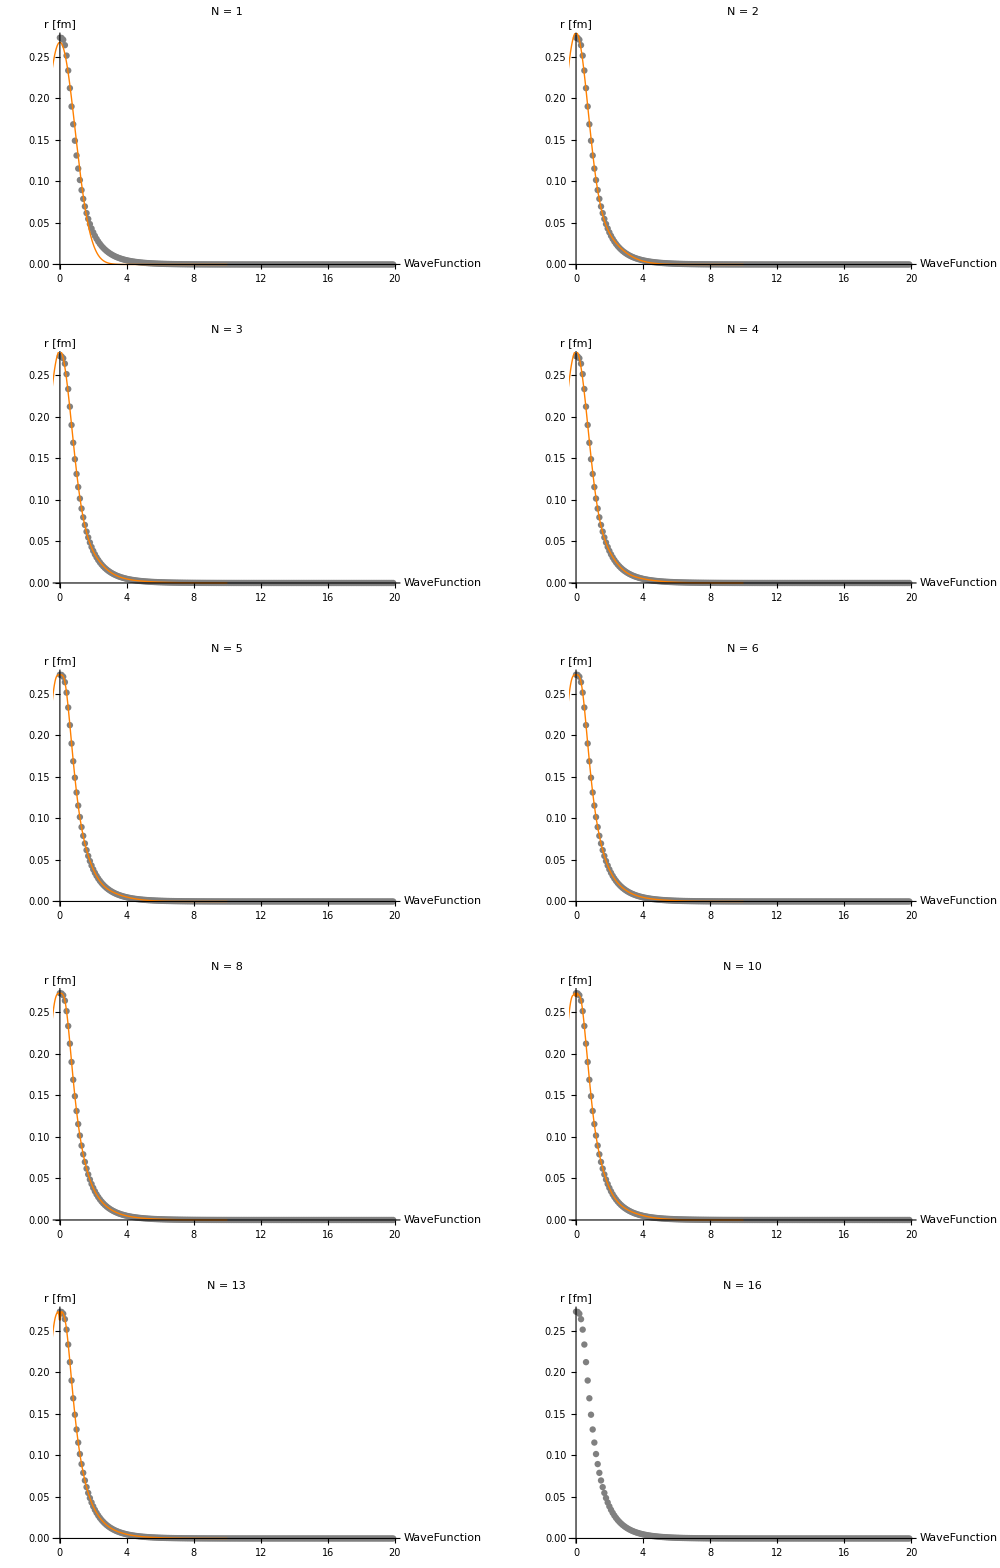

```mathematica
GraphicsGrid[{{
Show[ListPlot[Mϕ4,PlotRange->All,PlotStyle->Gray],Plot[wf41,{r,-1,10},PlotStyle->{Orange,Thick}],ImageSize->500, AxesLabel->{"WaveFunction","r [fm]"},PlotLabel->"N = 1 " ],
Show[ListPlot[Mϕ4,PlotRange->All,PlotStyle->Gray],Plot[wf42,{r,-1,10},PlotStyle->{Orange,Thick}],ImageSize->500, AxesLabel->{"WaveFunction","r [fm]"},PlotLabel->"N = 2 " ]},
{
Show[ListPlot[Mϕ4,PlotRange->All,PlotStyle->Gray],Plot[wf43,{r,-1,10},PlotStyle->{Orange,Thick}],ImageSize->500, AxesLabel->{"WaveFunction","r [fm]"},PlotLabel->"N = 3 " ],
Show[ListPlot[Mϕ4,PlotRange->All,PlotStyle->Gray],Plot[wf44,{r,-1,10},PlotStyle->{Orange,Thick}],ImageSize->500, AxesLabel->{"WaveFunction","r [fm]"},PlotLabel->"N = 4 " ]}
,
{
Show[ListPlot[Mϕ4,PlotRange->All,PlotStyle->Gray],Plot[wf45,{r,-1,10},PlotStyle->{Orange,Thick}],ImageSize->500, AxesLabel->{"WaveFunction","r [fm]"},PlotLabel->"N = 5 " ],
Show[ListPlot[Mϕ4,PlotRange->All,PlotStyle->Gray],Plot[wf46,{r,-1,10},PlotStyle->{Orange,Thick}],ImageSize->500, AxesLabel->{"WaveFunction","r [fm]"},PlotLabel->"N = 6 " ]}
,
{
Show[ListPlot[Mϕ4,PlotRange->All,PlotStyle->Gray],Plot[wf48,{r,-1,10},PlotStyle->{Orange,Thick}],ImageSize->500, AxesLabel->{"WaveFunction","r [fm]"},PlotLabel->"N = 8 " ],
Show[ListPlot[Mϕ4,PlotRange->All,PlotStyle->Gray],Plot[wf410,{r,-1,10},PlotStyle->{Orange,Thick}],ImageSize->500, AxesLabel->{"WaveFunction","r [fm]"},PlotLabel->"N = 10 " ]},
{
Show[ListPlot[Mϕ4,PlotRange->All,PlotStyle->Gray],Plot[wf413,{r,-1,10},PlotStyle->{Orange,Thick}],ImageSize->500, AxesLabel->{"WaveFunction","r [fm]"},PlotLabel->"N = 13 " ],
Show[ListPlot[Mϕ4,PlotRange->All,PlotStyle->Gray],Plot[wf416,{r,-1,10},PlotStyle->{Orange,Thick}],ImageSize->500, AxesLabel->{"WaveFunction","r [fm]"},PlotLabel->"N = 16 " ]}(*,
{
Show[ListPlot[Mϕ4,PlotRange->All,PlotStyle->Gray],Plot[wf420,{r,-1,10},PlotStyle->{Orange,Thick}],ImageSize->500, AxesLabel->{"WaveFunction","r [fm]"},PlotLabel->"N = 20 " ],
Show[ListPlot[Mϕ4,PlotRange->All,PlotStyle->Gray],Plot[wf425,{r,-1,10},PlotStyle->{Orange,Thick}],ImageSize->500, AxesLabel->{"WaveFunction","r [fm]"},PlotLabel->"N = 25 " ]}*)
},ImageSize->1000]
```

## Calculate all the cut-off

λ = Λ^2 = 0.2500  ⇒ Λ = 1.0000 ; C_0 = -44.4515 ; D_0 = 27.2450

Core = {{0.0104681,0.0590441},{19.4476,0.227153},{-13.2084,0.227669},{-6.29678,0.227644},{-0.0506365,0.983042},{0.100223,0.814662},{0.203803,0.34142},{-0.0607092,0.591595}}

ERE =      a0 = 3.3665     r0 = 38.8546     a1 = -158.126     r1 = 1.04245

(using more points and up to p^4)  a0 = 3.36306  r0 = 43.9872   ω = -2088.6

S Pole Poitions in momentum: {-0.103597-0.0584845 ⅈ,-0.0814797+0.0584845 ⅈ,0.0814797+0.0584845 ⅈ,0.103597-0.0584845 ⅈ}

S Pole Poitions in energy:   {0.202152+0.335019 ⅈ,0.0889829-0.263496 ⅈ,0.0889829+0.263496 ⅈ,0.202152-0.335019 ⅈ}

(using more points and up to p^4)  a0 = -157.983  r0 = 0.945339   ω = 39.5182

P Pole Poitions in momentum: {-0.0605586-0.0904817 ⅈ,-0.0536216+0.103134 ⅈ,0.0536216+0.103134 ⅈ,0.0605586-0.0904817 ⅈ}

P Pole Poitions in energy:   {-0.124955+0.302984 ⅈ,-0.214581-0.305791 ⅈ,-0.214581+0.305791 ⅈ,-0.124955-0.302984 ⅈ}

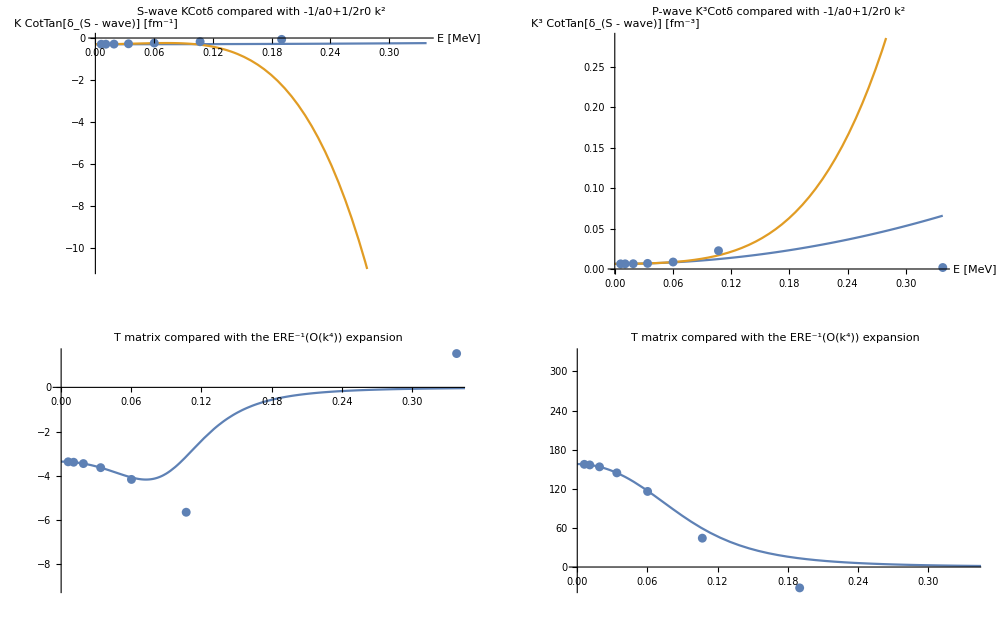

```mathematica
λλ=1;
mycore=core1;
rr=10;nGrid=50;
f1=1;f2=4; (* How many momenta should be used to make ere?*)

k0FMin=0.01;
k0FMax=0.3;
Divisions=8;



(*---------------------*)
ErangeMeV=N[findLogDivisions[{(k0FMin hbar)^2/(2 μ),(k0FMax hbar)^2/(2 μ)},Divisions]];
Erange1onfm=Sqrt[2 μ ErangeMeV]/hbar;

(*---------------------*)
nn=Flatten[Position[activeLEC⟦All,1⟧,_?(#==λλ&)]]⟦1⟧;
λ=0.25 activeLEC⟦nn⟧⟦1⟧^2;C0=activeLEC⟦nn⟧⟦2⟧;D0=activeLEC⟦nn⟧⟦3⟧;
Print["λ = Λ^2 = ",NumberForm[λ,nf],"  ⇒ Λ = ",NumberForm[2 Sqrt[λ],nf]," ; C_0 = ",NumberForm[C0,nf]," ; D_0 = ",NumberForm[D0,nf]];
Print["Core = ",mycore]
ERE1=GetERE[mycore];
Print["ERE = ","     a0 = ", ERE1⟦1⟧,"     r0 = ", ERE1⟦2⟧,"     a1 = ", ERE1⟦3⟧,"     r1 = ", ERE1⟦4⟧]
PlotERE
```

λ = Λ^2 = 1.0000  ⇒ Λ = 2.0000 ; C_0 = -142.3630 ; D_0 = 173.9250

Core = {{0.00764983,0.0582864},{19.4593,0.226339},{-13.1966,0.226712},{-6.28506,0.226631},{-0.0117586,4.23779},{0.0938859,1.03697},{0.201406,0.365917},{-0.0572968,0.366599}}

ERE =      a0 = 2.73081     r0 = 67.3153     a1 = -147.772     r1 = 1.16209

(using more points and up to p^4)  a0 = 2.72534  r0 = 79.7379   ω = -5055.1

S Pole Poitions in momentum: {-0.0853779-0.0481557 ⅈ,-0.0723563+0.0481557 ⅈ,0.0723563+0.0481557 ⅈ,0.0853779-0.0481557 ⅈ}

S Pole Poitions in energy:   {0.137419+0.227341 ⅈ,0.0806323-0.192667 ⅈ,0.0806323+0.192667 ⅈ,0.137419-0.227341 ⅈ}

(using more points and up to p^4)  a0 = -147.631  r0 = 1.05287   ω = 44.4429

P Pole Poitions in momentum: {-0.0592482-0.0901682 ⅈ,-0.0529844+0.101419 ⅈ,0.0529844+0.101419 ⅈ,0.0592482-0.0901682 ⅈ}

P Pole Poitions in energy:   {-0.127729+0.295401 ⅈ,-0.206757-0.297132 ⅈ,-0.206757+0.297132 ⅈ,-0.127729-0.295401 ⅈ}

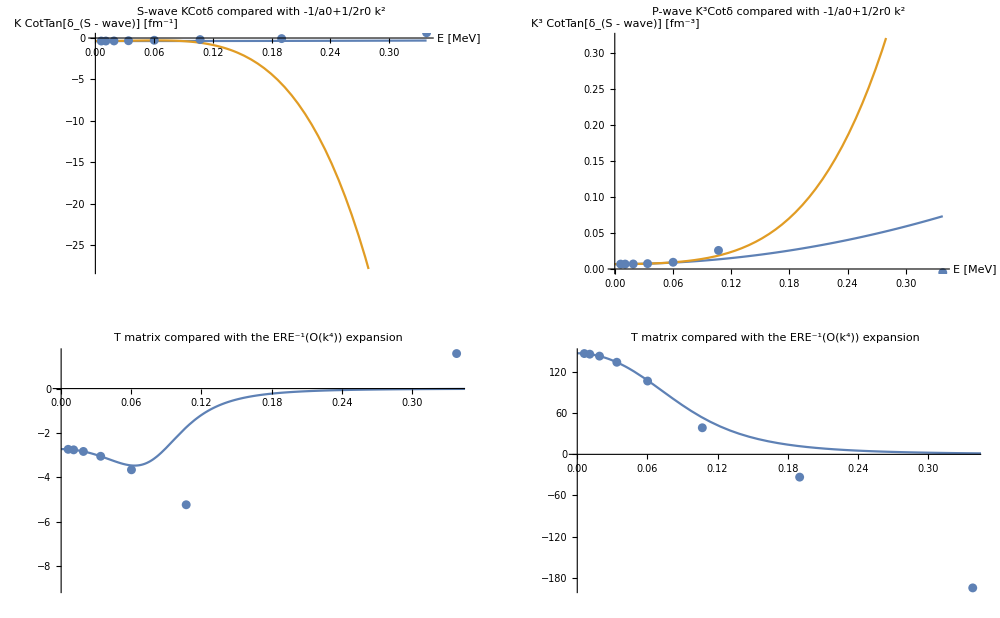

```mathematica
λλ=2;
mycore=core2;
rr=10;nGrid=50;
f1=1;f2=4; (* How many momenta should be used to make ere?*)

k0FMin=0.01;
k0FMax=0.3;
Divisions=8;



(*---------------------*)
ErangeMeV=N[findLogDivisions[{(k0FMin hbar)^2/(2 μ),(k0FMax hbar)^2/(2 μ)},Divisions]];
Erange1onfm=Sqrt[2 μ ErangeMeV]/hbar;

(*---------------------*)
nn=Flatten[Position[activeLEC⟦All,1⟧,_?(#==λλ&)]]⟦1⟧;
λ=0.25 activeLEC⟦nn⟧⟦1⟧^2;C0=activeLEC⟦nn⟧⟦2⟧;D0=activeLEC⟦nn⟧⟦3⟧;
Print["λ = Λ^2 = ",NumberForm[λ,nf],"  ⇒ Λ = ",NumberForm[2 Sqrt[λ],nf]," ; C_0 = ",NumberForm[C0,nf]," ; D_0 = ",NumberForm[D0,nf]];
Print["Core = ",mycore]
ERE2=GetERE[mycore];
Print["ERE = ","     a0 = ", ERE2⟦1⟧,"     r0 = ", ERE2⟦2⟧,"     a1 = ", ERE2⟦3⟧,"     r1 = ", ERE2⟦4⟧]
PlotERE
```

λ = Λ^2 = 2.2500  ⇒ Λ = 3.0000 ; C_0 = -295.9300 ; D_0 = 566.6500

Core = {{0.00903191,0.0639109},{19.4827,0.225945},{-13.1733,0.226027},{-6.26172,0.22601},{-0.0224689,7.15337},{0.104973,1.58776},{0.18292,0.580836},{-0.073076,0.581481}}

ERE =      a0 = 2.99815     r0 = 51.5441     a1 = -145.681     r1 = 1.19117

(using more points and up to p^4)  a0 = 2.99391  r0 = 59.5287   ω = -3249.16

S Pole Poitions in momentum: {-0.0941125-0.0532039 ⅈ,-0.077232+0.0532039 ⅈ,0.077232+0.0532039 ⅈ,0.0941125-0.0532039 ⅈ}

S Pole Poitions in energy:   {0.166617+0.276869 ⅈ,0.0866502-0.227208 ⅈ,0.0866502+0.227208 ⅈ,0.166617-0.276869 ⅈ}

(using more points and up to p^4)  a0 = -145.54  r0 = 1.07882   ω = 45.7199

P Pole Poitions in momentum: {-0.0589192-0.0900255 ⅈ,-0.0528114+0.100962 ⅈ,0.0528114+0.100962 ⅈ,0.0589192-0.0900255 ⅈ}

P Pole Poitions in energy:   {-0.128094+0.293296 ⅈ,-0.204707-0.294827 ⅈ,-0.204707+0.294827 ⅈ,-0.128094-0.293296 ⅈ}

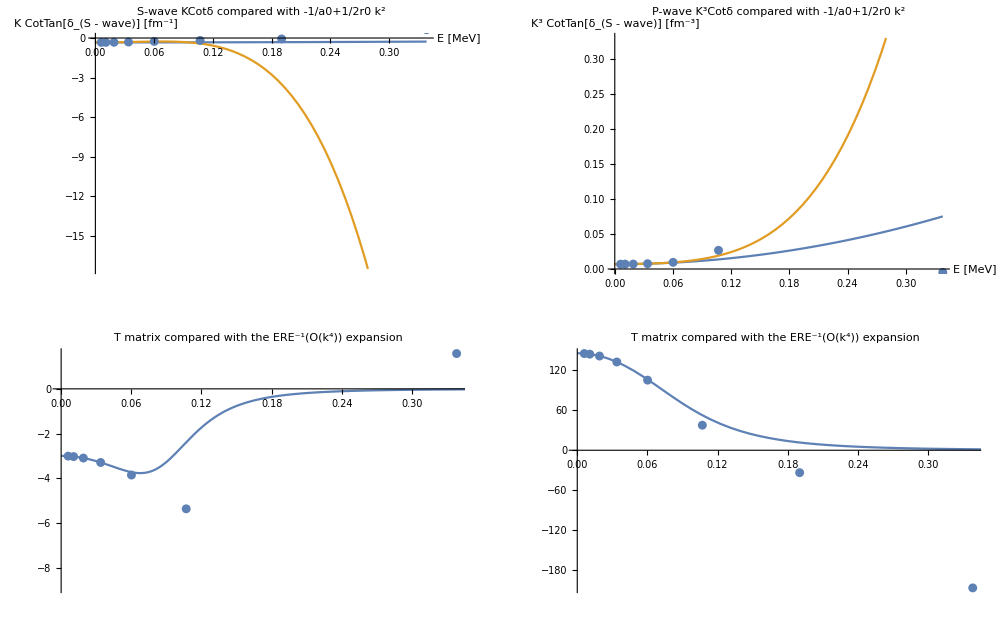

```mathematica
λλ=3;
mycore=core3;
rr=10;nGrid=50;
f1=1;f2=4; (* How many momenta should be used to make ere?*)

k0FMin=0.01;
k0FMax=0.3;
Divisions=8;



(*---------------------*)
ErangeMeV=N[findLogDivisions[{(k0FMin hbar)^2/(2 μ),(k0FMax hbar)^2/(2 μ)},Divisions]];
Erange1onfm=Sqrt[2 μ ErangeMeV]/hbar;

(*---------------------*)
nn=Flatten[Position[activeLEC⟦All,1⟧,_?(#==λλ&)]]⟦1⟧;
λ=0.25 activeLEC⟦nn⟧⟦1⟧^2;C0=activeLEC⟦nn⟧⟦2⟧;D0=activeLEC⟦nn⟧⟦3⟧;
Print["λ = Λ^2 = ",NumberForm[λ,nf],"  ⇒ Λ = ",NumberForm[2 Sqrt[λ],nf]," ; C_0 = ",NumberForm[C0,nf]," ; D_0 = ",NumberForm[D0,nf]];
Print["Core = ",mycore]
ERE3=GetERE[mycore];
Print["ERE = ","     a0 = ", ERE3⟦1⟧,"     r0 = ", ERE3⟦2⟧,"     a1 = ", ERE3⟦3⟧,"     r1 = ", ERE3⟦4⟧]
PlotERE
```

λ = Λ^2 = 4.0000  ⇒ Λ = 4.0000 ; C_0 = -505.1500 ; D_0 = 1426.7500

Core = {{0.0103312,0.068248},{19.5051,0.225756},{-13.1509,0.225747},{-6.23929,0.225749},{-0.0313955,10.2345},{0.115063,2.04468},{0.121496,0.703201},{-0.0577311,0.225762}}

ERE =      a0 = 3.18554     r0 = 43.0926     a1 = -143.999     r1 = 1.21512

(using more points and up to p^4)  a0 = 3.18201  r0 = 48.9935   ω = -2401.22

S Pole Poitions in momentum: {-0.100854-0.0569408 ⅈ,-0.0807136+0.0569408 ⅈ,0.0807136+0.0569408 ⅈ,0.100854-0.0569408 ⅈ}

S Pole Poitions in energy:   {0.191578+0.317542 ⅈ,0.0904743-0.254129 ⅈ,0.0904743+0.254129 ⅈ,0.191578-0.317542 ⅈ}

(using more points and up to p^4)  a0 = -143.858  r0 = 1.10016   ω = 46.778

P Pole Poitions in momentum: {-0.0586588-0.0899086 ⅈ,-0.0526751+0.100597 ⅈ,0.0526751+0.100597 ⅈ,0.0586588-0.0899086 ⅈ}

P Pole Poitions in energy:   {-0.128358+0.291621 ⅈ,-0.203075-0.293005 ⅈ,-0.203075+0.293005 ⅈ,-0.128358-0.291621 ⅈ}

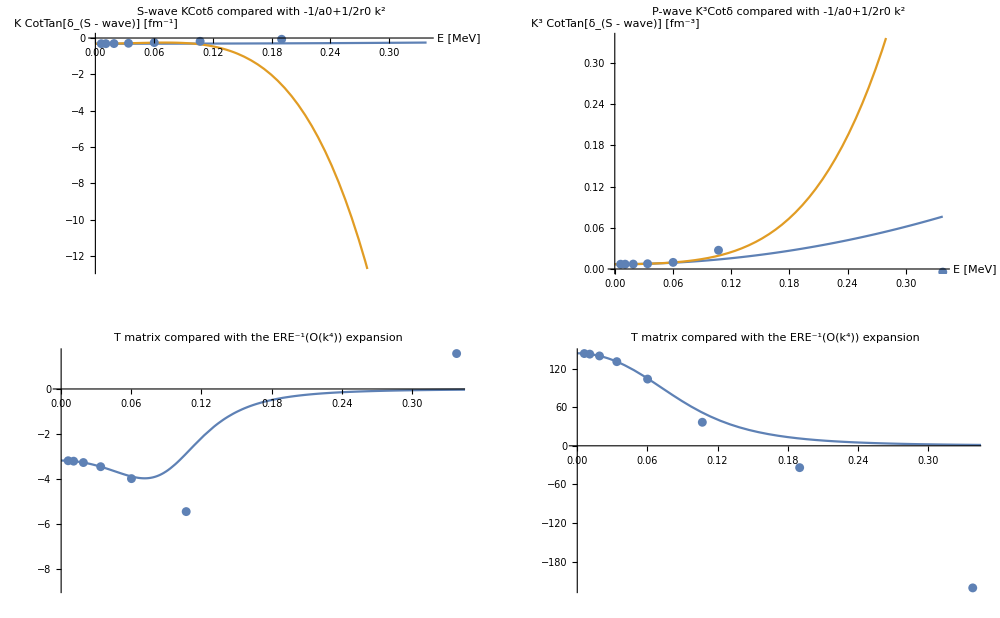

```mathematica
λλ=4;
mycore=core4;
rr=10;nGrid=50;
f1=1;f2=4; (* How many momenta should be used to make ere?*)

k0FMin=0.01;
k0FMax=0.3;
Divisions=8;



(*---------------------*)
ErangeMeV=N[findLogDivisions[{(k0FMin hbar)^2/(2 μ),(k0FMax hbar)^2/(2 μ)},Divisions]];
Erange1onfm=Sqrt[2 μ ErangeMeV]/hbar;

(*---------------------*)
nn=Flatten[Position[activeLEC⟦All,1⟧,_?(#==λλ&)]]⟦1⟧;
λ=0.25 activeLEC⟦nn⟧⟦1⟧^2;C0=activeLEC⟦nn⟧⟦2⟧;D0=activeLEC⟦nn⟧⟦3⟧;
Print["λ = Λ^2 = ",NumberForm[λ,nf],"  ⇒ Λ = ",NumberForm[2 Sqrt[λ],nf]," ; C_0 = ",NumberForm[C0,nf]," ; D_0 = ",NumberForm[D0,nf]];
Print["Core = ",mycore]
ERE4=GetERE[mycore];
Print["ERE = ","     a0 = ", ERE4⟦1⟧,"     r0 = ", ERE4⟦2⟧,"     a1 = ", ERE4⟦3⟧,"     r1 = ", ERE4⟦4⟧]
PlotERE
```

λ = Λ^2 = 9.0000  ⇒ Λ = 6.0000 ; C_0 = -1090.5500 ; D_0 = 6552.5000

Core = {{0.149857,1.50919},{19.3943,0.222273},{-13.2618,0.223679},{-6.35024,0.223405},{-0.0522161,15.1361},{0.0668994,4.08587},{0.480022,0.315758},{-0.126977,0.222086}}

ERE =      a0 = 0.0720745     r0 = 25040.1     a1 = -143.178     r1 = 1.22242

(using more points and up to p^4)  a0 = 0.0510065  r0 = 121942.   ω = -3.9432×10^7

S Pole Poitions in momentum: {-0.0330175-0.0000199974 ⅈ,-0.0213559+0.0000199974 ⅈ,0.0213559+0.0000199974 ⅈ,0.0330175-0.0000199974 ⅈ}

S Pole Poitions in energy:   {0.0301399+0.0000365092 ⅈ,0.0126092-0.0000236143 ⅈ,0.0126092+0.0000236143 ⅈ,0.0301399-0.0000365092 ⅈ}

(using more points and up to p^4)  a0 = -143.038  r0 = 1.10696   ω = 46.9833

P Pole Poitions in momentum: {-0.0586433-0.0899791 ⅈ,-0.0526779+0.100621 ⅈ,0.0526779+0.100621 ⅈ,0.0586433-0.0899791 ⅈ}

P Pole Poitions in energy:   {-0.128759+0.291772 ⅈ,-0.203199-0.293091 ⅈ,-0.203199+0.293091 ⅈ,-0.128759-0.291772 ⅈ}

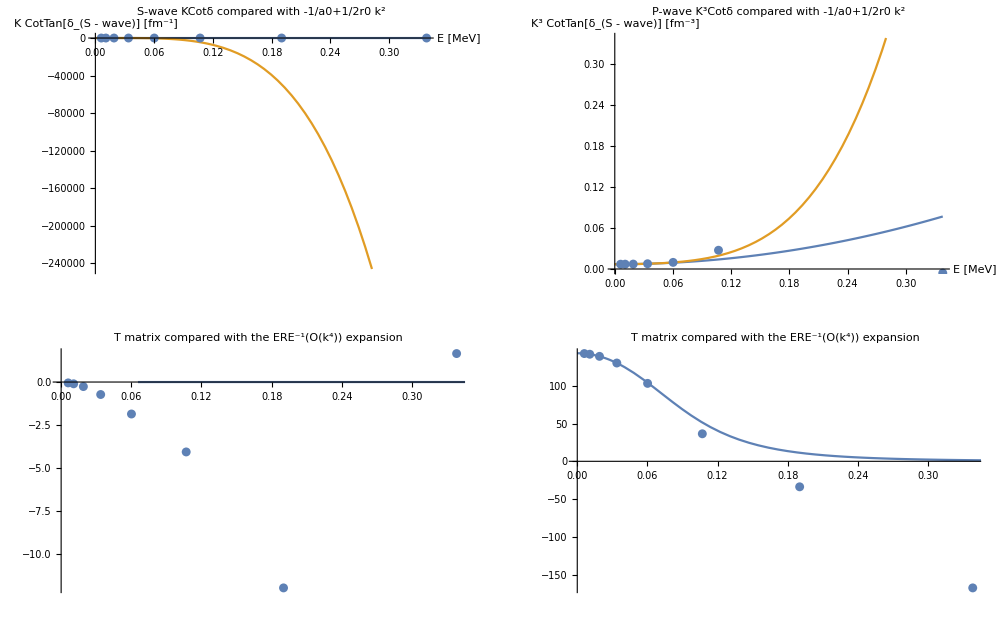

```mathematica
λλ=6;
mycore=core6;
rr=10;nGrid=50;
f1=1;f2=4; (* How many momenta should be used to make ere?*)

k0FMin=0.01;
k0FMax=0.3;
Divisions=8;



(*---------------------*)
ErangeMeV=N[findLogDivisions[{(k0FMin hbar)^2/(2 μ),(k0FMax hbar)^2/(2 μ)},Divisions]];
Erange1onfm=Sqrt[2 μ ErangeMeV]/hbar;

(*---------------------*)
nn=Flatten[Position[activeLEC⟦All,1⟧,_?(#==λλ&)]]⟦1⟧;
λ=0.25 activeLEC⟦nn⟧⟦1⟧^2;C0=activeLEC⟦nn⟧⟦2⟧;D0=activeLEC⟦nn⟧⟦3⟧;
Print["λ = Λ^2 = ",NumberForm[λ,nf],"  ⇒ Λ = ",NumberForm[2 Sqrt[λ],nf]," ; C_0 = ",NumberForm[C0,nf]," ; D_0 = ",NumberForm[D0,nf]];
Print["Core = ",mycore]
ERE6=GetERE[mycore];
Print["ERE = ","     a0 = ", ERE6⟦1⟧,"     r0 = ", ERE6⟦2⟧,"     a1 = ", ERE6⟦3⟧,"     r1 = ", ERE6⟦4⟧]
PlotERE
```

λ = Λ^2 = 16.0000  ⇒ Λ = 8.0000 ; C_0 = -1898.5500 ; D_0 = 25697

Core = {{0.154778,1.47566},{19.3694,0.220111},{-13.2868,0.221636},{-6.37525,0.221313},{-0.0604235,20.6989},{0.0901911,4.24319},{0.573716,0.299596},{-0.151559,0.222378}}

ERE =      a0 = 0.0781169     r0 = 22811.     a1 = -143.065     r1 = 1.22389

(using more points and up to p^4)  a0 = 0.0559849  r0 = 108381.   ω = -3.48208×10^7

S Pole Poitions in momentum: {-0.0328986-0.000023603 ⅈ,-0.0217704+0.000023603 ⅈ,0.0217704+0.000023603 ⅈ,0.0328986-0.000023603 ⅈ}

S Pole Poitions in energy:   {0.0299232+0.0000429366 ⅈ,0.0131035-0.000028413 ⅈ,0.0131035+0.000028413 ⅈ,0.0299232-0.0000429366 ⅈ}

(using more points and up to p^4)  a0 = -142.926  r0 = 1.10828   ω = 47.0459

P Pole Poitions in momentum: {-0.0586299-0.0899748 ⅈ,-0.0526716+0.100603 ⅈ,0.0526716+0.100603 ⅈ,0.0586299-0.0899748 ⅈ}

P Pole Poitions in energy:   {-0.128781+0.291691 ⅈ,-0.203114-0.293002 ⅈ,-0.203114+0.293002 ⅈ,-0.128781-0.291691 ⅈ}

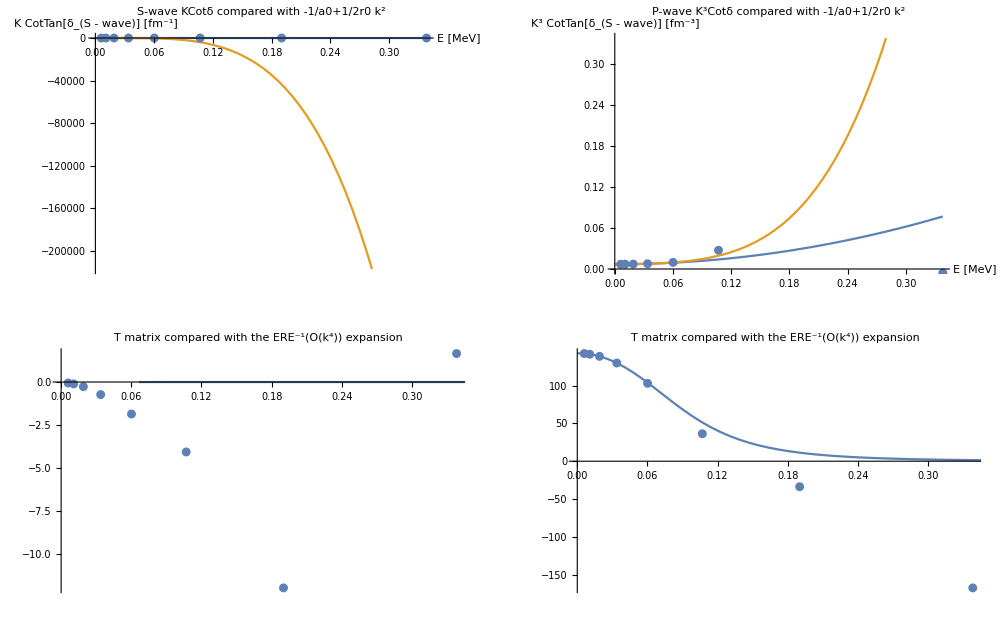

```mathematica
λλ=8;
mycore=core8;
rr=10;nGrid=50;
f1=1;f2=4; (* How many momenta should be used to make ere?*)

k0FMin=0.01;
k0FMax=0.3;
Divisions=8;



(*---------------------*)
ErangeMeV=N[findLogDivisions[{(k0FMin hbar)^2/(2 μ),(k0FMax hbar)^2/(2 μ)},Divisions]];
Erange1onfm=Sqrt[2 μ ErangeMeV]/hbar;

(*---------------------*)
nn=Flatten[Position[activeLEC⟦All,1⟧,_?(#==λλ&)]]⟦1⟧;
λ=0.25 activeLEC⟦nn⟧⟦1⟧^2;C0=activeLEC⟦nn⟧⟦2⟧;D0=activeLEC⟦nn⟧⟦3⟧;
Print["λ = Λ^2 = ",NumberForm[λ,nf],"  ⇒ Λ = ",NumberForm[2 Sqrt[λ],nf]," ; C_0 = ",NumberForm[C0,nf]," ; D_0 = ",NumberForm[D0,nf]];
Print["Core = ",mycore]
ERE8=GetERE[mycore];
Print["ERE = ","     a0 = ", ERE8⟦1⟧,"     r0 = ", ERE8⟦2⟧,"     a1 = ", ERE8⟦3⟧,"     r1 = ", ERE8⟦4⟧]
PlotERE
```

λ = Λ^2/4 = 25.0000  ⇒ Λ = 10.0000 ; C_0 = -2929.1700 ; D_0 = 92495

Core = {{0.160972,1.43173},{19.3369,0.216168},{-13.3195,0.217817},{-6.40798,0.217465},{-0.0671964,25.8862},{0.109986,4.3976},{0.694866,0.282318},{-0.181192,0.217221}}

ERE =      a0 = 0.0864212     r0 = 20271.     a1 = -142.833     r1 = 1.22695

(using more points and up to p^4)  a0 = 0.0629438  r0 = 93249.3   ω = -2.96968×10^7

S Pole Poitions in momentum: {-0.0327121-0.0000295311 ⅈ,-0.0223594+0.0000295311 ⅈ,0.0223594+0.0000295311 ⅈ,0.0327121-0.0000295311 ⅈ}

S Pole Poitions in energy:   {0.0295848+0.0000534161 ⅈ,0.013822-0.000036511 ⅈ,0.013822+0.000036511 ⅈ,0.0295848-0.0000534161 ⅈ}

(using more points and up to p^4)  a0 = -142.693  r0 = 1.11102   ω = 47.1761

P Pole Poitions in momentum: {-0.058602-0.0899657 ⅈ,-0.0526585+0.100564 ⅈ,0.0526585+0.100564 ⅈ,0.058602-0.0899657 ⅈ}

P Pole Poitions in energy:   {-0.128827+0.291523 ⅈ,-0.202939-0.292817 ⅈ,-0.202939+0.292817 ⅈ,-0.128827-0.291523 ⅈ}

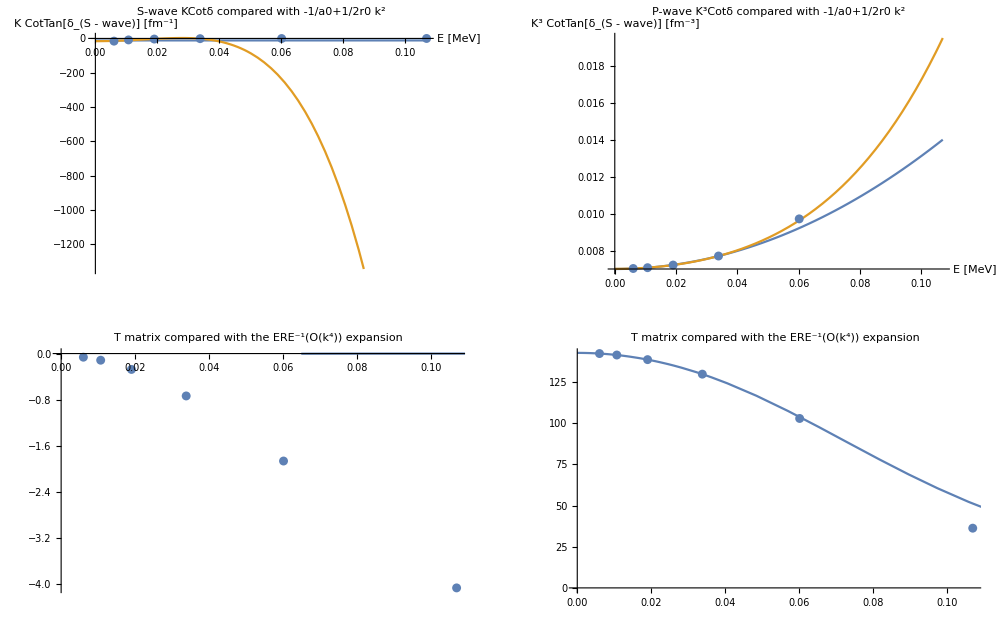

```mathematica
λλ=10;
mycore=core10;
rr=10;nGrid=50;
f1=1;f2=4; (* How many momenta should be used to make ere?*)

k0FMin=0.01;
k0FMax=0.3;
Divisions=8;


f1=1;f2=4; (* How many momenta should be used to make ere?*)
k0FMin=0.01;
k0FMax=0.1;
Divisions=4;

(*---------------------*)
ErangeMeV=N[findLogDivisions[{(k0FMin hbar)^2/(2 μ),(k0FMax hbar)^2/(2 μ)},Divisions]];
Erange1onfm=Sqrt[2 μ ErangeMeV]/hbar;

(*---------------------*)
nn=Flatten[Position[activeLEC⟦All,1⟧,_?(#==λλ&)]]⟦1⟧;
λ=0.25 activeLEC⟦nn⟧⟦1⟧^2;C0=activeLEC⟦nn⟧⟦2⟧;D0=activeLEC⟦nn⟧⟦3⟧;
Print["λ = Λ^2/4 = ",NumberForm[λ,nf],"  ⇒ Λ = ",NumberForm[2 Sqrt[λ],nf]," ; C_0 = ",NumberForm[C0,nf]," ; D_0 = ",NumberForm[D0,nf]];
Print["Core = ",mycore]
ERE10=GetERE[mycore];
Print["ERE = ","     a0 = ", ERE10⟦1⟧,"     r0 = ", ERE10⟦2⟧,"     a1 = ", ERE10⟦3⟧,"     r1 = ", ERE10⟦4⟧]
PlotERE
```

```mathematica
ERE1
ERE2
ERE3
ERE4
ERE6
ERE8
ERE10
```

{3.3665,38.8546,-158.126,1.04245}

{2.73081,67.3153,-147.772,1.16209}

{2.99815,51.5441,-145.681,1.19117}

{3.18554,43.0926,-143.999,1.21512}

{0.0720745,25040.1,-143.178,1.22242}

{0.0781169,22811.,-143.065,1.22389}

{0.0864212,20271.,-142.833,1.22695}

## Fit the core from the ERE parameters

```mathematica
(* I need a simple function to contain the fit*)
FitEre[x_?(VectorQ[#, NumericQ]&)]:=Module[{Aa0=x[[1]],Cc1=x[[2]],Aa1=x[[3]]},
mycore={{1.,Abs[Aa0]},{Cc1,Abs[Aa1]}};
ERE=GetERE[mycore];
a0tf=ERE⟦1⟧;
r0tf=ERE⟦2⟧;
a1tf=ERE⟦3⟧;
iIi=iIi+1;
Print["iter: ", iIi, "       core={1, ",Aa0,", ",Cc1,", ", Aa1"}     |     ERE = ", ERE  , "     |    to goal: ", {a0tf^-1,r0tf,a1tf^-1}-Goal ];
{a0tf^-1,r0tf,a1tf^-1}-Goal
]
```

```mathematica
(*Fit with 2 gaussians*)
nk=2;
core={}; Do[core=AppendTo[core,ToExpression@Map[StringJoin[#,ToString[k]]&,{"C","Α"}]],{k,1,nk}];
wf=Total[Flatten[Table[core⟦i⟧⟦1⟧ⅇ^(-core⟦i⟧⟦2⟧ r^2) ,{i,Length[core]}]]];

core4f=core/.FindFit[Mϕ4,wf,corefit,r];
wf4f   =Total[Flatten[Table[core4⟦i⟧⟦1⟧ⅇ^(-core4⟦i⟧⟦2⟧ r^2) ,{i,Length[core]}]]];
core6f=core/.FindFit[Mϕ6,wf,corefit,r];
wf6f   =Total[Flatten[Table[core6⟦i⟧⟦1⟧ⅇ^(-core6⟦i⟧⟦2⟧ r^2) ,{i,Length[core]}]]];

Print["wf4 = ", wf4f]
Print["wf6 = ", wf6f]
```

wf4 = -2.41128 ⅇ^(-0.674221 r^2)+0.178096 ⅇ^(-0.523946 r^2)

wf6 = -2.43227 ⅇ^(-0.792573 r^2)+0.214762 ⅇ^(-0.610935 r^2)

```mathematica
λλ=4;
rr=10;nGrid=20;
f1=1;f2=3; 
k0FMin=0.01;
k0FMax=0.1;
Divisions=3;
ErangeMeV=N[findLogDivisions[{(k0FMin hbar)^2/(2 μ),(k0FMax hbar)^2/(2 μ)},Divisions]];
Erange1onfm=Sqrt[2 μ ErangeMeV]/hbar;
nn=Flatten[Position[activeLEC⟦All,1⟧,_?(#==λλ&)]]⟦1⟧;
λ=0.25 activeLEC⟦nn⟧⟦1⟧^2;C0=activeLEC⟦nn⟧⟦2⟧;D0=activeLEC⟦nn⟧⟦3⟧;
Print["λ = Λ^2/4 = ",NumberForm[λ,nf],"  ⇒ Λ = ",NumberForm[2 Sqrt[λ],nf]," ; C_0 = ",NumberForm[C0,nf]," ; D_0 = ",NumberForm[D0,nf]];



(*--------run fit---------*)
iIi=0;
xini=Flatten[core4f]⟦;;3⟧;
FitEre[xini];
(*FitEre[{0.1,2.0,0.1}];*)


Goal={3.32^-1, 2.55,-20.23^-1};
CoreFitted4=FindRoot[FitEre[x]=={0,0,0},{x,xini},PrecisionGoal->4,AccuracyGoal->4]
```

λ = Λ^2/4 = 4.0000  ⇒ Λ = 4.0000 ; C_0 = -505.1500 ; D_0 = 1426.7500

iter: 1       core={1, 0.208715, 1.03031, 0.0699775 }     |     ERE = {1.428,186.12,508.773,-0.126987}     |    to goal: {0.399074,183.57,0.0513971}

iter: 2       core={1, 0.208715, 1.03031, 0.0699775 }     |     ERE = {1.428,186.12,508.773,-0.126987}     |    to goal: {0.399074,183.57,0.0513971}

iter: 3       core={1, 0.208715, 1.03031, 0.0699775 }     |     ERE = {1.428,186.12,508.773,-0.126987}     |    to goal: {0.399074,183.57,0.0513971}

iter: 4       core={1, 0.208715, 1.03031, 0.0699775 }     |     ERE = {1.428,186.12,508.773,-0.126987}     |    to goal: {0.399074,183.57,0.0513971}

iter: 5       core={1, 0.208715, 1.03031, 0.0699775 }     |     ERE = {1.428,186.12,508.773,-0.126987}     |    to goal: {0.399074,183.57,0.0513971}

iter: 6       core={1, 0.208715, 1.03031, 0.0699776 }     |     ERE = {1.428,186.12,508.773,-0.126987}     |    to goal: {0.399074,183.57,0.0513971}

iter: 7       core={1, 0.203531, -19.3949, -2.05666 }     |     ERE = {1.53227,164.542,522.281,-0.124462}     |    to goal: {0.351421,161.992,0.0513462}

iter: 8       core={1, 0.203531, -19.3949, -2.05666 }     |     ERE = {1.53227,164.542,522.281,-0.124462}     |    to goal: {0.351421,161.992,0.0513462}

iter: 9       core={1, 0.203531, -19.3949, -2.05666 }     |     ERE = {1.53227,164.542,522.281,-0.124462}     |    to goal: {0.351421,161.992,0.0513462}

iter: 10       core={1, 0.203531, -19.3949, -2.05666 }     |     ERE = {1.53227,164.542,522.281,-0.124462}     |    to goal: {0.351421,161.992,0.0513462}

iter: 11       core={1, 0.203531, -19.3949, -2.05666 }     |     ERE = {1.53227,164.542,522.281,-0.124462}     |    to goal: {0.351421,161.992,0.0513462}

iter: 12       core={1, 0.205302, -221.845, -34.5884 }     |     ERE = {0.825427,439.264,450.597,-0.1384}     |    to goal: {0.91029,436.714,0.0516508}

iter: 13       core={1, 0.203745, -43.8814, -5.99137 }     |     ERE = {1.36283,201.624,501.138,-0.128384}     |    to goal: {0.432561,199.074,0.051427}

iter: 14       core={1, 0.203638, -31.6382, -4.02401 }     |     ERE = {1.45754,179.661,512.561,-0.126245}     |    to goal: {0.384885,177.111,0.0513825}

iter: 15       core={1, 0.203585, -25.5165, -3.04034 }     |     ERE = {1.50489,169.878,518.642,-0.125125}     |    to goal: {0.363297,167.328,0.0513596}

iter: 16       core={1, 0.203558, -22.4557, -2.5485 }     |     ERE = {1.52363,166.201,521.123,-0.124672}     |    to goal: {0.355122,163.651,0.0513505}

iter: 17       core={1, 0.203545, -20.9253, -2.30258 }     |     ERE = {1.52981,165.012,521.95,-0.124522}     |    to goal: {0.352471,162.462,0.0513474}

iter: 18       core={1, 0.203538, -20.1601, -2.17962 }     |     ERE = {1.53161,164.668,522.192,-0.124478}     |    to goal: {0.351702,162.118,0.0513465}

iter: 19       core={1, 0.203535, -19.7775, -2.11814 }     |     ERE = {1.5321,164.574,522.258,-0.124466}     |    to goal: {0.351494,162.024,0.0513463}

iter: 20       core={1, 0.203533, -19.5862, -2.0874 }     |     ERE = {1.53223,164.55,522.275,-0.124463}     |    to goal: {0.351439,162.,0.0513462}

iter: 21       core={1, 0.203532, -19.4906, -2.07203 }     |     ERE = {1.53226,164.544,522.279,-0.124462}     |    to goal: {0.351426,161.994,0.0513462}

iter: 22       core={1, 0.203532, -19.4428, -2.06434 }     |     ERE = {1.53227,164.542,522.281,-0.124462}     |    to goal: {0.351422,161.992,0.0513462}

iter: 23       core={1, 0.203531, -19.4189, -2.0605 }     |     ERE = {1.53227,164.542,522.281,-0.124462}     |    to goal: {0.351421,161.992,0.0513462}

iter: 24       core={1, 0.203531, -19.4069, -2.05858 }     |     ERE = {1.53227,164.542,522.281,-0.124462}     |    to goal: {0.351421,161.992,0.0513462}

iter: 25       core={1, 0.203531, -19.4009, -2.05762 }     |     ERE = {1.53227,164.542,522.281,-0.124462}     |    to goal: {0.351421,161.992,0.0513462}

iter: 26       core={1, 0.203531, -19.3979, -2.05714 }     |     ERE = {1.53227,164.542,522.281,-0.124462}     |    to goal: {0.351421,161.992,0.0513462}

iter: 27       core={1, 0.203531, -19.3964, -2.0569 }     |     ERE = {1.53227,164.542,522.281,-0.124462}     |    to goal: {0.351421,161.992,0.0513462}

iter: 28       core={1, 0.203531, -19.3957, -2.05678 }     |     ERE = {1.53227,164.542,522.281,-0.124462}     |    to goal: {0.351421,161.992,0.0513462}

iter: 29       core={1, 0.203531, -19.3957, -2.05678 }     |     ERE = {1.53227,164.542,522.281,-0.124462}     |    to goal: {0.351421,161.992,0.0513462}

iter: 30       core={1, 0.203531, -19.3957, -2.05678 }     |     ERE = {1.53227,164.542,522.281,-0.124462}     |    to goal: {0.351421,161.992,0.0513462}

iter: 31       core={1, 0.203531, -19.3957, -2.05678 }     |     ERE = {1.53227,164.542,522.281,-0.124462}     |    to goal: {0.351421,161.992,0.0513462}

iter: 32       core={1, 0.203531, -19.3957, -2.05678 }     |     ERE = {1.53227,164.542,522.281,-0.124462}     |    to goal: {0.351421,161.992,0.0513462}

iter: 33       core={1, 0.204245, -221.858, -34.5625 }     |     ERE = {0.836158,431.192,451.445,-0.138221}     |    to goal: {0.894741,428.642,0.0516466}

iter: 34       core={1, 0.20362, -44.6981, -6.11912 }     |     ERE = {1.35843,202.732,500.632,-0.128479}     |    to goal: {0.43494,200.182,0.051429}

iter: 35       core={1, 0.203576, -32.0469, -4.08795 }     |     ERE = {1.45481,180.247,512.221,-0.126308}     |    to goal: {0.386169,177.697,0.0513838}

iter: 36       core={1, 0.203554, -25.7213, -3.07236 }     |     ERE = {1.50364,170.126,518.48,-0.125155}     |    to goal: {0.363848,167.576,0.0513603}

iter: 37       core={1, 0.203542, -22.5585, -2.56457 }     |     ERE = {1.52318,166.288,521.063,-0.124683}     |    to goal: {0.355316,163.738,0.0513507}

iter: 38       core={1, 0.203537, -20.9771, -2.31067 }     |     ERE = {1.52967,165.039,521.932,-0.124525}     |    to goal: {0.35253,162.489,0.0513475}

iter: 39       core={1, 0.203534, -20.1864, -2.18373 }     |     ERE = {1.53157,164.675,522.187,-0.124479}     |    to goal: {0.351719,162.125,0.0513466}

iter: 40       core={1, 0.203533, -19.791, -2.12025 }     |     ERE = {1.53209,164.576,522.257,-0.124466}     |    to goal: {0.351498,162.026,0.0513463}

iter: 41       core={1, 0.203532, -19.5934, -2.08852 }     |     ERE = {1.53223,164.551,522.275,-0.124463}     |    to goal: {0.351441,162.001,0.0513462}

iter: 42       core={1, 0.203532, -19.4945, -2.07265 }     |     ERE = {1.53226,164.544,522.279,-0.124462}     |    to goal: {0.351426,161.994,0.0513462}

iter: 43       core={1, 0.203531, -19.4451, -2.06471 }     |     ERE = {1.53227,164.542,522.281,-0.124462}     |    to goal: {0.351422,161.992,0.0513462}

iter: 44       core={1, 0.203531, -19.4204, -2.06075 }     |     ERE = {1.53227,164.542,522.281,-0.124462}     |    to goal: {0.351421,161.992,0.0513462}

iter: 45       core={1, 0.203531, -19.408, -2.05876 }     |     ERE = {1.53227,164.542,522.281,-0.124462}     |    to goal: {0.351421,161.992,0.0513462}

iter: 46       core={1, 0.203531, -19.4019, -2.05777 }     |     ERE = {1.53227,164.542,522.281,-0.124462}     |    to goal: {0.351421,161.992,0.0513462}

iter: 47       core={1, 0.203531, -19.3988, -2.05727 }     |     ERE = {1.53227,164.542,522.281,-0.124462}     |    to goal: {0.351421,161.992,0.0513462}

iter: 48       core={1, 0.203531, -19.3972, -2.05703 }     |     ERE = {1.53227,164.542,522.281,-0.124462}     |    to goal: {0.351421,161.992,0.0513462}

iter: 49       core={1, 0.203531, -19.3965, -2.0569 }     |     ERE = {1.53227,164.542,522.281,-0.124462}     |    to goal: {0.351421,161.992,0.0513462}

iter: 50       core={1, 0.203531, -19.3961, -2.05684 }     |     ERE = {1.53227,164.542,522.281,-0.124462}     |    to goal: {0.351421,161.992,0.0513462}

iter: 51       core={1, 0.203531, -19.3959, -2.05681 }     |     ERE = {1.53227,164.542,522.281,-0.124462}     |    to goal: {0.351421,161.992,0.0513462}

iter: 52       core={1, 0.203531, -19.3958, -2.05679 }     |     ERE = {1.53227,164.542,522.281,-0.124462}     |    to goal: {0.351421,161.992,0.0513462}

iter: 53       core={1, 0.203531, -19.3957, -2.05679 }     |     ERE = {1.53227,164.542,522.281,-0.124462}     |    to goal: {0.351421,161.992,0.0513462}

iter: 54       core={1, 0.203531, -19.3957, -2.05679 }     |     ERE = {1.53227,164.542,522.281,-0.124462}     |    to goal: {0.351421,161.992,0.0513462}

iter: 55       core={1, 0.203531, -19.3957, -2.05679 }     |     ERE = {1.53227,164.542,522.281,-0.124462}     |    to goal: {0.351421,161.992,0.0513462}

iter: 56       core={1, 0.203531, -19.3957, -2.05679 }     |     ERE = {1.53227,164.542,522.281,-0.124462}     |    to goal: {0.351421,161.992,0.0513462}

iter: 57       core={1, 0.203531, -19.3957, -2.05679 }     |     ERE = {1.53227,164.542,522.281,-0.124462}     |    to goal: {0.351421,161.992,0.0513462}

iter: 58       core={1, 0.200311, -221.875, -34.4599 }     |     ERE = {0.877849,401.856,454.789,-0.137515}     |    to goal: {0.837943,399.306,0.0516304}

iter: 59       core={1, 0.203076, -48.0102, -6.63602 }     |     ERE = {1.34187,206.975,498.748,-0.128832}     |    to goal: {0.444023,204.425,0.0514366}

iter: 60       core={1, 0.203304, -33.703, -4.3464 }     |     ERE = {1.4441,182.577,510.887,-0.126553}     |    to goal: {0.39127,180.027,0.0513889}

iter: 61       core={1, 0.203418, -26.5494, -3.20159 }     |     ERE = {1.49856,171.143,517.817,-0.125275}     |    to goal: {0.366101,168.593,0.0513627}

iter: 62       core={1, 0.203474, -22.9726, -2.62919 }     |     ERE = {1.5213,166.653,520.813,-0.124728}     |    to goal: {0.356128,164.103,0.0513516}

iter: 63       core={1, 0.203503, -21.1841, -2.34299 }     |     ERE = {1.52908,165.152,521.853,-0.124539}     |    to goal: {0.352782,162.602,0.0513478}

iter: 64       core={1, 0.203517, -20.2899, -2.19989 }     |     ERE = {1.53141,164.707,522.165,-0.124483}     |    to goal: {0.35179,162.157,0.0513466}

iter: 65       core={1, 0.203524, -19.8428, -2.12834 }     |     ERE = {1.53205,164.585,522.251,-0.124467}     |    to goal: {0.351517,162.035,0.0513463}

iter: 66       core={1, 0.203528, -19.6193, -2.09256 }     |     ERE = {1.53221,164.553,522.273,-0.124463}     |    to goal: {0.351446,162.003,0.0513462}

iter: 67       core={1, 0.203529, -19.5075, -2.07467 }     |     ERE = {1.53226,164.545,522.279,-0.124462}     |    to goal: {0.351427,161.995,0.0513462}

iter: 68       core={1, 0.20353, -19.4516, -2.06573 }     |     ERE = {1.53227,164.543,522.28,-0.124462}     |    to goal: {0.351423,161.993,0.0513462}

iter: 69       core={1, 0.203531, -19.4237, -2.06126 }     |     ERE = {1.53227,164.542,522.281,-0.124462}     |    to goal: {0.351421,161.992,0.0513462}

iter: 70       core={1, 0.203531, -19.4097, -2.05902 }     |     ERE = {1.53227,164.542,522.281,-0.124462}     |    to goal: {0.351421,161.992,0.0513462}

iter: 71       core={1, 0.203531, -19.4027, -2.0579 }     |     ERE = {1.53227,164.542,522.281,-0.124462}     |    to goal: {0.351421,161.992,0.0513462}

iter: 72       core={1, 0.203531, -19.3992, -2.05734 }     |     ERE = {1.53227,164.542,522.281,-0.124462}     |    to goal: {0.351421,161.992,0.0513462}

iter: 73       core={1, 0.203531, -19.3975, -2.05707 }     |     ERE = {1.53227,164.542,522.281,-0.124462}     |    to goal: {0.351421,161.992,0.0513462}

iter: 74       core={1, 0.203531, -19.3966, -2.05693 }     |     ERE = {1.53227,164.542,522.281,-0.124462}     |    to goal: {0.351421,161.992,0.0513462}

iter: 75       core={1, 0.203531, -19.3962, -2.05686 }     |     ERE = {1.53227,164.542,522.281,-0.124462}     |    to goal: {0.351421,161.992,0.0513462}

iter: 76       core={1, 0.203531, -19.396, -2.05682 }     |     ERE = {1.53227,164.542,522.281,-0.124462}     |    to goal: {0.351421,161.992,0.0513462}

iter: 77       core={1, 0.203531, -19.3959, -2.0568 }     |     ERE = {1.53227,164.542,522.281,-0.124462}     |    to goal: {0.351421,161.992,0.0513462}

iter: 78       core={1, 0.203531, -19.3958, -2.05679 }     |     ERE = {1.53227,164.542,522.281,-0.124462}     |    to goal: {0.351421,161.992,0.0513462}

iter: 79       core={1, 0.203531, -19.3958, -2.05679 }     |     ERE = {1.53227,164.542,522.281,-0.124462}     |    to goal: {0.351421,161.992,0.0513462}

iter: 80       core={1, 0.203531, -19.3958, -2.05679 }     |     ERE = {1.53227,164.542,522.281,-0.124462}     |    to goal: {0.351421,161.992,0.0513462}

iter: 81       core={1, 0.203531, -19.3957, -2.05679 }     |     ERE = {1.53227,164.542,522.281,-0.124462}     |    to goal: {0.351421,161.992,0.0513462}

iter: 82       core={1, 0.203531, -19.3957, -2.05679 }     |     ERE = {1.53227,164.542,522.281,-0.124462}     |    to goal: {0.351421,161.992,0.0513462}

iter: 83       core={1, 0.203531, -19.3957, -2.05679 }     |     ERE = {1.53227,164.542,522.281,-0.124462}     |    to goal: {0.351421,161.992,0.0513462}

iter: 84       core={1, 0.203531, -19.3957, -2.05679 }     |     ERE = {1.53227,164.542,522.281,-0.124462}     |    to goal: {0.351421,161.992,0.0513462}

iter: 85       core={1, 0.203531, -19.3957, -2.05679 }     |     ERE = {1.53227,164.542,522.281,-0.124462}     |    to goal: {0.351421,161.992,0.0513462}

iter: 86       core={1, 0.203531, -19.3957, -2.05679 }     |     ERE = {1.53227,164.542,522.281,-0.124462}     |    to goal: {0.351421,161.992,0.0513462}

iter: 87       core={1, 0.203531, -19.3957, -2.05679 }     |     ERE = {1.53227,164.542,522.281,-0.124462}     |    to goal: {0.351421,161.992,0.0513462}

iter: 88       core={1, 0.203531, -19.3957, -2.05679 }     |     ERE = {1.53227,164.542,522.281,-0.124462}     |    to goal: {0.351421,161.992,0.0513462}

iter: 89       core={1, 0.203531, -19.3957, -2.05679 }     |     ERE = {1.53227,164.542,522.281,-0.124462}     |    to goal: {0.351421,161.992,0.0513462}

iter: 90       core={1, 0.203531, -19.3957, -2.05679 }     |     ERE = {1.53227,164.542,522.281,-0.124462}     |    to goal: {0.351421,161.992,0.0513462}

iter: 91       core={1, 0.203531, -19.3957, -2.05679 }     |     ERE = {1.53227,164.542,522.281,-0.124462}     |    to goal: {0.351421,161.992,0.0513462}

iter: 92       core={1, 0.203531, -19.3957, -2.05679 }     |     ERE = {1.53227,164.542,522.281,-0.124462}     |    to goal: {0.351421,161.992,0.0513462}

iter: 93       core={1, 0.203531, -19.3957, -2.05679 }     |     ERE = {1.53227,164.542,522.281,-0.124462}     |    to goal: {0.351421,161.992,0.0513462}

iter: 94       core={1, 0.205896, 183.08, 30.3686 }     |     ERE = {0.900063,387.386,456.419,-0.137206}     |    to goal: {0.809828,384.836,0.0516225}

iter: 95       core={1, 0.203887, 11.0805, 2.82382 }     |     ERE = {2.39446,68.2441,715.13,-0.0954882}     |    to goal: {0.116426,65.6941,0.0508299}

iter: 96       core={1, 0.203887, 11.0805, 2.82382 }     |     ERE = {2.39446,68.2441,715.13,-0.0954882}     |    to goal: {0.116426,65.6941,0.0508299}

iter: 97       core={1, 0.203887, 11.0805, 2.82382 }     |     ERE = {2.39446,68.2441,715.13,-0.0954883}     |    to goal: {0.116426,65.6941,0.0508299}

iter: 98       core={1, 0.203887, 11.0805, 2.82382 }     |     ERE = {2.39446,68.2441,715.13,-0.0954883}     |    to goal: {0.116426,65.6941,0.0508299}

iter: 99       core={1, 0.203887, 11.0805, 2.82382 }     |     ERE = {2.39446,68.2441,715.13,-0.0954882}     |    to goal: {0.116426,65.6941,0.0508299}

iter: 100       core={1, 0.205066, 130.43, 37.7841 }     |     ERE = {1.70564,135.401,547.648,-0.119982}     |    to goal: {0.285087,132.851,0.0512575}

iter: 101       core={1, 0.204119, 34.5302, 9.6928 }     |     ERE = {2.2098,81.108,655.043,-0.103329}     |    to goal: {0.151326,78.558,0.0509582}

iter: 102       core={1, 0.204003, 22.8053, 6.25831 }     |     ERE = {2.31436,73.4924,687.105,-0.0990273}     |    to goal: {0.13088,70.9424,0.0508869}

iter: 103       core={1, 0.203945, 16.9429, 4.54107 }     |     ERE = {2.36518,70.1077,704.503,-0.0968072}     |    to goal: {0.121596,67.5577,0.050851}

iter: 104       core={1, 0.203916, 14.0117, 3.68244 }     |     ERE = {2.38519,68.8279,711.716,-0.0959091}     |    to goal: {0.11805,66.2779,0.0508366}

iter: 105       core={1, 0.203902, 12.5461, 3.25313 }     |     ERE = {2.3918,68.4106,714.15,-0.0956089}     |    to goal: {0.116889,65.8606,0.0508318}

iter: 106       core={1, 0.203894, 11.8133, 3.03848 }     |     ERE = {2.39375,68.2889,714.867,-0.0955206}     |    to goal: {0.11655,65.7389,0.0508304}

iter: 107       core={1, 0.203891, 11.4469, 2.93115 }     |     ERE = {2.39428,68.2557,715.062,-0.0954966}     |    to goal: {0.116458,65.7057,0.05083}

iter: 108       core={1, 0.203889, 11.2637, 2.87749 }     |     ERE = {2.39441,68.2471,715.113,-0.0954903}     |    to goal: {0.116434,65.6971,0.0508299}

iter: 109       core={1, 0.203888, 11.1721, 2.85065 }     |     ERE = {2.39445,68.2449,715.126,-0.0954888}     |    to goal: {0.116428,65.6949,0.0508299}

iter: 110       core={1, 0.203888, 11.1263, 2.83724 }     |     ERE = {2.39446,68.2443,715.129,-0.0954884}     |    to goal: {0.116426,65.6943,0.0508299}

iter: 111       core={1, 0.203887, 11.1034, 2.83053 }     |     ERE = {2.39446,68.2442,715.13,-0.0954883}     |    to goal: {0.116426,65.6942,0.0508299}

iter: 112       core={1, 0.203887, 11.0919, 2.82718 }     |     ERE = {2.39446,68.2441,715.13,-0.0954883}     |    to goal: {0.116426,65.6941,0.0508299}

iter: 113       core={1, 0.203887, 11.0862, 2.8255 }     |     ERE = {2.39446,68.2441,715.13,-0.0954882}     |    to goal: {0.116426,65.6941,0.0508299}

iter: 114       core={1, 0.203887, 11.0833, 2.82466 }     |     ERE = {2.39446,68.2441,715.13,-0.0954882}     |    to goal: {0.116426,65.6941,0.0508299}

iter: 115       core={1, 0.203887, 11.0819, 2.82424 }     |     ERE = {2.39446,68.2441,715.13,-0.0954882}     |    to goal: {0.116426,65.6941,0.0508299}

iter: 116       core={1, 0.203887, 11.0812, 2.82403 }     |     ERE = {2.39446,68.2441,715.13,-0.0954882}     |    to goal: {0.116426,65.6941,0.0508299}

iter: 117       core={1, 0.203887, 11.0808, 2.82393 }     |     ERE = {2.39446,68.2441,715.13,-0.0954882}     |    to goal: {0.116426,65.6941,0.0508299}

iter: 118       core={1, 0.203887, 11.0806, 2.82387 }     |     ERE = {2.39446,68.2441,715.13,-0.0954882}     |    to goal: {0.116426,65.6941,0.0508299}

iter: 119       core={1, 0.203887, 11.0806, 2.82385 }     |     ERE = {2.39446,68.2441,715.13,-0.0954882}     |    to goal: {0.116426,65.6941,0.0508299}

iter: 120       core={1, 0.203887, 11.0806, 2.82385 }     |     ERE = {2.39446,68.2441,715.13,-0.0954882}     |    to goal: {0.116426,65.6941,0.0508299}

iter: 121       core={1, 0.203887, 11.0806, 2.82385 }     |     ERE = {2.39446,68.2441,715.13,-0.0954883}     |    to goal: {0.116426,65.6941,0.0508299}

iter: 122       core={1, 0.203887, 11.0806, 2.82385 }     |     ERE = {2.39446,68.2441,715.13,-0.0954883}     |    to goal: {0.116426,65.6941,0.0508299}

iter: 123       core={1, 0.203887, 11.0806, 2.82385 }     |     ERE = {2.39446,68.2441,715.13,-0.0954882}     |    to goal: {0.116426,65.6941,0.0508299}

iter: 124       core={1, 0.205394, -108.302, -32.0265 }     |     ERE = {1.90522,109.615,582.99,-0.114099}     |    to goal: {0.223668,107.065,0.0511468}

iter: 125       core={1, 0.204299, -21.5726, -6.70832 }     |     ERE = {2.91751,43.1741,1040.92,-0.065506}     |    to goal: {0.0415533,40.6241,0.0503922}

iter: 126       core={1, 0.204299, -21.5726, -6.70832 }     |     ERE = {2.91751,43.1741,1040.92,-0.065506}     |    to goal: {0.0415533,40.6241,0.0503922}

iter: 127       core={1, 0.204299, -21.5726, -6.70832 }     |     ERE = {2.91751,43.1741,1040.92,-0.0655061}     |    to goal: {0.0415534,40.6241,0.0503922}

iter: 128       core={1, 0.204299, -21.5726, -6.70832 }     |     ERE = {2.91751,43.1741,1040.92,-0.065506}     |    to goal: {0.0415533,40.6241,0.0503922}

iter: 129       core={1, 0.204299, -21.5726, -6.70832 }     |     ERE = {2.91751,43.1741,1040.92,-0.065506}     |    to goal: {0.0415533,40.6241,0.0503922}

iter: 130       core={1, 0.20481, -234.303, -108.721 }     |     ERE = {2.16532,84.6373,642.835,-0.105049}     |    to goal: {0.160622,82.0873,0.0509871}

iter: 131       core={1, 0.2044, -63.4234, -26.7773 }     |     ERE = {2.69647,52.1246,861.825,-0.0798139}     |    to goal: {0.069651,49.5746,0.0505919}

iter: 132       core={1, 0.20435, -42.498, -16.7428 }     |     ERE = {2.81462,47.0907,946.412,-0.0725137}     |    to goal: {0.0540825,44.5407,0.0504882}

iter: 133       core={1, 0.204324, -32.0353, -11.7256 }     |     ERE = {2.87703,44.6668,1000.92,-0.0683399}     |    to goal: {0.0463757,42.1168,0.0504306}

iter: 134       core={1, 0.204312, -26.804, -9.21695 }     |     ERE = {2.90387,43.6702,1027.,-0.0664718}     |    to goal: {0.043163,41.1202,0.0504053}

iter: 135       core={1, 0.204306, -24.1883, -7.96263 }     |     ERE = {2.91343,43.3216,1036.71,-0.0657955}     |    to goal: {0.0420327,40.7716,0.0503961}

iter: 136       core={1, 0.204302, -22.8805, -7.33547 }     |     ERE = {2.91638,43.2147,1039.75,-0.0655859}     |    to goal: {0.0416855,40.6647,0.0503933}

iter: 137       core={1, 0.204301, -22.2265, -7.0219 }     |     ERE = {2.91721,43.1848,1040.61,-0.065527}     |    to goal: {0.0415881,40.6348,0.0503925}

iter: 138       core={1, 0.2043, -21.8996, -6.86511 }     |     ERE = {2.91743,43.1768,1040.84,-0.0655114}     |    to goal: {0.0415623,40.6268,0.0503923}

iter: 139       core={1, 0.2043, -21.7361, -6.78671 }     |     ERE = {2.91749,43.1747,1040.9,-0.0655074}     |    to goal: {0.0415556,40.6247,0.0503922}

iter: 140       core={1, 0.204299, -21.6544, -6.74751 }     |     ERE = {2.9175,43.1742,1040.91,-0.0655064}     |    to goal: {0.0415539,40.6242,0.0503922}

iter: 141       core={1, 0.204299, -21.6135, -6.72792 }     |     ERE = {2.91751,43.1741,1040.92,-0.0655061}     |    to goal: {0.0415535,40.6241,0.0503922}

iter: 142       core={1, 0.204299, -21.5931, -6.71812 }     |     ERE = {2.91751,43.1741,1040.92,-0.0655061}     |    to goal: {0.0415534,40.6241,0.0503922}

iter: 143       core={1, 0.204299, -21.5828, -6.71322 }     |     ERE = {2.91751,43.1741,1040.92,-0.065506}     |    to goal: {0.0415533,40.6241,0.0503922}

iter: 144       core={1, 0.204299, -21.5777, -6.71077 }     |     ERE = {2.91751,43.1741,1040.92,-0.065506}     |    to goal: {0.0415533,40.6241,0.0503922}

iter: 145       core={1, 0.204299, -21.5752, -6.70954 }     |     ERE = {2.91751,43.1741,1040.92,-0.065506}     |    to goal: {0.0415533,40.6241,0.0503922}

iter: 146       core={1, 0.204299, -21.5739, -6.70893 }     |     ERE = {2.91751,43.1741,1040.92,-0.065506}     |    to goal: {0.0415533,40.6241,0.0503922}

iter: 147       core={1, 0.204299, -21.5733, -6.70862 }     |     ERE = {2.91751,43.1741,1040.92,-0.065506}     |    to goal: {0.0415533,40.6241,0.0503922}

iter: 148       core={1, 0.204299, -21.5729, -6.70847 }     |     ERE = {2.91751,43.1741,1040.92,-0.065506}     |    to goal: {0.0415533,40.6241,0.0503922}

iter: 149       core={1, 0.204299, -21.5728, -6.70839 }     |     ERE = {2.91751,43.1741,1040.92,-0.065506}     |    to goal: {0.0415533,40.6241,0.0503922}

iter: 150       core={1, 0.204299, -21.5727, -6.70836 }     |     ERE = {2.91751,43.1741,1040.92,-0.065506}     |    to goal: {0.0415533,40.6241,0.0503922}

iter: 151       core={1, 0.204299, -21.5727, -6.70834 }     |     ERE = {2.91751,43.1741,1040.92,-0.065506}     |    to goal: {0.0415533,40.6241,0.0503922}

iter: 152       core={1, 0.204299, -21.5727, -6.70833 }     |     ERE = {2.91751,43.1741,1040.92,-0.065506}     |    to goal: {0.0415533,40.6241,0.0503922}

iter: 153       core={1, 0.204299, -21.5726, -6.70832 }     |     ERE = {2.91751,43.1741,1040.92,-0.065506}     |    to goal: {0.0415533,40.6241,0.0503922}

iter: 154       core={1, 0.204299, -21.5726, -6.70832 }     |     ERE = {2.91751,43.1741,1040.92,-0.065506}     |    to goal: {0.0415533,40.6241,0.0503922}

iter: 155       core={1, 0.204299, -21.5726, -6.70832 }     |     ERE = {2.91751,43.1741,1040.92,-0.065506}     |    to goal: {0.0415533,40.6241,0.0503922}

iter: 156       core={1, 0.204299, -21.5726, -6.70832 }     |     ERE = {2.91751,43.1741,1040.92,-0.065506}     |    to goal: {0.0415533,40.6241,0.0503922}

iter: 157       core={1, 0.204299, -21.5726, -6.70832 }     |     ERE = {2.91751,43.1741,1040.92,-0.065506}     |    to goal: {0.0415533,40.6241,0.0503922}

iter: 158       core={1, 0.204299, -21.5726, -6.70832 }     |     ERE = {2.91751,43.1741,1040.92,-0.065506}     |    to goal: {0.0415533,40.6241,0.0503922}

iter: 159       core={1, 0.204299, -21.5726, -6.70832 }     |     ERE = {2.91751,43.1741,1040.92,-0.065506}     |    to goal: {0.0415533,40.6241,0.0503922}

iter: 160       core={1, 0.204299, -21.5726, -6.70832 }     |     ERE = {2.91751,43.1741,1040.92,-0.065506}     |    to goal: {0.0415533,40.6241,0.0503922}

iter: 161       core={1, 0.204299, -21.5726, -6.70832 }     |     ERE = {2.91751,43.1741,1040.92,-0.065506}     |    to goal: {0.0415533,40.6241,0.0503922}

iter: 162       core={1, 0.204299, -21.5726, -6.70832 }     |     ERE = {2.91751,43.1741,1040.92,-0.065506}     |    to goal: {0.0415533,40.6241,0.0503922}

iter: 163       core={1, 0.204299, -21.5726, -6.70832 }     |     ERE = {2.91751,43.1741,1040.92,-0.065506}     |    to goal: {0.0415533,40.6241,0.0503922}

iter: 164       core={1, 0.204299, -21.5726, -6.70832 }     |     ERE = {2.91751,43.1741,1040.92,-0.0655061}     |    to goal: {0.0415534,40.6241,0.0503922}

iter: 165       core={1, 0.204299, -21.5726, -6.70832 }     |     ERE = {2.91751,43.1741,1040.92,-0.065506}     |    to goal: {0.0415533,40.6241,0.0503922}

iter: 166       core={1, 0.204299, -21.5726, -6.70832 }     |     ERE = {2.91751,43.1741,1040.92,-0.065506}     |    to goal: {0.0415533,40.6241,0.0503922}

iter: 167       core={1, 0.205195, -234.284, -108.76 }     |     ERE = {2.15799,85.2351,640.933,-0.105324}     |    to goal: {0.162189,82.6851,0.0509918}

iter: 168       core={1, 0.204473, -62.9341, -26.5521 }     |     ERE = {2.69786,52.0611,862.782,-0.0797261}     |    to goal: {0.0694589,49.5111,0.0505906}

iter: 169       core={1, 0.204386, -42.2533, -16.6302 }     |     ERE = {2.81564,47.0499,947.292,-0.0724438}     |    to goal: {0.0539544,44.4999,0.0504872}

iter: 170       core={1, 0.204343, -31.913, -11.6693 }     |     ERE = {2.87756,44.6468,1001.45,-0.0683013}     |    to goal: {0.0463118,42.0968,0.0504301}

iter: 171       core={1, 0.204321, -26.7428, -9.18879 }     |     ERE = {2.90408,43.6624,1027.23,-0.0664557}     |    to goal: {0.0431377,41.1124,0.050405}

iter: 172       core={1, 0.20431, -24.1577, -7.94855 }     |     ERE = {2.91351,43.319,1036.79,-0.0657899}     |    to goal: {0.0420244,40.769,0.050396}

iter: 173       core={1, 0.204305, -22.8652, -7.32844 }     |     ERE = {2.91641,43.2139,1039.78,-0.0655841}     |    to goal: {0.0416831,40.6639,0.0503933}

iter: 174       core={1, 0.204302, -22.2189, -7.01838 }     |     ERE = {2.91722,43.1845,1040.62,-0.0655264}     |    to goal: {0.0415875,40.6345,0.0503925}

iter: 175       core={1, 0.204301, -21.8958, -6.86335 }     |     ERE = {2.91743,43.1767,1040.84,-0.0655112}     |    to goal: {0.0415621,40.6267,0.0503923}

iter: 176       core={1, 0.2043, -21.7342, -6.78583 }     |     ERE = {2.91749,43.1747,1040.9,-0.0655073}     |    to goal: {0.0415555,40.6247,0.0503922}

iter: 177       core={1, 0.2043, -21.6534, -6.74707 }     |     ERE = {2.9175,43.1742,1040.91,-0.0655063}     |    to goal: {0.0415539,40.6242,0.0503922}

iter: 178       core={1, 0.204299, -21.613, -6.7277 }     |     ERE = {2.91751,43.1741,1040.92,-0.0655061}     |    to goal: {0.0415535,40.6241,0.0503922}

iter: 179       core={1, 0.204299, -21.5928, -6.71801 }     |     ERE = {2.91751,43.1741,1040.92,-0.0655061}     |    to goal: {0.0415534,40.6241,0.0503922}

iter: 180       core={1, 0.204299, -21.5827, -6.71316 }     |     ERE = {2.91751,43.1741,1040.92,-0.065506}     |    to goal: {0.0415533,40.6241,0.0503922}

iter: 181       core={1, 0.204299, -21.5777, -6.71074 }     |     ERE = {2.91751,43.1741,1040.92,-0.065506}     |    to goal: {0.0415533,40.6241,0.0503922}

iter: 182       core={1, 0.204299, -21.5752, -6.70953 }     |     ERE = {2.91751,43.1741,1040.92,-0.065506}     |    to goal: {0.0415533,40.6241,0.0503922}

iter: 183       core={1, 0.204299, -21.5739, -6.70892 }     |     ERE = {2.91751,43.1741,1040.92,-0.065506}     |    to goal: {0.0415533,40.6241,0.0503922}

iter: 184       core={1, 0.204299, -21.5733, -6.70862 }     |     ERE = {2.91751,43.1741,1040.92,-0.065506}     |    to goal: {0.0415533,40.6241,0.0503922}

iter: 185       core={1, 0.204299, -21.5729, -6.70847 }     |     ERE = {2.91751,43.1741,1040.92,-0.065506}     |    to goal: {0.0415533,40.6241,0.0503922}

iter: 186       core={1, 0.204299, -21.5729, -6.70847 }     |     ERE = {2.91751,43.1741,1040.92,-0.065506}     |    to goal: {0.0415533,40.6241,0.0503922}

iter: 187       core={1, 0.204299, -21.5729, -6.70847 }     |     ERE = {2.91751,43.1741,1040.92,-0.0655061}     |    to goal: {0.0415534,40.6241,0.0503922}

iter: 188       core={1, 0.204299, -21.5729, -6.70847 }     |     ERE = {2.91751,43.1741,1040.92,-0.065506}     |    to goal: {0.0415533,40.6241,0.0503922}

iter: 189       core={1, 0.204299, -21.5729, -6.70847 }     |     ERE = {2.91751,43.1741,1040.92,-0.065506}     |    to goal: {0.0415533,40.6241,0.0503922}

iter: 190       core={1, 0.208562, 191.393, 94.8181 }     |     ERE = {2.2246,79.9508,660.163,-0.102676}     |    to goal: {0.148315,77.4008,0.0509463}

iter: 191       core={1, 0.20522, 24.4226, 15.2188 }     |     ERE = {3.22021,33.7074,1562.68,-0.0402903}     |    to goal: {0.00933372,31.1574,0.0500715}

iter: 192       core={1, 0.20522, 24.4226, 15.2188 }     |     ERE = {3.22021,33.7074,1562.68,-0.0402903}     |    to goal: {0.00933372,31.1574,0.0500715}

iter: 193       core={1, 0.20522, 24.4226, 15.2188 }     |     ERE = {3.22021,33.7074,1562.68,-0.0402903}     |    to goal: {0.00933375,31.1574,0.0500715}

iter: 194       core={1, 0.20522, 24.4226, 15.2188 }     |     ERE = {3.22021,33.7074,1562.68,-0.0402903}     |    to goal: {0.00933373,31.1574,0.0500715}

iter: 195       core={1, 0.20522, 24.4226, 15.2188 }     |     ERE = {3.22021,33.7074,1562.68,-0.0402903}     |    to goal: {0.00933372,31.1574,0.0500715}

iter: 196       core={1, 0.206474, -213.335, -164.052 }     |     ERE = {2.83473,46.2844,966.442,-0.0709648}     |    to goal: {0.0515626,43.7344,0.0504663}

iter: 197       core={1, 0.205642, -55.6235, -45.1366 }     |     ERE = {3.36651,30.0305,2165.37,-0.0250756}     |    to goal: {-0.00416143,27.4805,0.0498934}

iter: 198       core={1, 0.205642, -55.6235, -45.1366 }     |     ERE = {3.36651,30.0305,2165.37,-0.0250756}     |    to goal: {-0.00416143,27.4805,0.0498934}

iter: 199       core={1, 0.205642, -55.6235, -45.1366 }     |     ERE = {3.36651,30.0305,2165.37,-0.0250756}     |    to goal: {-0.00416141,27.4805,0.0498934}

iter: 200       core={1, 0.205642, -55.6235, -45.1366 }     |     ERE = {3.36651,30.0305,2165.37,-0.0250756}     |    to goal: {-0.00416144,27.4805,0.0498934}

iter: 201       core={1, 0.205642, -55.6235, -45.1366 }     |     ERE = {3.36651,30.0305,2165.37,-0.0250756}     |    to goal: {-0.00416143,27.4805,0.0498934}

iter: 202       core={1, 0.211579, 426.383, 498.214 }     |     ERE = {2.90727,43.5183,1044.92,-0.0653291}     |    to goal: {0.0427602,40.9683,0.0503886}

iter: 203       core={1, 0.207484, 93.9504, 123.473 }     |     ERE = {3.45933,27.9423,3007.34,-0.013497}     |    to goal: {-0.0121316,25.3923,0.0497641}

iter: 204       core={1, 0.207484, 93.9504, 123.473 }     |     ERE = {3.45933,27.9423,3007.34,-0.013497}     |    to goal: {-0.0121316,25.3923,0.0497641}

iter: 205       core={1, 0.207484, 93.9504, 123.473 }     |     ERE = {3.45933,27.9423,3007.34,-0.013497}     |    to goal: {-0.0121316,25.3923,0.0497641}

iter: 206       core={1, 0.207484, 93.9504, 123.473 }     |     ERE = {3.45933,27.9423,3007.34,-0.013497}     |    to goal: {-0.0121316,25.3923,0.0497641}

iter: 207       core={1, 0.207484, 93.9504, 123.473 }     |     ERE = {3.45933,27.9423,3007.34,-0.013497}     |    to goal: {-0.0121316,25.3923,0.0497641}

iter: 208       core={1, 0.220253, -718.224, -1210.22 }     |     ERE = {2.94355,42.1889,1104.62,-0.0615488}     |    to goal: {0.0385214,39.6389,0.0503368}

iter: 209       core={1, 0.2112, -142.36, -264.579 }     |     ERE = {3.53155,26.4325,4680.18,-0.00245455}     |    to goal: {-0.0180434,23.8825,0.0496452}

iter: 210       core={1, 0.2112, -142.36, -264.579 }     |     ERE = {3.53155,26.4325,4680.18,-0.00245455}     |    to goal: {-0.0180434,23.8825,0.0496452}

iter: 211       core={1, 0.2112, -142.36, -264.579 }     |     ERE = {3.53155,26.4325,4680.17,-0.00245458}     |    to goal: {-0.0180434,23.8825,0.0496452}

iter: 212       core={1, 0.2112, -142.36, -264.579 }     |     ERE = {3.53155,26.4325,4680.18,-0.00245455}     |    to goal: {-0.0180434,23.8825,0.0496452}

iter: 213       core={1, 0.2112, -142.36, -264.579 }     |     ERE = {3.53155,26.4325,4680.18,-0.00245455}     |    to goal: {-0.0180434,23.8825,0.0496452}

iter: 214       core={1, 0.21145, 966.927, 2538.37 }     |     ERE = {3.35773,30.2203,2219.81,-0.0241417}     |    to goal: {-0.00338459,27.6703,0.049882}

iter: 215       core={1, 0.211307, 331.217, 932.058 }     |     ERE = {3.56823,25.7081,6278.03,0.00274607}     |    to goal: {-0.0209537,23.1581,0.0495908}

iter: 216       core={1, 0.211307, 331.217, 932.058 }     |     ERE = {3.56823,25.7081,6278.03,0.00274607}     |    to goal: {-0.0209537,23.1581,0.0495908}

iter: 217       core={1, 0.211307, 331.217, 932.058 }     |     ERE = {3.56823,25.7081,6278.01,0.00274604}     |    to goal: {-0.0209536,23.1581,0.0495908}

iter: 218       core={1, 0.211307, 331.217, 932.058 }     |     ERE = {3.56823,25.7081,6278.03,0.00274607}     |    to goal: {-0.0209537,23.1581,0.0495908}

iter: 219       core={1, 0.211307, 331.217, 932.058 }     |     ERE = {3.56823,25.7081,6278.03,0.00274607}     |    to goal: {-0.0209537,23.1581,0.0495908}

iter: 220       core={1, 0.215407, -2280.53, -8618.87 }     |     ERE = {3.33898,30.6563,2174.07,-0.0250179}     |    to goal: {-0.00171203,28.1063,0.0498915}

iter: 221       core={1, 0.212965, -724.895, -2930.05 }     |     ERE = {3.58289,25.4216,7786.81,0.00572354}     |    to goal: {-0.0221006,22.8716,0.04956}

iter: 222       core={1, 0.212965, -724.895, -2930.05 }     |     ERE = {3.58289,25.4216,7786.81,0.00572354}     |    to goal: {-0.0221006,22.8716,0.04956}

iter: 223       core={1, 0.212965, -724.895, -2930.05 }     |     ERE = {3.58289,25.4216,7786.79,0.00572351}     |    to goal: {-0.0221006,22.8716,0.04956}

iter: 224       core={1, 0.212965, -724.895, -2930.05 }     |     ERE = {3.58289,25.4216,7786.81,0.00572354}     |    to goal: {-0.0221006,22.8716,0.04956}

iter: 225       core={1, 0.212965, -724.895, -2930.05 }     |     ERE = {3.58289,25.4216,7786.81,0.00572354}     |    to goal: {-0.0221006,22.8716,0.04956}

iter: 226       core={1, 0.214598, -6170.87, -32628.7 }     |     ERE = {3.35466,30.2845,2259.76,-0.0234701}     |    to goal: {-0.0031119,27.7345,0.0498741}

iter: 227       core={1, 0.213626, -2929.36, -14951.7 }     |     ERE = {3.48047,27.4772,3633.36,-0.00826349}     |    to goal: {-0.0138869,24.9272,0.0497068}

iter: 228       core={1, 0.213295, -1827.13, -8940.88 }     |     ERE = {3.53433,26.3718,5022.18,-0.00108762}     |    to goal: {-0.0182661,23.8218,0.0496307}

iter: 229       core={1, 0.21313, -1276.01, -5935.46 }     |     ERE = {3.56295,25.8066,6346.79,0.00289898}     |    to goal: {-0.0205387,23.2566,0.0495891}

iter: 230       core={1, 0.213047, -1000.45, -4432.76 }     |     ERE = {3.57584,25.5569,7212.99,0.00473027}     |    to goal: {-0.0215502,23.0069,0.0495702}

iter: 231       core={1, 0.213006, -862.674, -3681.4 }     |     ERE = {3.5807,25.4636,7603.43,0.005422}     |    to goal: {-0.0219297,22.9136,0.0495631}

iter: 232       core={1, 0.212985, -793.784, -3305.72 }     |     ERE = {3.58227,25.4335,7736.79,0.00564261}     |    to goal: {-0.0220521,22.8835,0.0495608}

iter: 233       core={1, 0.212975, -759.339, -3117.89 }     |     ERE = {3.58272,25.4248,7774.92,0.00570435}     |    to goal: {-0.0220876,22.8748,0.0495602}

iter: 234       core={1, 0.21297, -742.117, -3023.97 }     |     ERE = {3.58285,25.4225,7784.53,0.00571985}     |    to goal: {-0.0220972,22.8725,0.04956}

iter: 235       core={1, 0.212967, -733.506, -2977.01 }     |     ERE = {3.58288,25.4218,7786.64,0.00572325}     |    to goal: {-0.0220997,22.8718,0.04956}

iter: 236       core={1, 0.212966, -729.2, -2953.53 }     |     ERE = {3.58289,25.4217,7786.98,0.0057238}     |    to goal: {-0.0221004,22.8717,0.04956}

iter: 237       core={1, 0.212965, -727.047, -2941.79 }     |     ERE = {3.58289,25.4217,7786.96,0.00572377}     |    to goal: {-0.0221005,22.8717,0.04956}

iter: 238       core={1, 0.212965, -725.971, -2935.92 }     |     ERE = {3.58289,25.4216,7786.9,0.00572368}     |    to goal: {-0.0221006,22.8716,0.04956}

iter: 239       core={1, 0.212965, -725.433, -2932.98 }     |     ERE = {3.58289,25.4216,7786.86,0.00572362}     |    to goal: {-0.0221006,22.8716,0.04956}

iter: 240       core={1, 0.212965, -725.164, -2931.52 }     |     ERE = {3.58289,25.4216,7786.84,0.00572358}     |    to goal: {-0.0221006,22.8716,0.04956}

iter: 241       core={1, 0.212965, -725.029, -2930.78 }     |     ERE = {3.58289,25.4216,7786.82,0.00572356}     |    to goal: {-0.0221006,22.8716,0.04956}

iter: 242       core={1, 0.212965, -724.962, -2930.41 }     |     ERE = {3.58289,25.4216,7786.82,0.00572355}     |    to goal: {-0.0221006,22.8716,0.04956}

iter: 243       core={1, 0.212965, -724.928, -2930.23 }     |     ERE = {3.58289,25.4216,7786.82,0.00572355}     |    to goal: {-0.0221006,22.8716,0.04956}

iter: 244       core={1, 0.212965, -724.911, -2930.14 }     |     ERE = {3.58289,25.4216,7786.81,0.00572354}     |    to goal: {-0.0221006,22.8716,0.04956}

iter: 245       core={1, 0.212965, -724.911, -2930.14 }     |     ERE = {3.58289,25.4216,7786.81,0.00572354}     |    to goal: {-0.0221006,22.8716,0.04956}

iter: 246       core={1, 0.212965, -724.911, -2930.14 }     |     ERE = {3.58289,25.4216,7786.8,0.00572352}     |    to goal: {-0.0221006,22.8716,0.04956}

iter: 247       core={1, 0.212965, -724.911, -2930.14 }     |     ERE = {3.58289,25.4216,7786.81,0.00572354}     |    to goal: {-0.0221006,22.8716,0.04956}

iter: 248       core={1, 0.212965, -724.911, -2930.14 }     |     ERE = {3.58289,25.4216,7786.81,0.00572354}     |    to goal: {-0.0221006,22.8716,0.04956}

iter: 249       core={1, 0.214059, 4790.64, 26756.6 }     |     ERE = {3.4375,28.3988,2999.59,-0.0136385}     |    to goal: {-0.0102957,25.8488,0.0497649}

iter: 250       core={1, 0.213445, 1697.08, 10105.9 }     |     ERE = {3.60533,24.9953,10932.4,0.00933547}     |    to goal: {-0.0238378,22.4453,0.049523}

iter: 251       core={1, 0.213445, 1697.08, 10105.9 }     |     ERE = {3.60533,24.9953,10932.4,0.00933547}     |    to goal: {-0.0238378,22.4453,0.049523}

iter: 252       core={1, 0.213445, 1697.08, 10105.9 }     |     ERE = {3.60533,24.9953,10932.4,0.00933545}     |    to goal: {-0.0238378,22.4453,0.049523}

iter: 253       core={1, 0.213445, 1697.08, 10105.9 }     |     ERE = {3.60533,24.9953,10932.4,0.00933547}     |    to goal: {-0.0238378,22.4453,0.049523}

iter: 254       core={1, 0.213445, 1697.08, 10105.9 }     |     ERE = {3.60533,24.9953,10932.4,0.00933548}     |    to goal: {-0.0238378,22.4453,0.049523}

iter: 255       core={1, 0.213543, 14517.9, 111785. }     |     ERE = {3.42203,28.7415,2802.86,-0.0157683}     |    to goal: {-0.00898088,26.1915,0.0497883}

iter: 256       core={1, 0.213487, 7125.8, 53160. }     |     ERE = {3.51748,26.7115,4488.83,-0.00333629}     |    to goal: {-0.0169106,24.1615,0.0496543}

iter: 257       core={1, 0.213466, 4411.44, 31632.9 }     |     ERE = {3.56293,25.8062,6417.29,0.00306357}     |    to goal: {-0.0205371,23.2562,0.0495874}

iter: 258       core={1, 0.213456, 3054.26, 20869.4 }     |     ERE = {3.58766,25.3293,8438.25,0.00668634}     |    to goal: {-0.0224719,22.7793,0.04955}

iter: 259       core={1, 0.21345, 2375.67, 15487.7 }     |     ERE = {3.59901,25.1142,9884.03,0.00838245}     |    to goal: {-0.0233507,22.5642,0.0495327}

iter: 260       core={1, 0.213448, 2036.37, 12796.8 }     |     ERE = {3.60335,25.0325,10580.7,0.00903651}     |    to goal: {-0.0236853,22.4825,0.049526}

iter: 261       core={1, 0.213446, 1866.72, 11451.4 }     |     ERE = {3.60477,25.0059,10830.1,0.00925051}     |    to goal: {-0.0237944,22.4559,0.0495239}

iter: 262       core={1, 0.213446, 1781.9, 10778.6 }     |     ERE = {3.60518,24.9981,10904.9,0.00931282}     |    to goal: {-0.0238262,22.4481,0.0495232}

iter: 263       core={1, 0.213445, 1739.49, 10442.3 }     |     ERE = {3.60529,24.996,10925.4,0.00932967}     |    to goal: {-0.0238348,22.446,0.0495231}

iter: 264       core={1, 0.213445, 1718.28, 10274.1 }     |     ERE = {3.60532,24.9955,10930.7,0.00933404}     |    to goal: {-0.0238371,22.4455,0.049523}

iter: 265       core={1, 0.213445, 1707.68, 10190. }     |     ERE = {3.60533,24.9953,10932.,0.00933513}     |    to goal: {-0.0238376,22.4453,0.049523}

iter: 266       core={1, 0.213445, 1702.38, 10148. }     |     ERE = {3.60533,24.9953,10932.3,0.0093354}     |    to goal: {-0.0238378,22.4453,0.049523}

iter: 267       core={1, 0.213445, 1699.73, 10126.9 }     |     ERE = {3.60533,24.9953,10932.4,0.00933546}     |    to goal: {-0.0238378,22.4453,0.049523}

iter: 268       core={1, 0.213445, 1698.4, 10116.4 }     |     ERE = {3.60533,24.9953,10932.4,0.00933547}     |    to goal: {-0.0238378,22.4453,0.049523}

iter: 269       core={1, 0.213445, 1697.74, 10111.2 }     |     ERE = {3.60533,24.9953,10932.4,0.00933548}     |    to goal: {-0.0238378,22.4453,0.049523}

iter: 270       core={1, 0.213445, 1697.41, 10108.5 }     |     ERE = {3.60533,24.9953,10932.4,0.00933548}     |    to goal: {-0.0238378,22.4453,0.049523}

iter: 271       core={1, 0.213445, 1697.24, 10107.2 }     |     ERE = {3.60533,24.9953,10932.4,0.00933548}     |    to goal: {-0.0238378,22.4453,0.049523}

iter: 272       core={1, 0.213445, 1697.16, 10106.6 }     |     ERE = {3.60533,24.9953,10932.4,0.00933548}     |    to goal: {-0.0238378,22.4453,0.049523}

iter: 273       core={1, 0.213445, 1697.12, 10106.2 }     |     ERE = {3.60533,24.9953,10932.4,0.00933548}     |    to goal: {-0.0238378,22.4453,0.049523}

iter: 274       core={1, 0.213445, 1697.1, 10106.1 }     |     ERE = {3.60533,24.9953,10932.4,0.00933547}     |    to goal: {-0.0238378,22.4453,0.049523}

iter: 275       core={1, 0.213445, 1697.09, 10106. }     |     ERE = {3.60533,24.9953,10932.4,0.00933547}     |    to goal: {-0.0238378,22.4453,0.049523}

iter: 276       core={1, 0.213445, 1697.08, 10106. }     |     ERE = {3.60533,24.9953,10932.4,0.00933547}     |    to goal: {-0.0238378,22.4453,0.049523}

iter: 277       core={1, 0.213445, 1697.08, 10105.9 }     |     ERE = {3.60533,24.9953,10932.4,0.00933547}     |    to goal: {-0.0238378,22.4453,0.049523}

iter: 278       core={1, 0.213445, 1697.08, 10105.9 }     |     ERE = {3.60533,24.9953,10932.4,0.00933547}     |    to goal: {-0.0238378,22.4453,0.049523}

iter: 279       core={1, 0.213445, 1697.08, 10105.9 }     |     ERE = {3.60533,24.9953,10932.4,0.00933547}     |    to goal: {-0.0238378,22.4453,0.049523}

iter: 280       core={1, 0.213445, 1697.08, 10105.9 }     |     ERE = {3.60533,24.9953,10932.4,0.00933547}     |    to goal: {-0.0238378,22.4453,0.049523}

iter: 281       core={1, 0.213445, 1697.08, 10105.9 }     |     ERE = {3.60533,24.9953,10932.4,0.00933547}     |    to goal: {-0.0238378,22.4453,0.049523}

iter: 282       core={1, 0.213445, 1697.08, 10105.9 }     |     ERE = {3.60533,24.9953,10932.4,0.00933547}     |    to goal: {-0.0238378,22.4453,0.049523}

iter: 283       core={1, 0.213445, 1697.08, 10105.9 }     |     ERE = {3.60533,24.9953,10932.4,0.00933547}     |    to goal: {-0.0238378,22.4453,0.049523}

iter: 284       core={1, 0.213445, 1697.08, 10105.9 }     |     ERE = {3.60533,24.9953,10932.4,0.00933547}     |    to goal: {-0.0238378,22.4453,0.049523}

iter: 285       core={1, 0.213445, 1697.08, 10105.9 }     |     ERE = {3.60533,24.9953,10932.4,0.00933547}     |    to goal: {-0.0238378,22.4453,0.049523}

iter: 286       core={1, 0.213445, 1697.08, 10105.9 }     |     ERE = {3.60533,24.9953,10932.4,0.00933547}     |    to goal: {-0.0238378,22.4453,0.049523}

iter: 287       core={1, 0.213445, 1697.08, 10105.9 }     |     ERE = {3.60533,24.9953,10932.4,0.00933547}     |    to goal: {-0.0238378,22.4453,0.049523}

iter: 288       core={1, 0.213445, 1697.08, 10105.9 }     |     ERE = {3.60533,24.9953,10932.4,0.00933547}     |    to goal: {-0.0238378,22.4453,0.049523}

iter: 289       core={1, 0.213445, 1697.08, 10105.9 }     |     ERE = {3.60533,24.9953,10932.4,0.00933547}     |    to goal: {-0.0238378,22.4453,0.049523}

iter: 290       core={1, 0.213445, 1697.08, 10105.9 }     |     ERE = {3.60533,24.9953,10932.4,0.00933547}     |    to goal: {-0.0238378,22.4453,0.049523}

iter: 291       core={1, 0.213445, 1697.08, 10105.9 }     |     ERE = {3.60533,24.9953,10932.4,0.00933547}     |    to goal: {-0.0238378,22.4453,0.049523}

iter: 292       core={1, 0.213445, 1697.08, 10105.9 }     |     ERE = {3.60533,24.9953,10932.4,0.00933547}     |    to goal: {-0.0238378,22.4453,0.049523}

iter: 293       core={1, 0.213445, 1697.08, 10105.9 }     |     ERE = {3.60533,24.9953,10932.4,0.00933547}     |    to goal: {-0.0238378,22.4453,0.049523}

iter: 294       core={1, 0.213445, 1697.08, 10105.9 }     |     ERE = {3.60533,24.9953,10932.4,0.00933547}     |    to goal: {-0.0238378,22.4453,0.049523}

iter: 295       core={1, 0.213445, 1697.08, 10105.9 }     |     ERE = {3.60533,24.9953,10932.4,0.00933547}     |    to goal: {-0.0238378,22.4453,0.049523}

iter: 296       core={1, 0.213445, 1697.08, 10105.9 }     |     ERE = {3.60533,24.9953,10932.4,0.00933547}     |    to goal: {-0.0238378,22.4453,0.049523}

iter: 297       core={1, 0.213445, 1697.08, 10105.9 }     |     ERE = {3.60533,24.9953,10932.4,0.00933547}     |    to goal: {-0.0238378,22.4453,0.049523}

iter: 298       core={1, 0.213445, 1697.08, 10105.9 }     |     ERE = {3.60533,24.9953,10932.4,0.00933547}     |    to goal: {-0.0238378,22.4453,0.049523}

iter: 299       core={1, 0.213445, 1697.08, 10105.9 }     |     ERE = {3.60533,24.9953,10932.4,0.00933547}     |    to goal: {-0.0238378,22.4453,0.049523}

iter: 300       core={1, 0.213445, 1697.08, 10105.9 }     |     ERE = {3.60533,24.9953,10932.4,0.00933547}     |    to goal: {-0.0238378,22.4453,0.049523}

iter: 301       core={1, 0.213445, 1697.08, 10105.9 }     |     ERE = {3.60533,24.9953,10932.4,0.00933547}     |    to goal: {-0.0238378,22.4453,0.049523}

iter: 302       core={1, 0.213445, 1697.08, 10105.9 }     |     ERE = {3.60533,24.9953,10932.4,0.00933547}     |    to goal: {-0.0238378,22.4453,0.049523}

iter: 303       core={1, 0.213445, 1697.08, 10105.9 }     |     ERE = {3.60533,24.9953,10932.4,0.00933547}     |    to goal: {-0.0238378,22.4453,0.049523}

iter: 304       core={1, 0.213445, 1697.08, 10105.9 }     |     ERE = {3.60533,24.9953,10932.4,0.00933547}     |    to goal: {-0.0238378,22.4453,0.049523}

iter: 305       core={1, 0.213445, 1697.08, 10105.9 }     |     ERE = {3.60533,24.9953,10932.4,0.00933547}     |    to goal: {-0.0238378,22.4453,0.049523}

iter: 306       core={1, 0.213445, 1697.08, 10105.9 }     |     ERE = {3.60533,24.9953,10932.4,0.00933547}     |    to goal: {-0.0238378,22.4453,0.049523}

iter: 307       core={1, 0.213445, 1697.08, 10105.9 }     |     ERE = {3.60533,24.9953,10932.4,0.00933547}     |    to goal: {-0.0238378,22.4453,0.049523}

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{x→{0.213445,1697.08,10105.9}}

```mathematica
(*Do[Do[Do[Print[{{1,x},{y,z}},"      |        ",GetERE[{{1,x},{y,z}}]];,{x,Range[1,5,1]}],{y,Range[-2,2,1]}],{z,Range[0.5,5,0.5]}]*)
```

```mathematica
Xx=Join[{1},x/.CoreFitted4];
coreff4={{Xx⟦1⟧,Xx⟦2⟧},{Xx⟦3⟧,Xx⟦4⟧}};
```

λ = Λ^2/4 = 4.0000  ⇒ Λ = 4.0000 ; C_0 = -505.1500 ; D_0 = 1426.7500

Core = {{1,0.213445},{1697.08,10105.9}}

ERE =      a0 = 3.59998     r0 = 29.1653     a1 = -1682.33     r1 = 0.0203842

(using more points and up to p^4)  a0 = 3.59936  r0 = 30.2186   ω = -1144.66

S Pole Poitions in momentum: {-0.120227-0.0682095 ⅈ,-0.0897244+0.0682095 ⅈ,0.0897244+0.0682095 ⅈ,0.120227-0.0682095 ⅈ}

S Pole Poitions in energy:   {0.270997+0.45345 ⅈ,0.0939439-0.338407 ⅈ,0.0939439+0.338407 ⅈ,0.270997-0.45345 ⅈ}

(using more points and up to p^4)  a0 = -1681.37  r0 = 0.0128954   ω = 8.13828

P Pole Poitions in momentum: {-0.0592032-0.0455176 ⅈ,-0.0408022+0.106956 ⅈ,0.0408022+0.106956 ⅈ,0.0592032-0.0455176 ⅈ}

P Pole Poitions in energy:   {0.0396232+0.149007 ⅈ,-0.270244-0.241307 ⅈ,-0.270244+0.241307 ⅈ,0.0396232-0.149007 ⅈ}

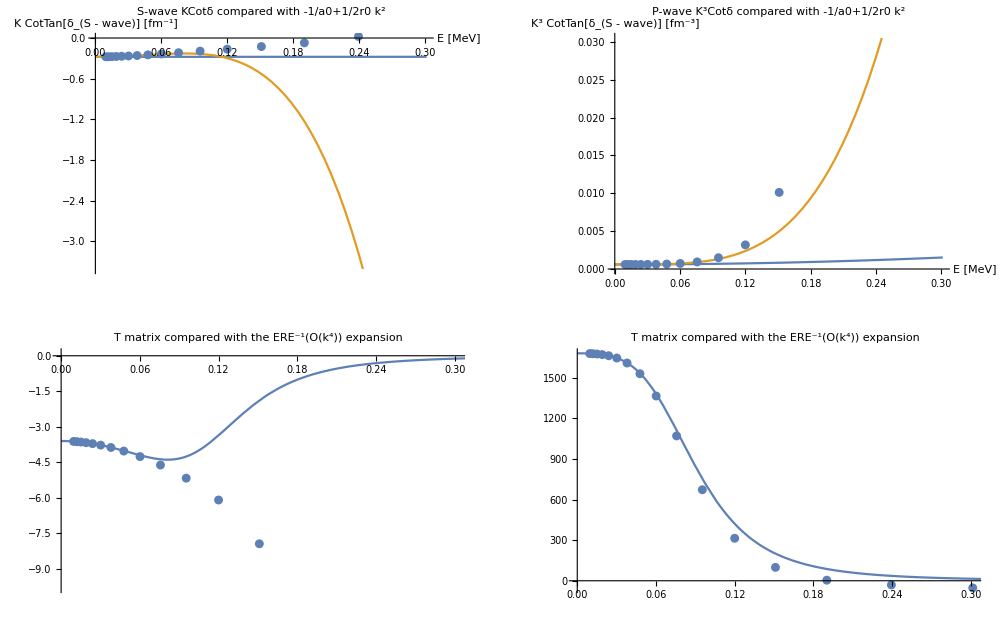

```mathematica
(*2 gaussian test*)
λλ=4;
mycore=coreff4;
rr=10;nGrid=100;
f1=1;f2=4; (* How many momenta should be used to make ere?*)

k0FMin=0.01;
k0FMax=0.3;
Divisions=20;



(*---------------------*)
ErangeMeV=N[findLogDivisions[{(k0FMin hbar)^2/(2 μ),(k0FMax hbar)^2/(2 μ)},Divisions]];
Erange1onfm=Sqrt[2 μ ErangeMeV]/hbar;

(*--------- Test that all is ok------------*)
nn=Flatten[Position[activeLEC⟦All,1⟧,_?(#==λλ&)]]⟦1⟧;
λ=0.25 activeLEC⟦nn⟧⟦1⟧^2;C0=activeLEC⟦nn⟧⟦2⟧;D0=activeLEC⟦nn⟧⟦3⟧;
Print["λ = Λ^2/4 = ",NumberForm[λ,nf],"  ⇒ Λ = ",NumberForm[2 Sqrt[λ],nf]," ; C_0 = ",NumberForm[C0,nf]," ; D_0 = ",NumberForm[D0,nf]];
Print["Core = ",mycore]
ERE=GetERE[mycore];
Print["ERE = ","     a0 = ", ERE⟦1⟧,"     r0 = ", ERE⟦2⟧,"     a1 = ", ERE⟦3⟧,"     r1 = ", ERE⟦4⟧]
PlotERE
```

```mathematica
λλ=6;
rr=10;nGrid=20;
f1=1;f2=3; 
k0FMin=0.01;
k0FMax=0.1;
Divisions=3;
ErangeMeV=N[findLogDivisions[{(k0FMin hbar)^2/(2 μ),(k0FMax hbar)^2/(2 μ)},Divisions]];
Erange1onfm=Sqrt[2 μ ErangeMeV]/hbar;
nn=Flatten[Position[activeLEC⟦All,1⟧,_?(#==λλ&)]]⟦1⟧;
λ=0.25 activeLEC⟦nn⟧⟦1⟧^2;C0=activeLEC⟦nn⟧⟦2⟧;D0=activeLEC⟦nn⟧⟦3⟧;
Print["λ = Λ^2/4 = ",NumberForm[λ,nf],"  ⇒ Λ = ",NumberForm[2 Sqrt[λ],nf]," ; C_0 = ",NumberForm[C0,nf]," ; D_0 = ",NumberForm[D0,nf]];


(*--------run fit---------*)
iIi=0;
xini=Flatten[core6f]⟦;;3⟧;
Goal={3.32^-1, 2.55,-20.23^-1};
CoreFitted6=FindRoot[FitEre[x],{x,xini},PrecisionGoal->4,AccuracyGoal->4]
```

λ = Λ^2/4 = 9.0000  ⇒ Λ = 6.0000 ; C_0 = -1090.5500 ; D_0 = 6552.5000

iter: 1       core={1, 0.0785878, 0.198532, 0.232307 }     |     ERE = {6.80924,5.85637,-106.78,2.18347}     |    to goal: {-0.154345,3.30637,0.0400665}

iter: 2       core={1, 0.0785878, 0.198532, 0.232307 }     |     ERE = {6.80924,5.85637,-106.78,2.18347}     |    to goal: {-0.154345,3.30637,0.0400665}

iter: 3       core={1, 0.0785878, 0.198532, 0.232307 }     |     ERE = {6.80924,5.85637,-106.78,2.18346}     |    to goal: {-0.154345,3.30637,0.0400665}

iter: 4       core={1, 0.0785878, 0.198532, 0.232307 }     |     ERE = {6.80924,5.85637,-106.78,2.18347}     |    to goal: {-0.154345,3.30637,0.0400665}

iter: 5       core={1, 0.0785878, 0.198532, 0.232307 }     |     ERE = {6.80924,5.85637,-106.78,2.18347}     |    to goal: {-0.154345,3.30637,0.0400665}

iter: 6       core={1, 0.0786299, 9.13931, 9.88237 }     |     ERE = {6.836,5.84458,-101.358,2.37821}     |    to goal: {-0.15492,3.29458,0.0395655}

iter: 7       core={1, 0.0786299, 9.13931, 9.88237 }     |     ERE = {6.836,5.84458,-101.358,2.37821}     |    to goal: {-0.15492,3.29458,0.0395655}

iter: 8       core={1, 0.0786299, 9.13931, 9.88237 }     |     ERE = {6.836,5.84458,-101.358,2.37821}     |    to goal: {-0.15492,3.29458,0.0395655}

iter: 9       core={1, 0.0786299, 9.13931, 9.88237 }     |     ERE = {6.836,5.84458,-101.358,2.37821}     |    to goal: {-0.15492,3.29458,0.0395655}

iter: 10       core={1, 0.0786299, 9.13931, 9.88237 }     |     ERE = {6.836,5.84458,-101.358,2.37821}     |    to goal: {-0.15492,3.29458,0.0395655}

iter: 11       core={1, 0.0786832, 102.918, 119.96 }     |     ERE = {6.78816,5.86689,-111.09,2.04823}     |    to goal: {-0.153889,3.31689,0.0404298}

iter: 12       core={1, 0.0786564, 55.7135, 64.5512 }     |     ERE = {6.80985,5.85626,-106.639,2.18826}     |    to goal: {-0.154359,3.30626,0.0400541}

iter: 13       core={1, 0.0786431, 32.4264, 37.2168 }     |     ERE = {6.82312,5.85018,-103.948,2.28152}     |    to goal: {-0.154644,3.30018,0.0398114}

iter: 14       core={1, 0.0786365, 20.7829, 23.5496 }     |     ERE = {6.83046,5.84695,-102.469,2.33586}     |    to goal: {-0.154802,3.29695,0.0396725}

iter: 15       core={1, 0.0786332, 14.9611, 16.716 }     |     ERE = {6.83395,5.84545,-101.769,2.36239}     |    to goal: {-0.154877,3.29545,0.0396054}

iter: 16       core={1, 0.0786316, 12.0502, 13.2992 }     |     ERE = {6.83534,5.84486,-101.491,2.37308}     |    to goal: {-0.154906,3.29486,0.0395784}

iter: 17       core={1, 0.0786307, 10.5948, 11.5908 }     |     ERE = {6.83581,5.84466,-101.397,2.37672}     |    to goal: {-0.154916,3.29466,0.0395693}

iter: 18       core={1, 0.0786303, 9.86703, 10.7366 }     |     ERE = {6.83595,5.8446,-101.369,2.37781}     |    to goal: {-0.154919,3.2946,0.0395666}

iter: 19       core={1, 0.0786301, 9.50317, 10.3095 }     |     ERE = {6.83599,5.84459,-101.361,2.37811}     |    to goal: {-0.15492,3.29459,0.0395658}

iter: 20       core={1, 0.07863, 9.32124, 10.0959 }     |     ERE = {6.836,5.84458,-101.359,2.37819}     |    to goal: {-0.15492,3.29458,0.0395656}

iter: 21       core={1, 0.0786299, 9.23028, 9.98914 }     |     ERE = {6.836,5.84458,-101.358,2.37821}     |    to goal: {-0.15492,3.29458,0.0395656}

iter: 22       core={1, 0.0786299, 9.18479, 9.93576 }     |     ERE = {6.836,5.84458,-101.358,2.37821}     |    to goal: {-0.15492,3.29458,0.0395655}

iter: 23       core={1, 0.0786299, 9.16205, 9.90906 }     |     ERE = {6.836,5.84458,-101.358,2.37821}     |    to goal: {-0.15492,3.29458,0.0395655}

iter: 24       core={1, 0.0786299, 9.15068, 9.89571 }     |     ERE = {6.836,5.84458,-101.358,2.37821}     |    to goal: {-0.15492,3.29458,0.0395655}

iter: 25       core={1, 0.0786299, 9.145, 9.88904 }     |     ERE = {6.836,5.84458,-101.358,2.37821}     |    to goal: {-0.15492,3.29458,0.0395655}

iter: 26       core={1, 0.0786299, 9.14215, 9.8857 }     |     ERE = {6.836,5.84458,-101.358,2.37821}     |    to goal: {-0.15492,3.29458,0.0395655}

iter: 27       core={1, 0.0786299, 9.14073, 9.88404 }     |     ERE = {6.836,5.84458,-101.358,2.37821}     |    to goal: {-0.15492,3.29458,0.0395655}

iter: 28       core={1, 0.0786299, 9.14002, 9.8832 }     |     ERE = {6.836,5.84458,-101.358,2.37821}     |    to goal: {-0.15492,3.29458,0.0395655}

iter: 29       core={1, 0.0786299, 9.13967, 9.88278 }     |     ERE = {6.836,5.84458,-101.358,2.37821}     |    to goal: {-0.15492,3.29458,0.0395655}

iter: 30       core={1, 0.0786299, 9.13949, 9.88258 }     |     ERE = {6.836,5.84458,-101.358,2.37821}     |    to goal: {-0.15492,3.29458,0.0395655}

iter: 31       core={1, 0.0786299, 9.1394, 9.88247 }     |     ERE = {6.836,5.84458,-101.358,2.37821}     |    to goal: {-0.15492,3.29458,0.0395655}

iter: 32       core={1, 0.0786299, 9.13936, 9.88242 }     |     ERE = {6.836,5.84458,-101.358,2.37821}     |    to goal: {-0.15492,3.29458,0.0395655}

iter: 33       core={1, 0.0786299, 9.13933, 9.88239 }     |     ERE = {6.836,5.84458,-101.358,2.37821}     |    to goal: {-0.15492,3.29458,0.0395655}

iter: 34       core={1, 0.0786299, 9.13932, 9.88238 }     |     ERE = {6.836,5.84458,-101.358,2.37821}     |    to goal: {-0.15492,3.29458,0.0395655}

iter: 35       core={1, 0.0786299, 9.13932, 9.88237 }     |     ERE = {6.836,5.84458,-101.358,2.37821}     |    to goal: {-0.15492,3.29458,0.0395655}

iter: 36       core={1, 0.0786299, 9.13931, 9.88237 }     |     ERE = {6.836,5.84458,-101.358,2.37821}     |    to goal: {-0.15492,3.29458,0.0395655}

iter: 37       core={1, 0.0786299, 9.13931, 9.88237 }     |     ERE = {6.836,5.84458,-101.358,2.37821}     |    to goal: {-0.15492,3.29458,0.0395655}

iter: 38       core={1, 0.0786299, 9.13931, 9.88237 }     |     ERE = {6.836,5.84458,-101.358,2.37821}     |    to goal: {-0.15492,3.29458,0.0395655}

iter: 39       core={1, 0.0786299, 9.13931, 9.88237 }     |     ERE = {6.836,5.84458,-101.358,2.37821}     |    to goal: {-0.15492,3.29458,0.0395655}

iter: 40       core={1, 0.0786299, 9.13931, 9.88237 }     |     ERE = {6.836,5.84458,-101.358,2.37821}     |    to goal: {-0.15492,3.29458,0.0395655}

iter: 41       core={1, 0.0786299, 9.13931, 9.88237 }     |     ERE = {6.836,5.84458,-101.358,2.37821}     |    to goal: {-0.15492,3.29458,0.0395655}

iter: 42       core={1, 0.0786299, 9.13931, 9.88237 }     |     ERE = {6.836,5.84458,-101.358,2.37821}     |    to goal: {-0.15492,3.29458,0.0395655}

iter: 43       core={1, 0.0786299, 9.13931, 9.88237 }     |     ERE = {6.836,5.84458,-101.358,2.37821}     |    to goal: {-0.15492,3.29458,0.0395655}

iter: 44       core={1, 0.0786299, 9.13931, 9.88237 }     |     ERE = {6.836,5.84458,-101.358,2.37821}     |    to goal: {-0.15492,3.29458,0.0395655}

iter: 45       core={1, 0.0786299, 9.13931, 9.88237 }     |     ERE = {6.836,5.84458,-101.358,2.37821}     |    to goal: {-0.15492,3.29458,0.0395655}

iter: 46       core={1, 0.0786299, 9.13931, 9.88237 }     |     ERE = {6.836,5.84458,-101.358,2.37821}     |    to goal: {-0.15492,3.29458,0.0395655}

iter: 47       core={1, 0.0786299, 9.13931, 9.88237 }     |     ERE = {6.836,5.84458,-101.358,2.37821}     |    to goal: {-0.15492,3.29458,0.0395655}

iter: 48       core={1, 0.0786299, 9.13931, 9.88237 }     |     ERE = {6.836,5.84458,-101.358,2.37821}     |    to goal: {-0.15492,3.29458,0.0395655}

iter: 49       core={1, 0.078631, -84.7402, -100.11 }     |     ERE = {6.8095,5.85636,-106.717,2.18564}     |    to goal: {-0.154351,3.30636,0.0400609}

iter: 50       core={1, 0.0786305, -37.6336, -44.9182 }     |     ERE = {6.83981,5.84299,-100.596,2.40806}     |    to goal: {-0.155002,3.29299,0.0394908}

iter: 51       core={1, 0.0786305, -37.6336, -44.9182 }     |     ERE = {6.83981,5.84299,-100.596,2.40806}     |    to goal: {-0.155002,3.29299,0.0394908}

iter: 52       core={1, 0.0786305, -37.6336, -44.9182 }     |     ERE = {6.83981,5.84299,-100.596,2.40806}     |    to goal: {-0.155002,3.29299,0.0394908}

iter: 53       core={1, 0.0786305, -37.6336, -44.9182 }     |     ERE = {6.83981,5.84299,-100.596,2.40806}     |    to goal: {-0.155002,3.29299,0.0394908}

iter: 54       core={1, 0.0786305, -37.6336, -44.9182 }     |     ERE = {6.83981,5.84299,-100.596,2.40806}     |    to goal: {-0.155002,3.29299,0.0394908}

iter: 55       core={1, 0.0786383, 260.533, 471.134 }     |     ERE = {6.80829,5.85695,-106.963,2.17747}     |    to goal: {-0.154325,3.30695,0.0400825}

iter: 56       core={1, 0.0786344, 110.822, 212.021 }     |     ERE = {6.83761,5.84392,-101.035,2.3908}     |    to goal: {-0.154955,3.29392,0.039534}

iter: 57       core={1, 0.0786324, 36.5941, 83.5517 }     |     ERE = {6.86278,5.83399,-96.0416,2.60138}     |    to goal: {-0.155491,3.28399,0.0390194}

iter: 58       core={1, 0.0786324, 36.5941, 83.5517 }     |     ERE = {6.86278,5.83399,-96.0416,2.60138}     |    to goal: {-0.155491,3.28399,0.0390194}

iter: 59       core={1, 0.0786324, 36.5941, 83.5517 }     |     ERE = {6.86278,5.83399,-96.0417,2.60137}     |    to goal: {-0.155491,3.28399,0.0390194}

iter: 60       core={1, 0.0786324, 36.5941, 83.5517 }     |     ERE = {6.86278,5.83399,-96.0416,2.60138}     |    to goal: {-0.155491,3.28399,0.0390194}

iter: 61       core={1, 0.0786324, 36.5941, 83.5517 }     |     ERE = {6.86278,5.83399,-96.0416,2.60138}     |    to goal: {-0.155491,3.28399,0.0390194}

iter: 62       core={1, 0.0786238, -269.393, -786.343 }     |     ERE = {6.84897,5.83927,-98.7718,2.48232}     |    to goal: {-0.155197,3.28927,0.0393072}

iter: 63       core={1, 0.0786281, -116.155, -350.701 }     |     ERE = {6.86373,5.83363,-95.8557,2.60984}     |    to goal: {-0.155511,3.28363,0.0389992}

iter: 64       core={1, 0.0786281, -116.155, -350.701 }     |     ERE = {6.86373,5.83363,-95.8557,2.60984}     |    to goal: {-0.155511,3.28363,0.0389992}

iter: 65       core={1, 0.0786281, -116.155, -350.701 }     |     ERE = {6.86373,5.83363,-95.8558,2.60984}     |    to goal: {-0.155511,3.28363,0.0389992}

iter: 66       core={1, 0.0786281, -116.155, -350.701 }     |     ERE = {6.86373,5.83363,-95.8557,2.60984}     |    to goal: {-0.155511,3.28363,0.0389992}

iter: 67       core={1, 0.0786281, -116.155, -350.701 }     |     ERE = {6.86373,5.83363,-95.8557,2.60984}     |    to goal: {-0.155511,3.28363,0.0389992}

iter: 68       core={1, 0.0786622, 758.022, 3249.03 }     |     ERE = {6.84901,5.83935,-98.7601,2.48288}     |    to goal: {-0.155198,3.28935,0.039306}

iter: 69       core={1, 0.0786451, 320.175, 1446.04 }     |     ERE = {6.86393,5.8336,-95.814,2.61178}     |    to goal: {-0.155516,3.2836,0.0389946}

iter: 70       core={1, 0.0786366, 102.01, 547.672 }     |     ERE = {6.87662,5.82905,-93.3308,2.72999}     |    to goal: {-0.155785,3.27905,0.038717}

iter: 71       core={1, 0.0786366, 102.01, 547.672 }     |     ERE = {6.87662,5.82905,-93.3308,2.72999}     |    to goal: {-0.155785,3.27905,0.038717}

iter: 72       core={1, 0.0786366, 102.01, 547.672 }     |     ERE = {6.87662,5.82905,-93.3308,2.72999}     |    to goal: {-0.155785,3.27905,0.038717}

iter: 73       core={1, 0.0786366, 102.01, 547.672 }     |     ERE = {6.87662,5.82905,-93.3308,2.72999}     |    to goal: {-0.155785,3.27905,0.038717}

iter: 74       core={1, 0.0786366, 102.01, 547.672 }     |     ERE = {6.87662,5.82905,-93.3308,2.72999}     |    to goal: {-0.155785,3.27905,0.038717}

iter: 75       core={1, 0.078584, 901.706, 6070.99 }     |     ERE = {6.86761,5.83209,-95.0948,2.64497}     |    to goal: {-0.155594,3.28209,0.0389157}

iter: 76       core={1, 0.0786103, 501.49, 3306.79 }     |     ERE = {6.87156,5.83074,-94.3194,2.68176}     |    to goal: {-0.155678,3.28074,0.0388293}

iter: 77       core={1, 0.0786235, 301.75, 1927.23 }     |     ERE = {6.8741,5.82989,-93.824,2.70574}     |    to goal: {-0.155731,3.27989,0.0387733}

iter: 78       core={1, 0.07863, 201.88, 1237.45 }     |     ERE = {6.87553,5.82941,-93.5443,2.71944}     |    to goal: {-0.155761,3.27941,0.0387414}

iter: 79       core={1, 0.0786333, 151.945, 892.561 }     |     ERE = {6.87622,5.82918,-93.4101,2.72606}     |    to goal: {-0.155776,3.27918,0.0387261}

iter: 80       core={1, 0.078635, 126.978, 720.117 }     |     ERE = {6.87649,5.82909,-93.3564,2.72872}     |    to goal: {-0.155782,3.27909,0.0387199}

iter: 81       core={1, 0.0786358, 114.494, 633.894 }     |     ERE = {6.87658,5.82906,-93.3382,2.72962}     |    to goal: {-0.155784,3.27906,0.0387178}

iter: 82       core={1, 0.0786362, 108.252, 590.783 }     |     ERE = {6.87661,5.82905,-93.3328,2.72989}     |    to goal: {-0.155784,3.27905,0.0387172}

iter: 83       core={1, 0.0786364, 105.131, 569.227 }     |     ERE = {6.87662,5.82905,-93.3313,2.72997}     |    to goal: {-0.155785,3.27905,0.038717}

iter: 84       core={1, 0.0786365, 103.571, 558.45 }     |     ERE = {6.87662,5.82905,-93.3309,2.72999}     |    to goal: {-0.155785,3.27905,0.038717}

iter: 85       core={1, 0.0786366, 102.79, 553.061 }     |     ERE = {6.87662,5.82905,-93.3308,2.72999}     |    to goal: {-0.155785,3.27905,0.038717}

iter: 86       core={1, 0.0786366, 102.4, 550.366 }     |     ERE = {6.87662,5.82905,-93.3308,2.72999}     |    to goal: {-0.155785,3.27905,0.038717}

iter: 87       core={1, 0.0786366, 102.205, 549.019 }     |     ERE = {6.87662,5.82905,-93.3308,2.72999}     |    to goal: {-0.155785,3.27905,0.038717}

iter: 88       core={1, 0.0786366, 102.108, 548.346 }     |     ERE = {6.87662,5.82905,-93.3308,2.72999}     |    to goal: {-0.155785,3.27905,0.038717}

iter: 89       core={1, 0.0786366, 102.059, 548.009 }     |     ERE = {6.87662,5.82905,-93.3308,2.72999}     |    to goal: {-0.155785,3.27905,0.038717}

iter: 90       core={1, 0.0786366, 102.035, 547.84 }     |     ERE = {6.87662,5.82905,-93.3308,2.72999}     |    to goal: {-0.155785,3.27905,0.038717}

iter: 91       core={1, 0.0786366, 102.022, 547.756 }     |     ERE = {6.87662,5.82905,-93.3308,2.72999}     |    to goal: {-0.155785,3.27905,0.038717}

iter: 92       core={1, 0.0786366, 102.016, 547.714 }     |     ERE = {6.87662,5.82905,-93.3308,2.72999}     |    to goal: {-0.155785,3.27905,0.038717}

iter: 93       core={1, 0.0786366, 102.013, 547.693 }     |     ERE = {6.87662,5.82905,-93.3308,2.72999}     |    to goal: {-0.155785,3.27905,0.038717}

iter: 94       core={1, 0.0786366, 102.012, 547.682 }     |     ERE = {6.87662,5.82905,-93.3308,2.72999}     |    to goal: {-0.155785,3.27905,0.038717}

iter: 95       core={1, 0.0786366, 102.011, 547.677 }     |     ERE = {6.87662,5.82905,-93.3308,2.72999}     |    to goal: {-0.155785,3.27905,0.038717}

iter: 96       core={1, 0.0786366, 102.011, 547.675 }     |     ERE = {6.87662,5.82905,-93.3308,2.72999}     |    to goal: {-0.155785,3.27905,0.038717}

iter: 97       core={1, 0.0786366, 102.01, 547.673 }     |     ERE = {6.87662,5.82905,-93.3308,2.72999}     |    to goal: {-0.155785,3.27905,0.038717}

iter: 98       core={1, 0.0786366, 102.01, 547.673 }     |     ERE = {6.87662,5.82905,-93.3308,2.72999}     |    to goal: {-0.155785,3.27905,0.038717}

iter: 99       core={1, 0.0786366, 102.01, 547.672 }     |     ERE = {6.87662,5.82905,-93.3308,2.72999}     |    to goal: {-0.155785,3.27905,0.038717}

iter: 100       core={1, 0.0786366, 102.01, 547.672 }     |     ERE = {6.87662,5.82905,-93.3308,2.72999}     |    to goal: {-0.155785,3.27905,0.038717}

iter: 101       core={1, 0.0786366, 102.01, 547.672 }     |     ERE = {6.87662,5.82905,-93.3308,2.72999}     |    to goal: {-0.155785,3.27905,0.038717}

iter: 102       core={1, 0.0786366, 102.01, 547.672 }     |     ERE = {6.87662,5.82905,-93.3308,2.72999}     |    to goal: {-0.155785,3.27905,0.038717}

iter: 103       core={1, 0.0786366, 102.01, 547.672 }     |     ERE = {6.87662,5.82905,-93.3308,2.72999}     |    to goal: {-0.155785,3.27905,0.038717}

iter: 104       core={1, 0.0786366, 102.01, 547.672 }     |     ERE = {6.87662,5.82905,-93.3308,2.72999}     |    to goal: {-0.155785,3.27905,0.038717}

iter: 105       core={1, 0.0786366, 102.01, 547.672 }     |     ERE = {6.87662,5.82905,-93.3308,2.72999}     |    to goal: {-0.155785,3.27905,0.038717}

iter: 106       core={1, 0.0786366, 102.01, 547.672 }     |     ERE = {6.87662,5.82905,-93.3308,2.72999}     |    to goal: {-0.155785,3.27905,0.038717}

iter: 107       core={1, 0.0786366, 102.01, 547.672 }     |     ERE = {6.87662,5.82905,-93.3308,2.72999}     |    to goal: {-0.155785,3.27905,0.038717}

iter: 108       core={1, 0.0786366, 102.01, 547.672 }     |     ERE = {6.87662,5.82905,-93.3308,2.72999}     |    to goal: {-0.155785,3.27905,0.038717}

iter: 109       core={1, 0.0786366, 102.01, 547.672 }     |     ERE = {6.87662,5.82905,-93.3308,2.72999}     |    to goal: {-0.155785,3.27905,0.038717}

iter: 110       core={1, 0.0786366, 102.01, 547.672 }     |     ERE = {6.87662,5.82905,-93.3308,2.72999}     |    to goal: {-0.155785,3.27905,0.038717}

iter: 111       core={1, 0.0786778, -696.02, -4975.89 }     |     ERE = {6.86933,5.83173,-94.7531,2.66122}     |    to goal: {-0.15563,3.28173,0.0388778}

iter: 112       core={1, 0.0786572, -296.681, -2211.86 }     |     ERE = {6.87639,5.82919,-93.3762,2.72778}     |    to goal: {-0.15578,3.27919,0.0387222}

iter: 113       core={1, 0.0786469, -97.3352, -832.096 }     |     ERE = {6.88223,5.82717,-92.2403,2.78497}     |    to goal: {-0.155903,3.27717,0.0385903}

iter: 114       core={1, 0.0786469, -97.3352, -832.096 }     |     ERE = {6.88223,5.82717,-92.2403,2.78497}     |    to goal: {-0.155903,3.27717,0.0385903}

iter: 115       core={1, 0.0786469, -97.3352, -832.096 }     |     ERE = {6.88223,5.82717,-92.2404,2.78496}     |    to goal: {-0.155903,3.27717,0.0385903}

iter: 116       core={1, 0.0786469, -97.3352, -832.096 }     |     ERE = {6.88223,5.82717,-92.2403,2.78497}     |    to goal: {-0.155903,3.27717,0.0385903}

iter: 117       core={1, 0.0786469, -97.3352, -832.096 }     |     ERE = {6.88223,5.82717,-92.2403,2.78497}     |    to goal: {-0.155903,3.27717,0.0385903}

iter: 118       core={1, 0.0786567, -805.885, -9189.81 }     |     ERE = {6.87759,5.82877,-93.1427,2.73937}     |    to goal: {-0.155805,3.27877,0.0386953}

iter: 119       core={1, 0.0786518, -451.438, -5008.92 }     |     ERE = {6.87971,5.82803,-92.729,2.76011}     |    to goal: {-0.15585,3.27803,0.0386474}

iter: 120       core={1, 0.0786494, -274.387, -2920.51 }     |     ERE = {6.881,5.82759,-92.4787,2.77279}     |    to goal: {-0.155877,3.27759,0.0386182}

iter: 121       core={1, 0.0786481, -185.861, -1876.3 }     |     ERE = {6.8817,5.82735,-92.3421,2.77976}     |    to goal: {-0.155892,3.27735,0.0386022}

iter: 122       core={1, 0.0786475, -141.598, -1354.2 }     |     ERE = {6.88203,5.82724,-92.2778,2.78305}     |    to goal: {-0.155899,3.27724,0.0385947}

iter: 123       core={1, 0.0786472, -119.467, -1093.15 }     |     ERE = {6.88217,5.82719,-92.2523,2.78435}     |    to goal: {-0.155902,3.27719,0.0385917}

iter: 124       core={1, 0.0786471, -108.401, -962.621 }     |     ERE = {6.88221,5.82718,-92.2438,2.78479}     |    to goal: {-0.155903,3.27718,0.0385907}

iter: 125       core={1, 0.078647, -102.868, -897.358 }     |     ERE = {6.88222,5.82717,-92.2412,2.78492}     |    to goal: {-0.155903,3.27717,0.0385904}

iter: 126       core={1, 0.0786469, -100.102, -864.727 }     |     ERE = {6.88223,5.82717,-92.2405,2.78495}     |    to goal: {-0.155903,3.27717,0.0385903}

iter: 127       core={1, 0.0786469, -98.7184, -848.411 }     |     ERE = {6.88223,5.82717,-92.2403,2.78496}     |    to goal: {-0.155903,3.27717,0.0385903}

iter: 128       core={1, 0.0786469, -98.0268, -840.253 }     |     ERE = {6.88223,5.82717,-92.2403,2.78497}     |    to goal: {-0.155903,3.27717,0.0385903}

iter: 129       core={1, 0.0786469, -97.681, -836.174 }     |     ERE = {6.88223,5.82717,-92.2403,2.78497}     |    to goal: {-0.155903,3.27717,0.0385903}

iter: 130       core={1, 0.0786469, -97.5081, -834.135 }     |     ERE = {6.88223,5.82717,-92.2403,2.78497}     |    to goal: {-0.155903,3.27717,0.0385903}

iter: 131       core={1, 0.0786469, -97.4217, -833.115 }     |     ERE = {6.88223,5.82717,-92.2403,2.78497}     |    to goal: {-0.155903,3.27717,0.0385903}

iter: 132       core={1, 0.0786469, -97.3785, -832.605 }     |     ERE = {6.88223,5.82717,-92.2403,2.78497}     |    to goal: {-0.155903,3.27717,0.0385903}

iter: 133       core={1, 0.0786469, -97.3568, -832.35 }     |     ERE = {6.88223,5.82717,-92.2403,2.78497}     |    to goal: {-0.155903,3.27717,0.0385903}

iter: 134       core={1, 0.0786469, -97.346, -832.223 }     |     ERE = {6.88223,5.82717,-92.2403,2.78497}     |    to goal: {-0.155903,3.27717,0.0385903}

iter: 135       core={1, 0.0786469, -97.3406, -832.159 }     |     ERE = {6.88223,5.82717,-92.2403,2.78497}     |    to goal: {-0.155903,3.27717,0.0385903}

iter: 136       core={1, 0.0786469, -97.3379, -832.127 }     |     ERE = {6.88223,5.82717,-92.2403,2.78497}     |    to goal: {-0.155903,3.27717,0.0385903}

iter: 137       core={1, 0.0786469, -97.3366, -832.111 }     |     ERE = {6.88223,5.82717,-92.2403,2.78497}     |    to goal: {-0.155903,3.27717,0.0385903}

iter: 138       core={1, 0.0786469, -97.3359, -832.104 }     |     ERE = {6.88223,5.82717,-92.2403,2.78497}     |    to goal: {-0.155903,3.27717,0.0385903}

iter: 139       core={1, 0.0786469, -97.3356, -832.1 }     |     ERE = {6.88223,5.82717,-92.2403,2.78497}     |    to goal: {-0.155903,3.27717,0.0385903}

iter: 140       core={1, 0.0786469, -97.3354, -832.098 }     |     ERE = {6.88223,5.82717,-92.2403,2.78497}     |    to goal: {-0.155903,3.27717,0.0385903}

iter: 141       core={1, 0.0786469, -97.3353, -832.097 }     |     ERE = {6.88223,5.82717,-92.2403,2.78497}     |    to goal: {-0.155903,3.27717,0.0385903}

iter: 142       core={1, 0.0786469, -97.3353, -832.096 }     |     ERE = {6.88223,5.82717,-92.2403,2.78497}     |    to goal: {-0.155903,3.27717,0.0385903}

iter: 143       core={1, 0.0786469, -97.3352, -832.096 }     |     ERE = {6.88223,5.82717,-92.2403,2.78497}     |    to goal: {-0.155903,3.27717,0.0385903}

iter: 144       core={1, 0.0786469, -97.3352, -832.096 }     |     ERE = {6.88223,5.82717,-92.2403,2.78497}     |    to goal: {-0.155903,3.27717,0.0385903}

iter: 145       core={1, 0.0786469, -97.3352, -832.096 }     |     ERE = {6.88223,5.82717,-92.2403,2.78497}     |    to goal: {-0.155903,3.27717,0.0385903}

iter: 146       core={1, 0.0786469, -97.3352, -832.096 }     |     ERE = {6.88223,5.82717,-92.2403,2.78497}     |    to goal: {-0.155903,3.27717,0.0385903}

iter: 147       core={1, 0.0786469, -97.3352, -832.096 }     |     ERE = {6.88223,5.82717,-92.2403,2.78497}     |    to goal: {-0.155903,3.27717,0.0385903}

iter: 148       core={1, 0.0786469, -97.3352, -832.096 }     |     ERE = {6.88223,5.82717,-92.2403,2.78497}     |    to goal: {-0.155903,3.27717,0.0385903}

iter: 149       core={1, 0.0786469, -97.3352, -832.096 }     |     ERE = {6.88223,5.82717,-92.2403,2.78497}     |    to goal: {-0.155903,3.27717,0.0385903}

iter: 150       core={1, 0.0786469, -97.3352, -832.096 }     |     ERE = {6.88223,5.82717,-92.2403,2.78497}     |    to goal: {-0.155903,3.27717,0.0385903}

iter: 151       core={1, 0.0786469, -97.3352, -832.096 }     |     ERE = {6.88223,5.82717,-92.2403,2.78497}     |    to goal: {-0.155903,3.27717,0.0385903}

iter: 152       core={1, 0.0786469, -97.3352, -832.096 }     |     ERE = {6.88223,5.82717,-92.2403,2.78497}     |    to goal: {-0.155903,3.27717,0.0385903}

iter: 153       core={1, 0.0786469, -97.3352, -832.096 }     |     ERE = {6.88223,5.82717,-92.2403,2.78497}     |    to goal: {-0.155903,3.27717,0.0385903}

iter: 154       core={1, 0.0786469, -97.3352, -832.096 }     |     ERE = {6.88223,5.82717,-92.2403,2.78497}     |    to goal: {-0.155903,3.27717,0.0385903}

iter: 155       core={1, 0.0786469, -97.3352, -832.096 }     |     ERE = {6.88223,5.82717,-92.2403,2.78497}     |    to goal: {-0.155903,3.27717,0.0385903}

iter: 156       core={1, 0.0786469, -97.3352, -832.096 }     |     ERE = {6.88223,5.82717,-92.2403,2.78497}     |    to goal: {-0.155903,3.27717,0.0385903}

iter: 157       core={1, 0.0786469, -97.3352, -832.096 }     |     ERE = {6.88223,5.82717,-92.2403,2.78497}     |    to goal: {-0.155903,3.27717,0.0385903}

iter: 158       core={1, 0.0786469, -97.3352, -832.096 }     |     ERE = {6.88223,5.82717,-92.2403,2.78497}     |    to goal: {-0.155903,3.27717,0.0385903}

iter: 159       core={1, 0.0786469, -97.3352, -832.096 }     |     ERE = {6.88223,5.82717,-92.2403,2.78497}     |    to goal: {-0.155903,3.27717,0.0385903}

iter: 160       core={1, 0.0786469, -97.3352, -832.096 }     |     ERE = {6.88223,5.82717,-92.2403,2.78497}     |    to goal: {-0.155903,3.27717,0.0385903}

iter: 161       core={1, 0.0786469, -97.3352, -832.096 }     |     ERE = {6.88223,5.82717,-92.2403,2.78497}     |    to goal: {-0.155903,3.27717,0.0385903}

iter: 162       core={1, 0.0786469, -97.3352, -832.096 }     |     ERE = {6.88223,5.82717,-92.2403,2.78497}     |    to goal: {-0.155903,3.27717,0.0385903}

iter: 163       core={1, 0.0786469, -97.3352, -832.096 }     |     ERE = {6.88223,5.82717,-92.2403,2.78497}     |    to goal: {-0.155903,3.27717,0.0385903}

iter: 164       core={1, 0.0786469, -97.3352, -832.096 }     |     ERE = {6.88223,5.82717,-92.2403,2.78497}     |    to goal: {-0.155903,3.27717,0.0385903}

iter: 165       core={1, 0.0786469, -97.3352, -832.096 }     |     ERE = {6.88223,5.82717,-92.2403,2.78497}     |    to goal: {-0.155903,3.27717,0.0385903}

iter: 166       core={1, 0.0786469, -97.3352, -832.096 }     |     ERE = {6.88223,5.82717,-92.2403,2.78497}     |    to goal: {-0.155903,3.27717,0.0385903}

iter: 167       core={1, 0.0786469, -97.3352, -832.096 }     |     ERE = {6.88223,5.82717,-92.2403,2.78497}     |    to goal: {-0.155903,3.27717,0.0385903}

iter: 168       core={1, 0.0786469, -97.3352, -832.096 }     |     ERE = {6.88223,5.82717,-92.2403,2.78497}     |    to goal: {-0.155903,3.27717,0.0385903}

iter: 169       core={1, 0.0786469, -97.3352, -832.096 }     |     ERE = {6.88223,5.82717,-92.2403,2.78497}     |    to goal: {-0.155903,3.27717,0.0385903}

iter: 170       core={1, 0.0786469, -97.3352, -832.096 }     |     ERE = {6.88223,5.82717,-92.2403,2.78497}     |    to goal: {-0.155903,3.27717,0.0385903}

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{x→{0.0786469,-97.3352,-832.096}}

```mathematica
Xx=Join[{1},x/.CoreFitted6];
coreff6={{Xx⟦1⟧,Xx⟦2⟧},{Xx⟦3⟧,Xx⟦4⟧}};
```

λ = Λ^2/4 = 9.0000  ⇒ Λ = 6.0000 ; C_0 = -1090.5500 ; D_0 = 6552.5000

Core = {{1,0.0786469},{-97.3352,-832.096}}

ERE =      a0 = 6.80227     r0 = 5.64276     a1 = -112.156+1.1452 ⅈ     r1 = 1.34524+0.0203618 ⅈ

(using more points and up to p^4)  a0 = 6.80229  r0 = 5.63638   ω = 6.92894

S Pole Poitions in momentum: {-0.173794+0.179052 ⅈ,0.+0.431532 ⅈ,0.-0.789636 ⅈ,0.173794+0.179052 ⅈ}

S Pole Poitions in energy:   {-0.05129-1.72067 ⅈ,-5.14849+0. ⅈ,-17.2388+0. ⅈ,-0.05129+1.72067 ⅈ}

(using more points and up to p^4)  a0 = -112.131+1.1451 ⅈ  r0 = 1.30095+0.0196279 ⅈ   ω = 48.1274+0.797544 ⅈ

P Pole Poitions in momentum: {-0.06114-0.0957307 ⅈ,-0.0548395+0.106373 ⅈ,0.0552871+0.106206 ⅈ,0.0610367-0.0960755 ⅈ}

P Pole Poitions in energy:   {-0.150022+0.323638 ⅈ,-0.22969-0.322558 ⅈ,-0.227344+0.32468 ⅈ,-0.1522-0.324255 ⅈ}

ListPlot::prng: Value of option PlotRange -> {{0.00953176,0.00897673+0.0000919628 ⅈ},All} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

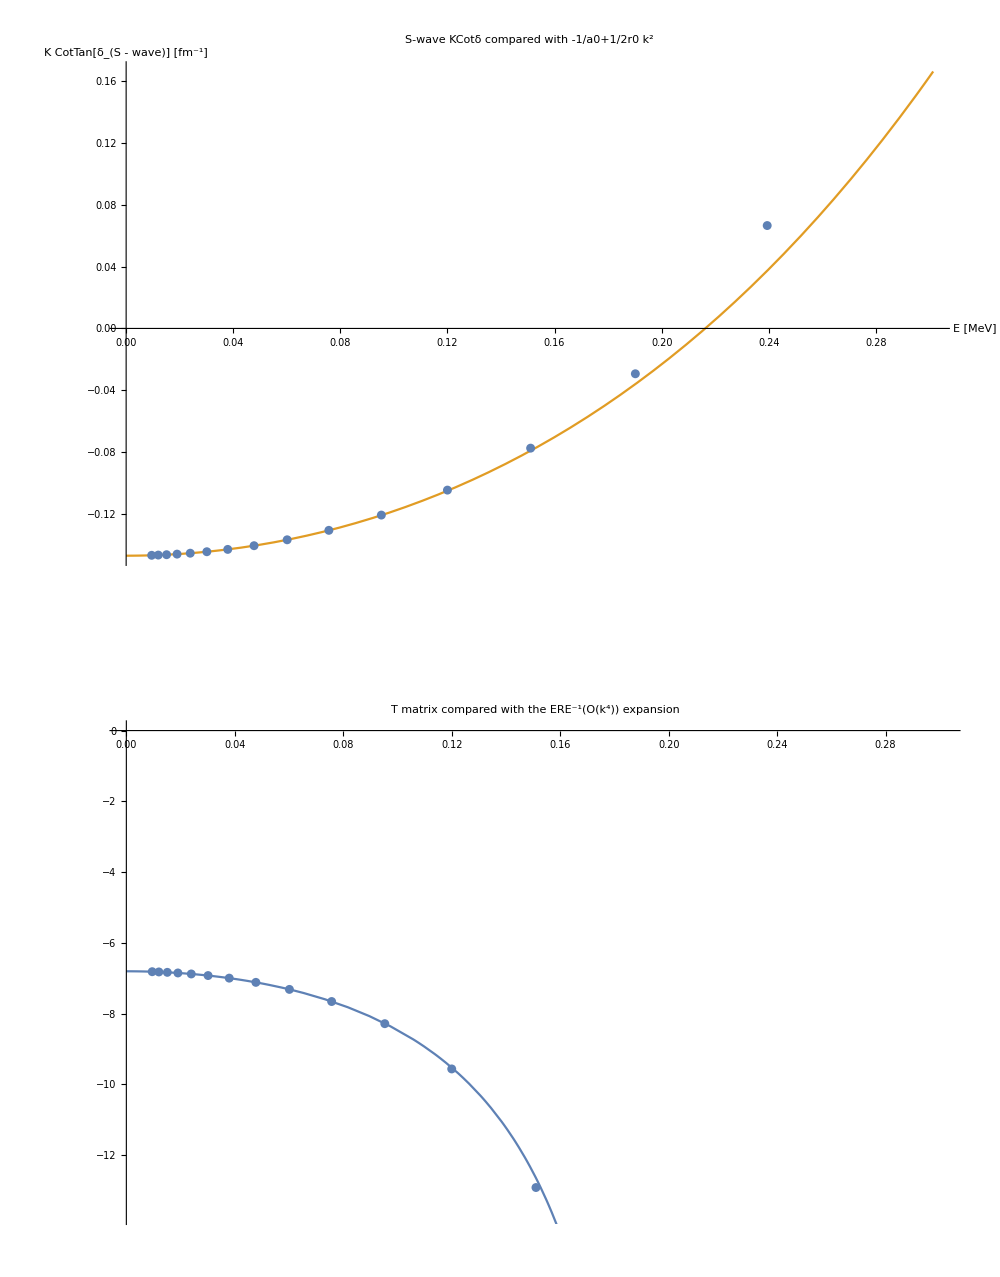

```mathematica
(*Go with the fit*)
λλ=6;
mycore=coreff6;
rr=10;nGrid=100;
f1=1;f2=4; (* How many momenta should be used to make ere?*)

k0FMin=0.01;
k0FMax=0.3;
Divisions=20;


(*---------------------*)
ErangeMeV=N[findLogDivisions[{(k0FMin hbar)^2/(2 μ),(k0FMax hbar)^2/(2 μ)},Divisions]];
Erange1onfm=Sqrt[2 μ ErangeMeV]/hbar;
(*--------- Test that all is ok------------*)
nn=Flatten[Position[activeLEC⟦All,1⟧,_?(#==λλ&)]]⟦1⟧;
λ=0.25 activeLEC⟦nn⟧⟦1⟧^2;C0=activeLEC⟦nn⟧⟦2⟧;D0=activeLEC⟦nn⟧⟦3⟧;
Print["λ = Λ^2/4 = ",NumberForm[λ,nf],"  ⇒ Λ = ",NumberForm[2 Sqrt[λ],nf]," ; C_0 = ",NumberForm[C0,nf]," ; D_0 = ",NumberForm[D0,nf]];
Print["Core = ",mycore]
ERE=GetERE[mycore];
Print["ERE = ","     a0 = ", ERE⟦1⟧,"     r0 = ", ERE⟦2⟧,"     a1 = ", ERE⟦3⟧,"     r1 = ", ERE⟦4⟧]
PlotERE
```

## Fit the core from the ERE parameters with 1 gaussian

λ = Λ^2/4 = 4.0000  ⇒ Λ = 4.0000 ; C_0 = -505.1500 ; D_0 = 1426.7500

Core = {{-1.34759,0.178617},{0.208715,1.03031},{1.41757,0.178617}}

dataS = {{0.00601414,-0.140093},{0.0190184,-0.13932},{0.0601414,-0.131499},{0.190184,-0.0418859}}

ERE =      a0 = 7.13348     r0 = 4.80204     a1 = 61.6853     r1 = -0.650466

S Pole Poitions in momentum: {-0.214843+0.203555 ⅈ,0.+0.249429 ⅈ,0.-0.656539 ⅈ,0.214843+0.203555 ⅈ}

S Pole Poitions in energy:   {0.130574-2.41816 ⅈ,-1.72008+0. ⅈ,-11.9172+0. ⅈ,0.130574+2.41816 ⅈ}

P Pole Poitions in momentum: {-0.309442+0.348651 ⅈ,0.-0.173873 ⅈ,0.+0.393301 ⅈ,0.309442+0.348651 ⅈ}

P Pole Poitions in energy:   {-0.713385-5.9656 ⅈ,-0.835826+0. ⅈ,-4.27666+0. ⅈ,-0.713385+5.9656 ⅈ}

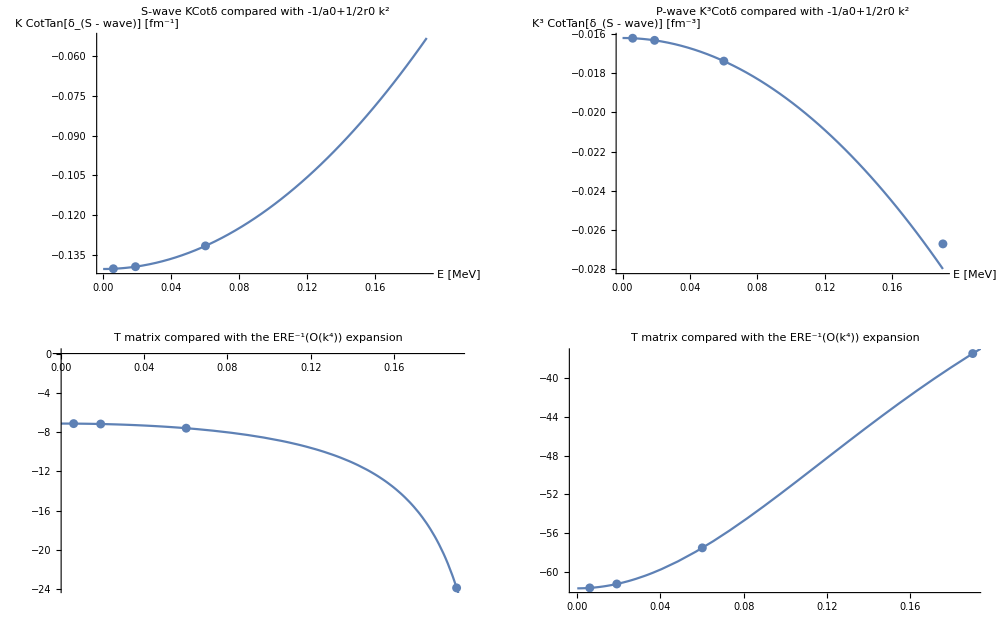

```mathematica
(*Go with the fit*)
λλ=4;
mycore=core4;
rr=10;nGrid=20;
f1=1;f2=3; 

k0FMin=0.01;
k0FMax=0.1;
Divisions=3;


Goal={3.32, 2.55,-20.23,0.75};

(*---------------------*)
ErangeMeV=N[findLogDivisions[{(k0FMin hbar)^2/(2 μ),(k0FMax hbar)^2/(2 μ)},Divisions]];
Erange1onfm=Sqrt[2 μ ErangeMeV]/hbar;

(*--------- Test that all is ok------------*)
nn=Flatten[Position[activeLEC⟦All,1⟧,_?(#==λλ&)]]⟦1⟧;
λ=0.25 activeLEC⟦nn⟧⟦1⟧^2;C0=activeLEC⟦nn⟧⟦2⟧;D0=activeLEC⟦nn⟧⟦3⟧;
Print["λ = Λ^2/4 = ",NumberForm[λ,nf],"  ⇒ Λ = ",NumberForm[2 Sqrt[λ],nf]," ; C_0 = ",NumberForm[C0,nf]," ; D_0 = ",NumberForm[D0,nf]];
Print["Core = ",mycore]
ERE=GetERE[mycore];
Print["ERE = ","     a0 = ", ERE⟦1⟧,"     r0 = ", ERE⟦2⟧,"     a1 = ", ERE⟦3⟧,"     r1 = ", ERE⟦4⟧]
PlotERE
```

```mathematica
(*--------run fit---------*)
(* I need a simple function to contain the fit*)
FitEre1[x_?(VectorQ[#, NumericQ]&)]:=Module[{Aa0=x[[1]]},
mycore={{1.,Aa0}};
ERE=GetERE[mycore];
yy=ERE⟦Nere⟧;
iIi=iIi+1;
Print["iter: ", iIi, "       core={1, ",Aa0,"}     |     ERE = ", ERE  , "     |    to goal: ",yy-Goal ⟦Nere⟧];
yy-Goal⟦Nere⟧
]
```

```mathematica
xini={core4⟦1,2⟧};
iIi=0;
Nere=1;
CoreFitted4=FindRoot[FitEre1[x],{x,xini},PrecisionGoal->4,AccuracyGoal->4]
Goal
```

dataS = {{0.00601414,-0.228623},{0.0190184,-0.228166},{0.0601414,-0.223575},{0.190184,-0.175892}}

iter: 1       core={1, 0.178617}     |     ERE = {4.37302,2.82006,4.32579,-2.72966}     |    to goal: 1.05302

dataS = {{0.00601414,-0.228623},{0.0190184,-0.228166},{0.0601414,-0.223575},{0.190184,-0.175892}}

iter: 2       core={1, 0.178617}     |     ERE = {4.37302,2.82006,4.32579,-2.72966}     |    to goal: 1.05302

dataS = {{0.00601414,-0.228623},{0.0190184,-0.228166},{0.0601414,-0.223575},{0.190184,-0.175892}}

iter: 3       core={1, 0.178617}     |     ERE = {4.37302,2.82006,4.32578,-2.72966}     |    to goal: 1.05302

dataS = {{0.00601414,-0.285621},{0.0190184,-0.285261},{0.0601414,-0.281659},{0.190184,-0.244973}}

iter: 4       core={1, 0.236239}     |     ERE = {3.50065,2.21304,2.09156,-3.37493}     |    to goal: 0.180649

dataS = {{0.00601414,-0.285621},{0.0190184,-0.285261},{0.0601414,-0.281659},{0.190184,-0.244973}}

iter: 5       core={1, 0.236239}     |     ERE = {3.50065,2.21304,2.09156,-3.37493}     |    to goal: 0.180649

dataS = {{0.00601414,-0.285621},{0.0190184,-0.285261},{0.0601414,-0.281659},{0.190184,-0.244973}}

iter: 6       core={1, 0.236239}     |     ERE = {3.50065,2.21304,2.09156,-3.37493}     |    to goal: 0.180649

dataS = {{0.00601414,-0.300518},{0.0190184,-0.300178},{0.0601414,-0.29678},{0.190184,-0.262319}}

iter: 7       core={1, 0.250606}     |     ERE = {3.32717,2.0877,1.79277,-3.43341}     |    to goal: 0.00717093

dataS = {{0.00601414,-0.300518},{0.0190184,-0.300178},{0.0601414,-0.29678},{0.190184,-0.262319}}

iter: 8       core={1, 0.250606}     |     ERE = {3.32717,2.0877,1.79277,-3.43341}     |    to goal: 0.00717093

dataS = {{0.00601414,-0.300518},{0.0190184,-0.300178},{0.0601414,-0.29678},{0.190184,-0.262319}}

iter: 9       core={1, 0.250606}     |     ERE = {3.32717,2.0877,1.79277,-3.43341}     |    to goal: 0.00717076

dataS = {{0.00601414,-0.301166},{0.0190184,-0.300827},{0.0601414,-0.297438},{0.190184,-0.263069}}

iter: 10       core={1, 0.251224}     |     ERE = {3.32001,2.08247,1.78126,-3.43454}     |    to goal: 0.0000121354

dataS = {{0.00601414,-0.301166},{0.0190184,-0.300827},{0.0601414,-0.297438},{0.190184,-0.263069}}

iter: 11       core={1, 0.251224}     |     ERE = {3.32001,2.08247,1.78126,-3.43454}     |    to goal: 0.0000121354

dataS = {{0.00601414,-0.301166},{0.0190184,-0.300827},{0.0601414,-0.297438},{0.190184,-0.263069}}

iter: 12       core={1, 0.251224}     |     ERE = {3.32001,2.08247,1.78126,-3.43454}     |    to goal: 0.0000119631

dataS = {{0.00601414,-0.301167},{0.0190184,-0.300828},{0.0601414,-0.297439},{0.190184,-0.26307}}

iter: 13       core={1, 0.251225}     |     ERE = {3.32,2.08246,1.78124,-3.43454}     |    to goal: 3.22991×10^-11

{x→{0.251225}}

{3.32,2.55,-20.23,0.75}

```mathematica
xini={core4⟦1,2⟧};
iIi=0;
Nere=2;
CoreFitted4=FindRoot[FitEre1[x],{x,xini},PrecisionGoal->4,AccuracyGoal->4]
Goal
```

dataS = {{0.00601414,-0.228623},{0.0190184,-0.228166},{0.0601414,-0.223575},{0.190184,-0.175892}}

iter: 1       core={1, 0.178617}     |     ERE = {4.37302,2.82006,4.32579,-2.72966}     |    to goal: 0.270059

dataS = {{0.00601414,-0.228623},{0.0190184,-0.228166},{0.0601414,-0.223575},{0.190184,-0.175892}}

iter: 2       core={1, 0.178617}     |     ERE = {4.37302,2.82006,4.32579,-2.72966}     |    to goal: 0.270059

dataS = {{0.00601414,-0.228623},{0.0190184,-0.228166},{0.0601414,-0.223575},{0.190184,-0.175892}}

iter: 3       core={1, 0.178617}     |     ERE = {4.37302,2.82006,4.32578,-2.72966}     |    to goal: 0.270058

dataS = {{0.00601414,-0.24948},{0.0190184,-0.249063},{0.0601414,-0.244881},{0.190184,-0.201803}}

iter: 4       core={1, 0.200171}     |     ERE = {4.00759,2.56874,3.21716,-3.02458}     |    to goal: 0.0187441

dataS = {{0.00601414,-0.24948},{0.0190184,-0.249063},{0.0601414,-0.244881},{0.190184,-0.201803}}

iter: 5       core={1, 0.200171}     |     ERE = {4.00759,2.56874,3.21716,-3.02458}     |    to goal: 0.0187441

dataS = {{0.00601414,-0.24948},{0.0190184,-0.249063},{0.0601414,-0.244881},{0.190184,-0.201804}}

iter: 6       core={1, 0.200171}     |     ERE = {4.00759,2.56874,3.21715,-3.02458}     |    to goal: 0.0187439

dataS = {{0.00601414,-0.25117},{0.0190184,-0.250756},{0.0601414,-0.246605},{0.190184,-0.203866}}

iter: 7       core={1, 0.201895}     |     ERE = {3.98063,2.5501,3.14636,-3.0461}     |    to goal: 0.0000969241

dataS = {{0.00601414,-0.25117},{0.0190184,-0.250756},{0.0601414,-0.246605},{0.190184,-0.203866}}

iter: 8       core={1, 0.201895}     |     ERE = {3.98063,2.5501,3.14636,-3.0461}     |    to goal: 0.0000969241

dataS = {{0.00601414,-0.25117},{0.0190184,-0.250756},{0.0601414,-0.246605},{0.190184,-0.203866}}

iter: 9       core={1, 0.201895}     |     ERE = {3.98063,2.5501,3.14636,-3.0461}     |    to goal: 0.0000967638

dataS = {{0.00601414,-0.251179},{0.0190184,-0.250765},{0.0601414,-0.246614},{0.190184,-0.203876}}

iter: 10       core={1, 0.201904}     |     ERE = {3.98049,2.55,3.146,-3.04621}     |    to goal: 4.09137×10^-9

{x→{0.201904}}

{3.32,2.55,-20.23,0.75}

```mathematica
xini={0.001};
iIi=0;
Nere=3;
CoreFitted4=FindRoot[FitEre1[x],{x,xini},PrecisionGoal->4,AccuracyGoal->4]
Goal
```

dataS = {{0.00601414,-0.121946},{0.0190184,-0.120467},{0.0601414,-0.16843},{0.190184,-0.0290955}}

iter: 1       core={1, 0.001}     |     ERE = {8.43002,-27.3839,46.889,-5.88252}     |    to goal: 67.119

dataS = {{0.00601414,-0.121946},{0.0190184,-0.120467},{0.0601414,-0.16843},{0.190184,-0.0290955}}

iter: 2       core={1, 0.001}     |     ERE = {8.43002,-27.3839,46.889,-5.88252}     |    to goal: 67.119

dataS = {{0.00601414,-0.121946},{0.0190184,-0.120467},{0.0601414,-0.168434},{0.190184,-0.0290955}}

iter: 3       core={1, 0.00100001}     |     ERE = {8.43003,-27.3862,46.8919,-5.88158}     |    to goal: 67.1219

dataS = {{0.00601414,-0.119179},{0.0190184,-0.116927},{0.0601414,-0.137368},{0.190184,-0.0310999}}

iter: 4       core={1, 0.000655068}     |     ERE = {8.54393,-11.132,-62.9827,-2.32599}     |    to goal: -42.7527

dataS = {{0.00601414,-0.119179},{0.0190184,-0.116927},{0.0601414,-0.137368},{0.190184,-0.0310999}}

iter: 5       core={1, 0.000655068}     |     ERE = {8.54393,-11.132,-62.9827,-2.32599}     |    to goal: -42.7527

dataS = {{0.00601414,-0.119179},{0.0190184,-0.116927},{0.0601414,-0.137368},{0.190184,-0.0310999}}

iter: 6       core={1, 0.000655082}     |     ERE = {8.54391,-11.1321,-62.9752,-2.32639}     |    to goal: -42.7452

dataS = {{0.00601414,-0.120004},{0.0190184,-0.118018},{0.0601414,-0.140358},{0.190184,-0.0305775}}

iter: 7       core={1, 0.000739537}     |     ERE = {8.48321,-12.3239,-25.7496,-8.9356}     |    to goal: -5.51963

dataS = {{0.00601414,-0.120004},{0.0190184,-0.118018},{0.0601414,-0.140358},{0.190184,-0.0305775}}

iter: 8       core={1, 0.000739537}     |     ERE = {8.48321,-12.3239,-25.7496,-8.9356}     |    to goal: -5.51963

dataS = {{0.00601414,-0.120004},{0.0190184,-0.118018},{0.0601414,-0.140358},{0.190184,-0.0305775}}

iter: 9       core={1, 0.000739552}     |     ERE = {8.4832,-12.3242,-25.7439,-8.93859}     |    to goal: -5.51392

dataS = {{0.00601414,-0.120132},{0.0190184,-0.118185},{0.0601414,-0.140988},{0.190184,-0.0304905}}

iter: 10       core={1, 0.000753939}     |     ERE = {8.47456,-12.606,-20.3526,-12.7003}     |    to goal: -0.122585

dataS = {{0.00601414,-0.120132},{0.0190184,-0.118185},{0.0601414,-0.140988},{0.190184,-0.0304905}}

iter: 11       core={1, 0.000753939}     |     ERE = {8.47456,-12.606,-20.3526,-12.7003}     |    to goal: -0.122585

dataS = {{0.00601414,-0.120132},{0.0190184,-0.118186},{0.0601414,-0.140989},{0.190184,-0.0304904}}

iter: 12       core={1, 0.000753954}     |     ERE = {8.47455,-12.6063,-20.3471,-12.7053}     |    to goal: -0.117126

dataS = {{0.00601414,-0.120135},{0.0190184,-0.118189},{0.0601414,-0.141004},{0.190184,-0.0304885}}

iter: 13       core={1, 0.000754273}     |     ERE = {8.47437,-12.6129,-20.2301,-12.8143}     |    to goal: -0.0000611176

{x→{0.000754273}}

{3.32,2.55,-20.23,0.75}

```mathematica
xini={core4⟦1,2⟧};
iIi=0;
Nere=4;
CoreFitted4=FindRoot[FitEre1[x],{x,xini},PrecisionGoal->4,AccuracyGoal->4]
Goal
```

dataS = {{0.00601414,-0.228623},{0.0190184,-0.228166},{0.0601414,-0.223575},{0.190184,-0.175892}}

iter: 1       core={1, 0.178617}     |     ERE = {4.37302,2.82006,4.32579,-2.72966}     |    to goal: -3.47966

dataS = {{0.00601414,-0.228623},{0.0190184,-0.228166},{0.0601414,-0.223575},{0.190184,-0.175892}}

iter: 2       core={1, 0.178617}     |     ERE = {4.37302,2.82006,4.32579,-2.72966}     |    to goal: -3.47966

dataS = {{0.00601414,-0.228623},{0.0190184,-0.228166},{0.0601414,-0.223575},{0.190184,-0.175892}}

iter: 3       core={1, 0.178617}     |     ERE = {4.37302,2.82006,4.32578,-2.72966}     |    to goal: -3.47966

dataS = {{0.00601414,-0.0998794},{0.0190184,-0.0987914},{0.0601414,-0.0876423},{0.190184,0.0653639}}

iter: 4       core={1, -0.0596442}     |     ERE = {9.99847,6.84093,333.181,-0.34426}     |    to goal: -1.09426

dataS = {{0.00601414,-0.0998794},{0.0190184,-0.0987914},{0.0601414,-0.0876423},{0.190184,0.0653639}}

iter: 5       core={1, -0.0596442}     |     ERE = {9.99847,6.84093,333.181,-0.34426}     |    to goal: -1.09426

dataS = {{0.00601414,-0.0998794},{0.0190184,-0.0987914},{0.0601414,-0.0876423},{0.190184,0.0653639}}

iter: 6       core={1, -0.0596442}     |     ERE = {9.99847,6.84093,333.181,-0.34426}     |    to goal: -1.09426

FindRoot::jsing: Encountered a singular Jacobian at the point {x} = {-0.0596442}. Try perturbing the initial point(s).

{x→{-0.0596442}}

{3.32,2.55,-20.23,0.75}